# Function

## Temperature

```mathematica
Rbpress[T_]:=
(*
Calculates the vapor pressure of Na depending on the temprerature of the cell.;
Input variable: T:temperature[C];
Output variable: p=Na pressure[torr];
Formulas obtained from "Sodium D Line Data" by Daniel A.Steck;
http://steck.us/alkalidata
*)

Module[{T1,p,k,c,MRb,w0,Nat,dopp},
T1=T+273.15;
(*If[T1<39.31+273.15,p=10^(-94.04826-1961.258/T1-0.03771687*T1+42.57526*Log[10,T1])
,p=10^(15.88253-4529.635/T1+0.00058663*T1-2.99138*Log[10,T1])
];*)
p= If[T1<312.5,10^(9.863-4215/T1),10^(9.318-4040/T1)];(*Unit is in Pa*)
k=1.3806503 10^-23; (*Boltzman's contstant[J/K]*)
c=2.99792458 10^8;(*Speed of light[m/s]*)
MRb=1.409993119 10^-25;(*Rb 85 atomic mass[kg]*)
(*w0=2Pi 377.107385*10^12;(*Transition frequency for 85Rb D1 line*)
dopp=w0/c*Sqrt[2 k*T1/MRb];*)
w0=2Pi 377.107385*10^12;
dopp=2 w0/c*Sqrt[2 Log[2 ]k*T1/MRb]/(2Pi);
Nat=p/(k*T1); (*units in m^-3*)

{Nat,dopp,p,Sqrt[3k*T1/MRb]}
]
```

## 4Level

```mathematica
χ42=(d42^2 Nat ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(2 √5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ32=-(d32^2 Nat ((-35+2 √70) omegac1^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)))/(5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ24=(d42^2 Nat (ⅈ (4 √5-5 √14) omegac1^2+16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)))/(2 √5 e0 (8 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ) (w43+ⅈ γ42+δ+Δ)+ⅈ omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)) ℏ);
χ23=(d32^2 Nat ((35 √2-4 √35) omegac1^2-40 ⅈ √2 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ)))/(5 √2 e0 (omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))) ℏ);
```

```mathematica
s42=χ42/.Δ->Δ+wc v/c/.δ->δ;
s42=s42/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
s32=χ32/.Δ->Δ+wc v/c/.δ->δ;
s32=s32/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
s23=χ23/.Δ->Δ+wc v/c/.δ->δ;
s23=s23/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
s24=χ24/.Δ->Δ+wc v/c/.δ->δ;
s24=s24/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
```

```mathematica
(*Assuming[u> 0&&u∈Reals&&α1∉Reals&&α2∉Reals,Integrate[((v +Zα)ⅇ^(-v^2/u^2))/((v-α1)(v-α2)),{v,-∞,∞}]]*)
```

```mathematica
Dopp[χ_]:=Module[{num,den,A,ans,α1,α2,Zα,Int},
num=Numerator[χ];
den=Denominator[χ] ⅇ^(-v^2/u^2);
A=CoefficientList[num,v][[2]]/CoefficientList[den,v][[3]];
ans=Solve[den/CoefficientList[den,v][[3]]==0,v];
α1=ans[[1,1,2]]//FullSimplify;
α2=ans[[2,1,2]]//FullSimplify;
Zα=CoefficientList[num,v][[1]]/CoefficientList[num,v][[2]]//FullSimplify;
Int=A(-ⅇ^(-α1^2/u^2) (Zα+α1) (π Erfi[α1/u]-Log[-1/α1]-Log[α1])+ⅇ^(-α2^2/u^2) (Zα+α2) (π Erfi[α2/u]-Log[-1/α2]-Log[α2]))/(α1-α2)
(*Int=A(- (Zα+α1) (π 2 /Sqrt[π] DawsonF[α1/u]-ⅈ π ⅇ^(-α1^2/u^2))+ (Zα+α2) (π 2 /Sqrt[π] DawsonF[α2/u]-ⅈ π ⅇ^(-α2^2/u^2)))/(α1-α2)*)

]
```

## 3Level

```mathematica
χ3a=(4 d32^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ)-ⅈ Ωc^2) ℏ);  
χ3e=(4 d32^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)+ⅈ Ωc^2) ℏ);
```

```mathematica
s3a=χ3a/.Δ->Δ+wc v/c/.δ->δ;
s3a=s3a/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
s3e=χ3e/.Δ->Δ+wc v/c/.δ->δ;
s3e=s3e/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
```

```mathematica
(*Assuming[u> 0&&u∈Reals&&α1∉Reals&&α1∉Reals,Integrate[(ⅇ^(-v^2/u^2))/(v+α1),{v,-∞,∞}]]//FullSimplify*)
```

```mathematica
Dopp3[χ_]:=Module[{num,den,A,ans,α1,α2,Zα,Int},
num=Numerator[χ];
den=Denominator[χ] ⅇ^(-v^2/u^2);
A=num/CoefficientList[den,v][[2]]//FullSimplify;

α1=CoefficientList[den,v][[1]]/CoefficientList[den,v][[2]]//FullSimplify;
Int=A ⅇ^(-α1^2/u^2) (π Erfi[α1/u]-Log[-1/α1]-Log[α1])
(*Int=A (π 2 /Sqrt[π] DawsonF[α1/u]-Log[-1/α1] ⅇ^(-α1^2/u^2)-Log[α1] ⅇ^(-α1^2/u^2))//Simplify*)
]
```

## 2Level

```mathematica
Lev2DoppTest[T_,P_,diam_] :=
Module[{d,Δ,Nat,γ21,Γ12,d21,ℏ,e0,c,wcn,wc,u,omegac,f,A,α1,α2,Zα,β1,β2,Zβ,f2,A2,omegac2,d21u,wupper},
d=Range[-2,2,0.02]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
γ21=2*Pi*5.750056 10^6/2;
Γ12=2*Pi*5.750056 10^6;
d21=Sqrt[5/27]*2.537717 10^-29;
d21u=Sqrt[4/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
u=Rbpress[T][[4]]; 
omegac=(1/ℏ Sqrt[1/(e0 c)]*d21*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d21u*Sqrt[P/(Pi*(diam/2)^2)]); 
wupper=2Pi(-0.361*10^9);
Zα=c/wc (ⅈ γ21+Δ-wupper);
Zβ=c/wc (ⅈ γ21+Δ-wupper);
α1=(-(√(-c^2 omegac^2 γ21-c^2 Γ12 γ21^2))/(wc √Γ12)-(c Δ)/wc);
α2=((√(-c^2 omegac^2 γ21-c^2 Γ12 γ21^2))/(wc √Γ12)-(c Δ)/wc);
β1=(-(√(-c^2 omegac2^2 γ21-c^2 Γ12 γ21^2))/(wc √Γ12)-(c (Δ-wupper))/wc); 
β2=((√(-c^2 omegac2^2 γ21-c^2 Γ12 γ21^2))/(wc √Γ12)-(c (Δ-wupper))/wc); 
A= (c d21^2 Nat Γ12)/(e0 √π u ℏ)/(wc Γ12);
A2= (c d21u^2 Nat Γ12)/(e0 √π u ℏ)/(wc Γ12); 
f=A 1/(α1-α2)(-ⅇ^(-α1^2/u^2) (Zα+α1) (π Erfi[√(1/u^2) α1]-Log[-1/α1]-Log[α1])+ⅇ^(-α2^2/u^2) (Zα+α2) (π Erfi[√(1/u^2) α2]-Log[-1/α2]-Log[α2]));
f2=A2 1/(β1-β2)(-ⅇ^(-β1^2/u^2) (Zβ+β1) (π Erfi[√(1/u^2) β1]-Log[-1/β1]-Log[β1])+ⅇ^(-β2^2/u^2) (Zβ+β2) (π Erfi[√(1/u^2) β2]-Log[-1/β2]-Log[β2]));
Transpose[{ d/10^9,Exp[-2Pi*0.0254/(2wcn)Im[f+f2]]
}]

]
```

## Define function

```mathematica
sd32[wc_,γ21_,γ42_,γ32_,δ_,Δ_,omegac1_,c_,ℏ_,e0_,u_,Nat_,w43_,d32_]:=Evaluate[Dopp[s32]];
(*sd23[wc_,γ21_,γ42_,γ32_,δ_,Δ_,omegac1_,c_,ℏ_,e0_,u_,Nat_,w43_,d32_]:=Evaluate[Dopp[s23]];
sd24[wc_,γ21_,γ42_,γ32_,δ_,Δ_,omegac1_,c_,ℏ_,e0_,u_,Nat_,w43_,d42_]:=Evaluate[Dopp[s24]];*)
sd42[wc_,γ21_,γ42_,γ32_,δ_,Δ_,omegac1_,c_,ℏ_,e0_,u_,Nat_,w43_,d42_]:=Evaluate[Dopp[s42]];
sd3a[wc_,γ21_,γ32_,δ_,Δ_,Ωc_,c_,ℏ_,e0_,u_,Nat_,d32_]:=Evaluate[Dopp3[s3a]];
sd3e[wc_,γ21_,γ32_,δ_,Δ_,Ωc_,c_,ℏ_,e0_,u_,Nat_,d32_]:=Evaluate[Dopp3[s3e]];
```

```mathematica
Ome[P_,diam_]:=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)])/.{ℏ-> 1.0546 10^-34,e0->8.8542 10^-12,c-> 2.9979 10^8,d31-> Sqrt[2/27]*2.537717 10^-29}
```

```mathematica
Ome[10/1000,1.4/1000]
Ome[20/1000,1.4/1000]
Ome[50/1000,1.4/1000]
Ome[100/1000,1.4/1000]
```

1.02455×10^8

1.44893×10^8

2.29096×10^8

3.23991×10^8

```mathematica
Lev3Test[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41},
d=Range[-2,2,0.02]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(4 d42^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ+w43)-ⅈ omegac2^2) ℏ);   
χ24=(4 d42^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ+w43)+ⅈ omegac2^2) ℏ);   
χ32=(4 d32^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ)-ⅈ omegac1^2) ℏ);   
χ23=(4 d32^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)+ⅈ omegac1^2) ℏ); 

If[ab==0,
{Transpose[{d/10^9,Exp[-2Pi*0.0254/(2wcn)Im[χ24]]}],
Transpose[{d/10^9,Exp[-2Pi*0.0254/(2wcn)Im[χ42]]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
},
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]
]
]
```

```mathematica
Lev4Test[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41},
d=Range[-2,2,0.02]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(d42^2 Nat ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(2 √5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ32=-(d32^2 Nat ((-35+2 √70) omegac1^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)))/(5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ24=(d42^2 Nat (ⅈ (4 √5-5 √14) omegac1^2+16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)))/(2 √5 e0 (8 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ) (w43+ⅈ γ42+δ+Δ)+ⅈ omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)) ℏ);
χ23=(d32^2 Nat ((35 √2-4 √35) omegac1^2-40 ⅈ √2 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ)))/(5 √2 e0 (omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))) ℏ);

If[ab==0,
{Transpose[{d/10^9,Im[χ24]}],
Transpose[{d/10^9,Im[χ42]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
},
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]
]
]
```

```mathematica
Lev4DoppTest[T_,P_,diam_,gam_,delt_,ab_,kk_:0] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41},
d=Range[-2,2,0.02]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

If[ab==0,
{Transpose[{d/10^9,Im[sd24[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd23[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}],
Transpose[{d/10^9,Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}]
},
Transpose[{If[kk==0,d/10^9,(d/10^9+kk)],
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}]
]
]
```

```mathematica
Lev3DoppTest[T_,P_,diam_,gam_,delt_,ab_,kk_:0] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,d31,d41},

d=Range[-2,2,0.02]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

If[ab==0,
{Transpose[{d/10^9,Exp[-2Pi*0.0254/(2wcn)Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]]}],
Transpose[{d/10^9,Exp[-2Pi*0.0254/(2wcn)Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
},
Transpose[{If[kk==0,d/10^9,(d/10^9+kk)],
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
]
]
```

```mathematica
Lev3Testsc[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41,Δ2},
d=Range[-0.6,0.4,0.0013]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(4 d42^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ+w43)-ⅈ omegac2^2) ℏ);   
χ24=(4 d42^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ+w43)+ⅈ omegac2^2) ℏ);   
χ32=(4 d32^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ)-ⅈ omegac1^2) ℏ);   
χ23=(4 d32^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)+ⅈ omegac1^2) ℏ); 

If[ab==0,
(*{Transpose[{d/10^9,Im[χ24]}],
Transpose[{d/10^9,Im[χ42]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
}*)
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]}],
(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]*)
If[ab==3,
Transpose[{d/10^9,
(Im[χ42]+Im[χ32])}],
{Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ32])]
}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42])]
}]}
]]
]
```

```mathematica
Lev3DoppTestsc[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},
d=Range[-0.6,0.4,0.0013]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 
If[ab==0,
(*{Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
}*)Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}],

(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}]*)
If[ab==3,
Transpose[{d/10^9,
(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])}],
{
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]])]}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
}
]]]
```

```mathematica
Lev4Testsc[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41,Δ2},
d=Range[-0.6,0.4,0.001]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(d42^2 Nat ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(2 √5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ32=-(d32^2 Nat ((-35+2 √70) omegac1^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)))/(5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ24=(d42^2 Nat (ⅈ (4 √5-5 √14) omegac1^2+16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)))/(2 √5 e0 (8 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ) (w43+ⅈ γ42+δ+Δ)+ⅈ omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)) ℏ);
χ23=(d32^2 Nat ((35 √2-4 √35) omegac1^2-40 ⅈ √2 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ)))/(5 √2 e0 (omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))) ℏ);

If[ab==0,
(*{Transpose[{d/10^9,Im[χ24]}],
Transpose[{d/10^9,Im[χ42]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
}*)Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}],
(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]*)
If[ab==3,
{Transpose[{d/10^9,
(Im[χ32])
}],
Transpose[{d/10^9,
(Im[χ42])
}]},
{Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ32])]
}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42])]
}]}
]]
]
```

```mathematica
Lev4DoppTestsc[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Δ2,d31,d41},
d=Range[-0.6,0.4,0.0013]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

If[ab==0,
(*{Transpose[{d/10^9,Im[sd24[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd23[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}],
Transpose[{d/10^9,Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}]
}*)
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}]

,
(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}]*)
If[ab==3,
{Transpose[{d/10^9,
Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]
}],
Transpose[{d/10^9,
Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]
}]},
{Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]])]
}]}
]]
]
```

```mathematica
Lev3DoppTestsc[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},
d=Range[-0.6,0.4,0.0013]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 
If[ab==0,
(*{Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
}*)Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}],

(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}]*)
If[ab==3,
Transpose[{d/10^9,
(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])}],
{
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]])]}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
}
]]]
```

# Off resonance test

```mathematica
Lev4DoppTestsc[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Δ2,d31,d41},
d=Range[6,6.0008,0.000001]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 
If[ab==0,
(*{Transpose[{d/10^9,Im[sd24[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd23[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}],
Transpose[{d/10^9,Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}]
}*)
Transpose[{δ/10^6,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}]

,
(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}]*)
If[ab==3,
{Transpose[{d/10^9,
Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]
}],
Transpose[{d/10^9,
Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]
}]},
{Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]])]
}]}
]]
]
```

```mathematica
Lev3DoppTestsc[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},
d=Range[2,2.0008,0.000001]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 
If[ab==0,
(*{Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
}*)Transpose[{δ/10^6,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}],

(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}]*)
If[ab==3,
Transpose[{d/10^9,
(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])}],
{
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]])]}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
}
]]]
```

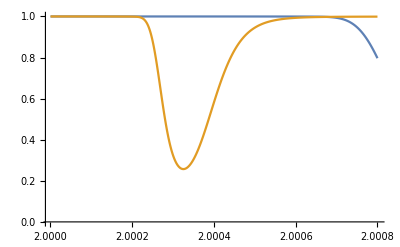

```mathematica
ListPlot[Lev3DoppTestsc[50,50/1000,1/1000,0*10^6,2*10^9,4] ,Joined->True,PlotRange->All]
```

```mathematica
g={};
Do[
model=a/(((b-f)/c)^2+d);
data=Transpose[{Lev4DoppTestsc[50,P/1000,1/1000,0.5*10^6,6*10^9,0][[All,1]],1-Lev4DoppTestsc[50,P/1000,1/1000,0.5*10^6,6*10^9,0][[All,2]]}];
result=NonlinearModelFit[data,model,{{a,0.014},{b,6},{c,0.0001},{d,1}},f,MaxIterations->500,Method->{NMinimize}];
g=Append[g,{P,result["BestFitParameters"][[{1,3},2]]}];
,{P,0,300,1}]
```

General::nomem: The current computation was aborted because there was insufficient memory available to complete the computation.

Throw::sysexc: Uncaught SystemException returned to top level. Can be caught with Catch[…, _SystemException].

SystemException[MemoryAllocationFailure]

```mathematica
g
```

{{0,{0.322108,-0.0591253}},{1,{0.0785752,-0.424466}},{2,{0.821773,0.215049}},{3,{0.0545518,0.000146463}},{4,{0.0142429,0.000327932}},{5,{0.088265,0.00014646}},{6,{0.00990484,0.000477209}},{7,{0.0116786,0.000473441}},{8,{0.0115297,0.000508392}},{9,{0.157551,0.000145649}},{10,{0.0254698,0.000381381}},{11,{0.110251,0.000192061}},{12,{0.00873036,0.000712314}},{13,{0.00924545,0.000719947}},{14,{0.0133938,0.000620361}},{15,{0.0246134,0.000473455}},{16,{0.0318814,0.000429448}},{17,{0.0115514,0.000735129}},{18,{0.30924,0.000146151}},{19,{0.022703,-0.000554018}},{20,{0.0155346,0.000686979}},{21,{0.504872,0.000123436}},{22,{0.00977143,0.000908035}},{23,{0.269702,0.000176677}},{24,{0.415332,0.000145406}},{25,{0.0310764,-0.000542502}},{26,{0.211523,0.000212013}},{27,{0.554143,0.000133492}},{28,{0.139952,0.000270431}},{29,{0.397206,0.000163336}},{30,{0.420223,0.000160112}},{31,{0.040378,0.000529589}},{32,{0.402504,0.000170403}},{33,{0.0156021,0.000878886}},{34,{0.0191529,0.000805119}},{35,{0.0515383,-0.000497962}},{36,{0.0901612,0.000381789}},{37,{0.0176072,0.000875813}},{38,{0.464521,0.000172793}},{39,{0.219014,0.00025493}},{40,{0.460109,0.000178113}},{41,{0.0296208,0.000710719}},{42,{0.029336,0.000722804}},{43,{0.109827,0.000377983}},{44,{0.0143679,0.00105707}},{45,{0.551781,0.000172493}},{46,{0.0313266,0.000731966}},{47,{0.0137516,0.00111671}},{48,{0.765312,0.000151086}},{49,{4.68989×10^16,2.07175×10^13}},{50,{9.0384×10^29,-5.14308×10^27}},{51,{9.0384×10^29,-5.14308×10^27}}}

```mathematica
data=Uncompress[FromCharacterCode[Flatten[ImageData[Import["http://i.stack.imgur.com/RZcpj.png"],"Byte"]]]];
smoothed=MedianFilter[data,5];
Show[ListPlot[data],ListPlot[smoothed,PlotStyle->Green]]
```

```mathematica
Lev4DoppTestsc[50,50/1000,1/1000,0*10^6,6*10^9,0]
```

3.20734×10^8

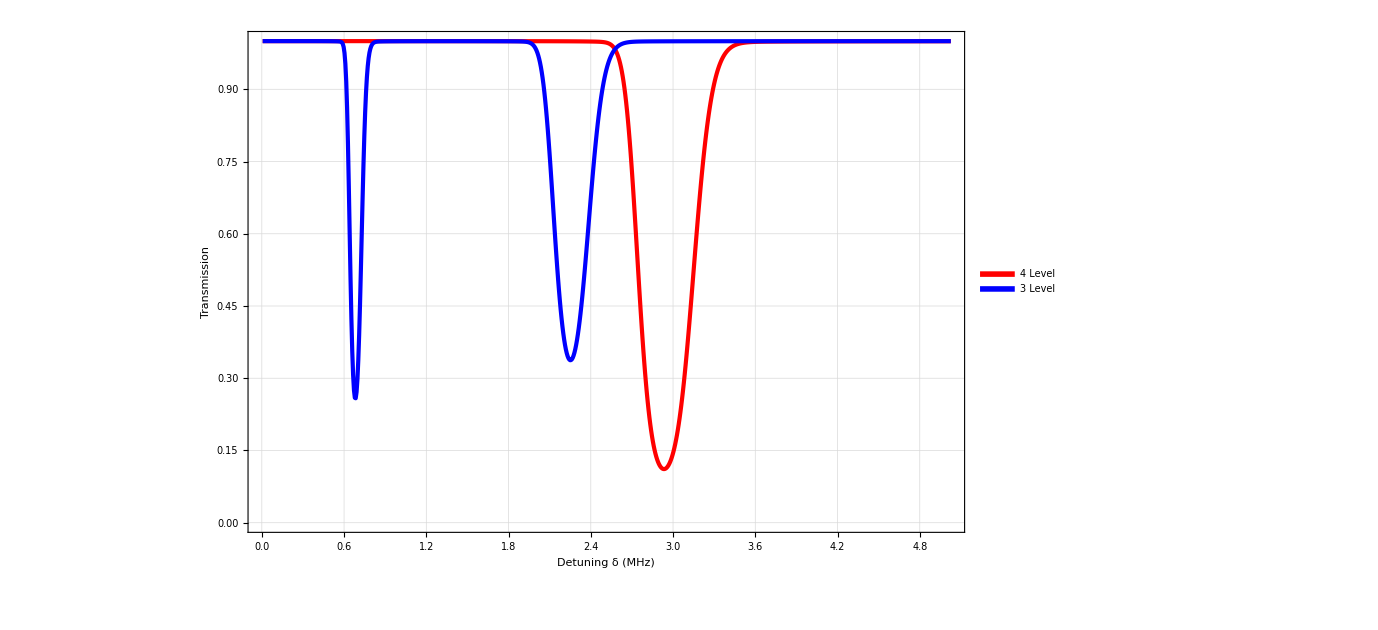

```mathematica
legend=LineLegend[Thread[Directive[{Red,Blue},AbsoluteThickness[10]]],{Style["4 Level",Red],Style["3 Level",Blue]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->50}];
final4=ListPlot[{Lev4DoppTestsc[50,50/1000,1/1000,0*10^6,6*10^9,0],Lev3DoppTestsc[50,50/1000,1/1000,0*10^6,6*10^9,0]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,Top}],ImageSize->1020,PlotStyle->{{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Blue}},FrameLabel->{Style["Detuning δ (MHz)",50,Black],Style["Transmission ",50,Black]},GridLines->Automatic,PlotRange->{0,1}]
```

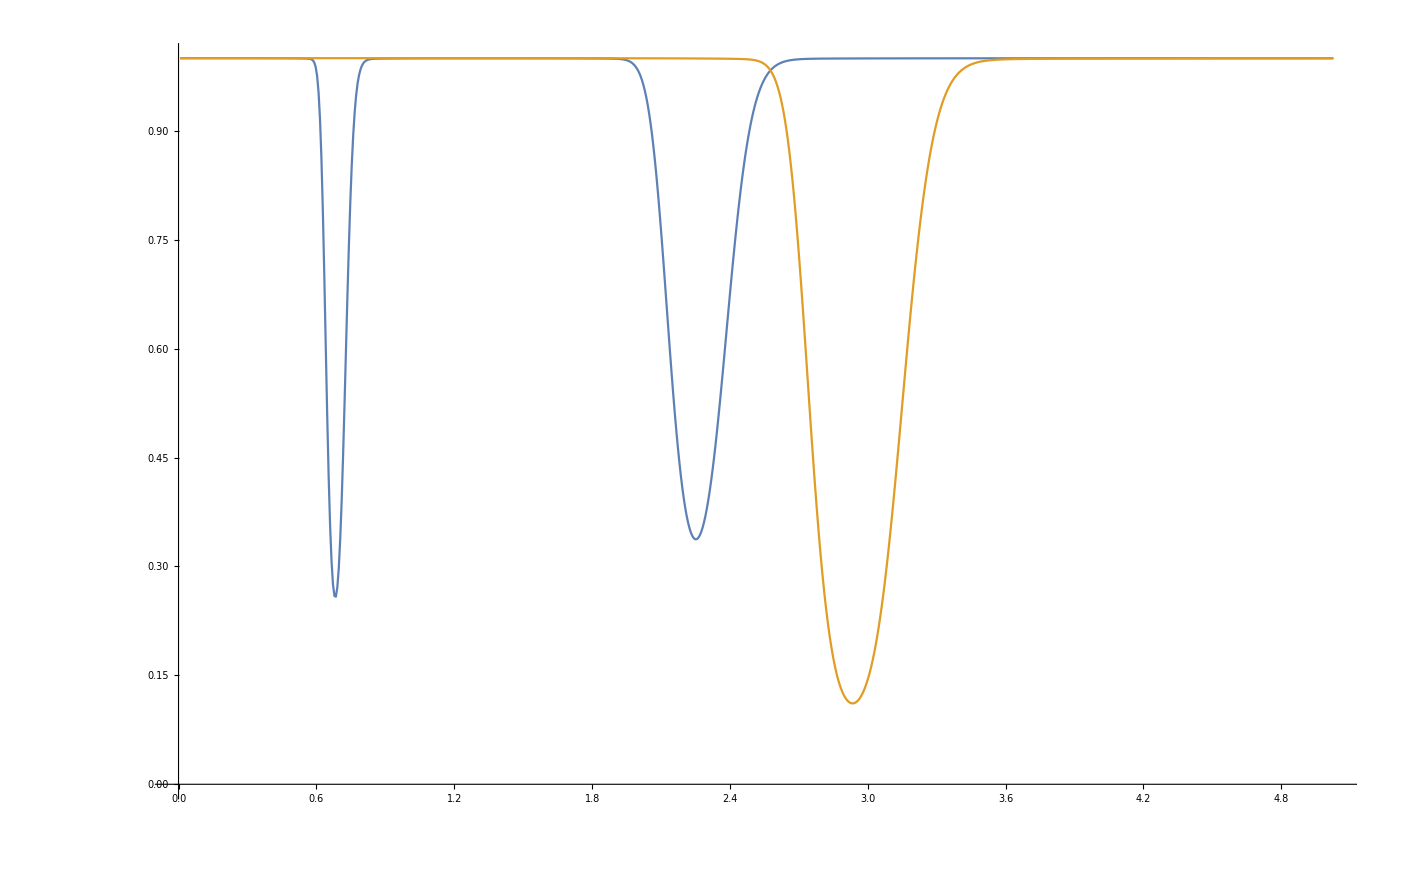

```mathematica
ListPlot[{Lev3DoppTestsc[50,50/1000,1/1000,0*10^6,6*10^9,0],Lev4DoppTestsc[50,50/1000,1/1000,0*10^6,6*10^9,0]},PlotRange->All,Joined->True]
```

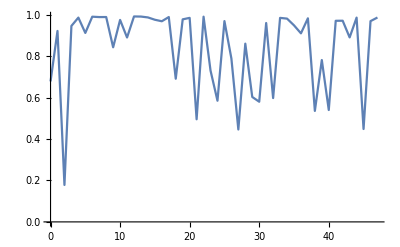

```mathematica
ListPlot[Take[Transpose[{g[[All,1]],1-g[[All,2,1]]}],48],Joined->True,PlotRange->All]
```

# end

```mathematica
g1={};
Do[
model=a/(((b-f)/c)^2+d);
data=Transpose[{Lev3DoppTestsc[50,P/1000,1/1000,0.5*10^6,6*10^9,0][[All,1]],1-Lev4DoppTestsc[50,P/1000,1/1000,0.5*10^6,6*10^9,0][[All,2]]}];
result=NonlinearModelFit[data,model,{{a,0.014},{b,6},{c,0.0001},{d,1}},f,MaxIterations->500,Method->{NMinimize}];
g1=Append[g1,{P,result["BestFitParameters"][[{1,3},2]]}];
,{P,0,300,1}]
```

General::nomem: The current computation was aborted because there was insufficient memory available to complete the computation.

Throw::sysexc: Uncaught SystemException returned to top level. Can be caught with Catch[…, _SystemException].

SystemException[MemoryAllocationFailure]

```mathematica
g1[[All,2]]
```

{{0.322108,-0.0591253},{0.088265,0.00014646},{0.0254698,0.000381381},{0.0246134,0.000473455},{0.0155346,0.000686979}}

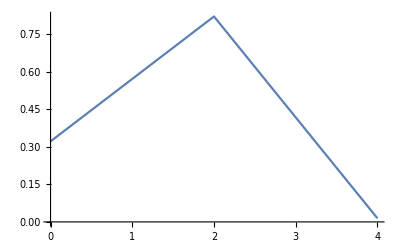

```mathematica
ListPlot[Transpose[{g1[[All,1]],g1[[All,2,1]]}],Joined->True,PlotRange->All]
```

```mathematica
Off[Power::infy]
Off[Infinity::indet]
```

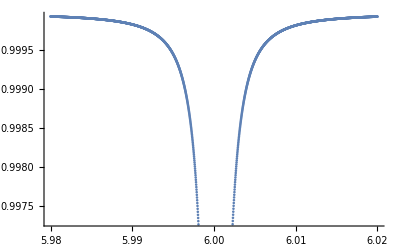

```mathematica
ListPlot[Transpose[{Lev4DoppTestsc[50,20/1000,1/1000,1*10^6,6*10^9,0][[All,1]],Lev4DoppTestsc[50,20/1000,1/1000,1*10^6,6*10^9,0][[All,2]]}]]
```

```mathematica
g3={};
Do[
model=a/(((b-f)/c)^2+d);
data=Transpose[{Lev4DoppTestsc[50,20/1000,1/1000,γ*10^6,6*10^9,0][[All,1]],1-Lev4DoppTestsc[50,20/1000,1/1000,γ*10^6,6*10^9,0][[All,2]]}];
result=NonlinearModelFit[data,model,{{a,0.014},{b,6},{c,0.0001},{d,1}},f,MaxIterations->500,Method->{NMinimize}];
g3=Append[g3,{P,result["BestFitParameters"][[{1,3},2]]}];
,{γ,0.05,10,0.05}]
```

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

NonlinearModelFit::nrnum: The function value Overflow[] is not a real number at {a,b,c,d} = {0.014,6.,0.0001,1.}.

NMinimize::nnum: The function value Experimental`NumericalFunction[«1»][{0.014,6.,0.0001,1.}] is not a number at {a,b,c,d} = {0.014,6.,0.0001,1.}.

NonlinearModelFit::nrnum: The function value Overflow[] is not a real number at {a,b,c,d} = {0.014,6.,0.0001,1.}.

NMinimize::nnum: The function value Experimental`NumericalFunction[«1»][{0.014,6.,0.0001,1.}] is not a number at {a,b,c,d} = {0.014,6.,0.0001,1.}.

NonlinearModelFit::nrnum: The function value Overflow[] is not a real number at {a,b,c,d} = {0.014,6.,0.0001,1.}.

General::stop: Further output of NonlinearModelFit::nrnum will be suppressed during this calculation.

NMinimize::nnum: The function value Experimental`NumericalFunction[«1»][{0.014,6.,0.0001,1.}] is not a number at {a,b,c,d} = {0.014,6.,0.0001,1.}.

General::stop: Further output of NMinimize::nnum will be suppressed during this calculation.

Part::partd: Part specification … is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

```mathematica
g4={};
Do[
model=a/(((b-f)/c)^2+d);
data=Transpose[{Lev3DoppTestsc[50,20/1000,1/1000,γ*10^6,6*10^9,0][[All,1]],1-Lev4DoppTestsc[50,20/1000,1/1000,γ*10^6,6*10^9,0][[All,2]]}];
result=NonlinearModelFit[data,model,{{a,0.014},{b,6},{c,0.0001},{d,1}},f,MaxIterations->500,Method->{NMinimize}];
g4=Append[g4,{P,result["BestFitParameters"][[{1,3},2]]}];
,{γ,0,10,0.05}]
```

NonlinearModelFit::nrnum: The function value Indeterminate is not a real number at {a,b,c,d} = {0.014,6.,0.0001,1.}.

NMinimize::nnum: The function value Experimental`NumericalFunction[{Hold[Block[{f={5.98,5.98002,5.98004,5.98006,5.98008,5.9801,5.98012,5.98014,5.98016,5.98018,5.9802,5.98022,5.98024,5.98026,5.98028,5.9803,5.98032,5.98034,5.98036,5.98038,5.9804,5.98042,5.98044,5.98046,5.98048,5.9805,5.98052,5.98054,5.98056,5.98058,5.9806,5.98062,5.98064,5.98066,5.98068,5.9807,5.98072,5.98074,5.98076,5.98078,5.9808,5.98082,5.98084,5.98086,5.98088,5.9809,5.98092,5.98094,5.98096,5.98098,«1951»},Optimization`FindFit`y$193088={0.0000407859,0.000040785,0.000040784,0.0000407831,0.0000407822,0.0000407812,0.0000407803,0.0000407794,0.0000407784,0.0000407775,0.0000407766,0.0000407756,0.0000407747,0.0000407737,0.0000407728,0.0000407718,0.0000407709,0.0000407699,0.000040769,«14»,0.0000407545,0.0000407536,0.0000407526,0.0000407516,0.0000407506,0.0000407497,0.0000407487,0.0000407477,0.0000407467,0.0000407457,0.0000407447,0.0000407438,0.0000407428,0.0000407418,0.0000407408,0.0000407398,0.0000407388,«1951»}},1/2 («1»).(«1»)]],Block},«5»][{«1»}] is not a number at {a,b,c,d} = {0.014,6.,0.0001,1.}.

NonlinearModelFit::nrnum: The function value Indeterminate is not a real number at {a,b,c,d} = {0.014,6.,0.0001,1.}.

NMinimize::nnum: The function value Experimental`NumericalFunction[{Hold[Block[{f={5.98,5.98002,5.98004,5.98006,5.98008,5.9801,5.98012,5.98014,5.98016,5.98018,5.9802,5.98022,5.98024,5.98026,5.98028,5.9803,5.98032,5.98034,5.98036,5.98038,5.9804,5.98042,5.98044,5.98046,5.98048,5.9805,5.98052,5.98054,5.98056,5.98058,5.9806,5.98062,5.98064,5.98066,5.98068,5.9807,5.98072,5.98074,5.98076,5.98078,5.9808,5.98082,5.98084,5.98086,5.98088,5.9809,5.98092,5.98094,5.98096,5.98098,«1951»},Optimization`FindFit`y$193088={0.0000407859,0.000040785,0.000040784,0.0000407831,0.0000407822,0.0000407812,0.0000407803,0.0000407794,0.0000407784,0.0000407775,0.0000407766,0.0000407756,0.0000407747,0.0000407737,0.0000407728,0.0000407718,0.0000407709,0.0000407699,0.000040769,«14»,0.0000407545,0.0000407536,0.0000407526,0.0000407516,0.0000407506,0.0000407497,0.0000407487,0.0000407477,0.0000407467,0.0000407457,0.0000407447,0.0000407438,0.0000407428,0.0000407418,0.0000407408,0.0000407398,0.0000407388,«1951»}},1/2 («1»).(«1»)]],Block},«5»][{«1»}] is not a number at {a,b,c,d} = {0.014,6.,0.0001,1.}.

NonlinearModelFit::nrnum: The function value Indeterminate is not a real number at {a,b,c,d} = {0.014,6.,0.0001,1.}.

General::stop: Further output of NonlinearModelFit::nrnum will be suppressed during this calculation.

NMinimize::nnum: The function value Experimental`NumericalFunction[{Hold[Block[{f={5.98,5.98002,5.98004,5.98006,5.98008,5.9801,5.98012,5.98014,5.98016,5.98018,5.9802,5.98022,5.98024,5.98026,5.98028,5.9803,5.98032,5.98034,5.98036,5.98038,5.9804,5.98042,5.98044,5.98046,5.98048,5.9805,5.98052,5.98054,5.98056,5.98058,5.9806,5.98062,5.98064,5.98066,5.98068,5.9807,5.98072,5.98074,5.98076,5.98078,5.9808,5.98082,5.98084,5.98086,5.98088,5.9809,5.98092,5.98094,5.98096,5.98098,«1951»},Optimization`FindFit`y$193088={0.0000407859,0.000040785,0.000040784,0.0000407831,0.0000407822,0.0000407812,0.0000407803,0.0000407794,0.0000407784,0.0000407775,0.0000407766,0.0000407756,0.0000407747,0.0000407737,0.0000407728,0.0000407718,0.0000407709,0.0000407699,0.000040769,«14»,0.0000407545,0.0000407536,0.0000407526,0.0000407516,0.0000407506,0.0000407497,0.0000407487,0.0000407477,0.0000407467,0.0000407457,0.0000407447,0.0000407438,0.0000407428,0.0000407418,0.0000407408,0.0000407398,0.0000407388,«1951»}},1/2 («1»).(«1»)]],Block},«5»][{«1»}] is not a number at {a,b,c,d} = {0.014,6.,0.0001,1.}.

General::stop: Further output of NMinimize::nnum will be suppressed during this calculation.

Part::partd: Part specification … is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

```mathematica
Manipulate[ListPlot[

{Lev4DoppTestsc[50,5/1000,1/1000,0.5*10^6,δ*10^9,0],
Lev3DoppTestsc[50,5/1000,1/1000,0.5*10^6,δ*10^9,0]},PlotRange->All,Joined->True,PlotLegends->{"4LEvel","3Level"}],{{δ,6},5.95,6}]
```

## Transmission by detuning Δ1 and Δ2

```mathematica
Manipulate[
c1=Lev4DoppTestsc[50,50/1000,1/1000,γ*10^6,δ*10^6,1];
c2=Lev3DoppTestsc[50,50/1000,1/1000,γ*10^6,δ*10^6,1];
c3=Lev4Testsc[50,50/1000,1/1000,γ*10^6,δ*10^6,1];
c4=Lev3Testsc[50,50/1000,1/1000,γ*10^6,δ*10^6,1];
c5=Lev4DoppTestsc[50,50/1000,1/1000,γ*10^6,δ*10^6,0];
c6=Lev3DoppTestsc[50,50/1000,1/1000,γ*10^6,δ*10^6,0];
c7=Lev4Testsc[50,50/1000,1/1000,γ*10^6,δ*10^6,0];
c8=Lev3Testsc[50,50/1000,1/1000,γ*10^6,δ*10^6,0];
(*Show[ListPlot[a1,Joined->True,ImageSize->1020,Frame->True,Axes->False,PlotRange->{0,1}],ListPlot[a2,PlotStyle->Black,Joined->True,Frame->True,Axes->False],ListPlot[a3,Joined->True,ImageSize->1020,Frame->True,Axes->False,PlotRange->All,PlotStyle->{Darker[Red],Dashed}],ListPlot[a4,PlotStyle->{Red,Dashed},Joined->True,Frame->True,Axes->False,PlotRange->All]]
*)
Off[Mean::rectt];
Off[Part::pkspec1];
Off[Set::pkspec1];
Off[ListPlot::prng];
GraphicsGrid[
{{ListPlot[c3,Joined->True,Frame->True,Axes->False,PlotRange->{0,1.5},ImageSize->500],
ListPlot[c1,Joined->True,Frame->True,Axes->False,PlotRange->{0,1.5},ImageSize->500],ListPlot[c7,Joined->True,Frame->True,Axes->False,ImageSize->500,PlotRange->{0,1.1},GridLines->Automatic],ListPlot[c5,Joined->True,Frame->True,Axes->False,ImageSize->500,PlotRange->{0,1.1},GridLines->Automatic]},
{ListPlot[c4,Joined->True,Frame->True,Axes->False,PlotRange->{0,1.5},ImageSize->500],
ListPlot[c2,Joined->True,Frame->True,Axes->False,PlotRange->{0,1.5},ImageSize->500],ListPlot[c8,Joined->True,Frame->True,Axes->False,ImageSize->500,PlotRange->{0,1.1},GridLines->Automatic],ListPlot[c6,Joined->True,Frame->True,Axes->False,ImageSize->500,PlotRange->{0,1.1},GridLines->Automatic]}
},ImageSize->1500]
,{γ,0,100},{δ,-500,500}]
```

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

# Seperation vs transmission

Module

```mathematica
Lev4DoppTestscSep[T_,P_,diam_,gam_,delt_,kia_,ab_,Sep_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Δ2,d31,d41},
d=(kia+Range[-0.01,0.01,0.00005])*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(Sep*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

If[ab==0,
(*{Transpose[{d/10^9,Im[sd24[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd23[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}],
Transpose[{d/10^9,Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}]
}*)

(*Re[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Re[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]*)
Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]

,
(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}]*)
{Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]])]
}]}
]
]
```

```mathematica
Lev3DoppTestscSep[T_,P_,diam_,gam_,delt_,kia_,ab_,sep_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},

d=(kia+Range[-0.01,0.01,0.00005])*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(sep*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 
If[ab==0,
(*{Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
}*)
(*Re[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Re[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]*)
Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]

,
(*
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}],*)
{
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]])]}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
}
]]
```

P=0

```mathematica
Clear[γvT3,γvT4]
```

```mathematica
Manipulate[GraphicsRow[{ListPlot[Lev3DoppTestscSep[55,1/1000,1/1000,0*10^6,0,0,3,i*1000],PlotRange->{0,1.8},Joined->True],ListPlot[Lev4DoppTestscSep[55,1/1000,1/1000,0*10^6,0,0,3,i*1000],PlotRange->{0,1.8},Joined->True]},ImageSize->1000],{i,0,3}]
```

ListPlot::lpn: Null is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

```mathematica
Off[Power::infy]
Off[Infinity::indet]
```

```mathematica
Manipulate[ListPlot[{Lev4DoppTestscSep[55,P/1000,1/1000,0*10^6,0,0,0,i*1000],Lev3DoppTestscSep[55,P/1000,1/1000,0*10^6,0,0,0,i*1000],Lev3DoppTestscSep[55,0/1000,1/1000,0*10^6,0,0,0,i*1000]},PlotLegends->{"4Level","3Level","WIthout EIT"},Axes->False,Frame->True,FrameLabel->{Style["-10MHz to +10 MHz",20,Black],Style["Im[χ] Absorption",20,Black]},FrameTicks->{False,True},Joined->True,ImageSize->1020,PlotRange->{0,0.00005}],{{i,0,"Seperation(GHz)"},0,5},{P,5,50}]
```

```mathematica
(*Range[-0.3,0.1,0.001]*)
max3=Mean[GaussianFilter[DeleteCases[Select[Lev3DoppTestscSep[50,0/1000,1/1000,0*10^6,0,0,0],-10^-10≤ #&&#∈Reals&],Indeterminate],5]];
max4=Mean[GaussianFilter[DeleteCases[Select[Lev4DoppTestscSep[50,0/1000,1/1000,0*10^6,0,0,0],-10^-10≤ #&&#∈Reals&],Indeterminate],6]];
γvT3[P_]:=γvT3[P]=Table[{k,1-Min[Select[MedianFilter[Select[Lev3DoppTestscSep[50,P/1000,1/1000,k*10^6,0,0,0],-10^-10≤ #&&#∈Reals&],5],#≥0&]]/max3},{k,0,10,0.2}];
γvT4[P_]:=γvT4[P]=Table[{k,1-Min[Select[MedianFilter[Select[Lev4DoppTestscSep[50,P/1000,1/1000,k*10^6,0,0,0],-10^-10≤ #&&#∈Reals&],5],1>#≥0&]]/max4},{k,0,10,0.2}];
```

```mathematica
fil[list_]:=Select[list,-10^-10≤ #&&#∈Reals&]
```

```mathematica
Manipulate[ListPlot[{fil[Lev4DoppTestscSep[4,5/1000,1/1000,0*10^6,0,0,0,i*1000]],fil[Lev3DoppTestscSep[4,5/1000,1/1000,0*10^6,0,0,0,i*1000]],fil[Lev3DoppTestscSep[4,0/1000,1/1000,0*10^6,0,0,0,i*1000]]},PlotLegends->{"4Level","3Level","WIthout EIT"},Axes->False,Frame->True,FrameLabel->{Style["-10MHz to +10 MHz",20,Black],Style["Im[χ] Absorption",20,Black]},FrameTicks->{False,True},Joined->True,ImageSize->1020,PlotRange->{0,0.000001}],{{i,0,"Seperation(GHz)"},0,5}]
```

# Temp =100 ~ 560MHz

```mathematica
max3[i_]:=Mean[fil[Lev3DoppTestscSep[100,0/1000,1/1000,0*10^6,0,0,0,i*1000]]];
max4[i_]:=Mean[fil[Lev4DoppTestscSep[100,0/1000,1/1000,0*10^6,0,0,0,i*1000]]];
TvS3[P_]:=Table[{i,1-Min[fil[Lev3DoppTestscSep[100,P/1000,1/1000,0*10^6,0,0,0,i*1000]]]/max3[i]},{i,0,2,0.1}];
TvS4[P_]:= Table[{i,1-Min[fil[Lev4DoppTestscSep[100,P/1000,1/1000,0*10^6,0,0,0,i*1000]]]/max4[i]},{i,0,2,0.1}];
```

P=5

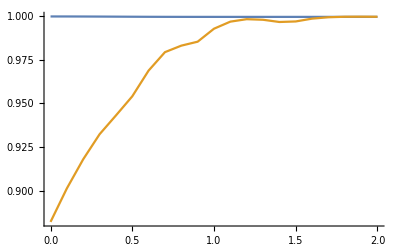

```mathematica
ListPlot[{TvS3[5],TvS4[5]},Joined->True,PlotRange->All]
```

P=10

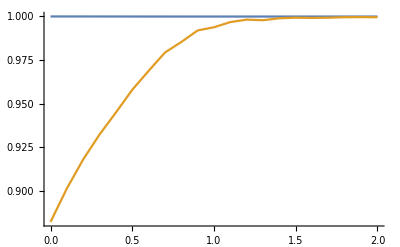

```mathematica
ListPlot[{TvS3[10],TvS4[10]},Joined->True,PlotRange->All]
```

P=15

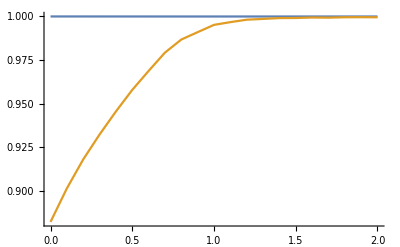

```mathematica
ListPlot[{TvS3[15],TvS4[15]},Joined->True,PlotRange->All]
```

P=20

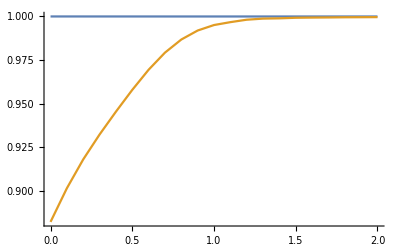

```mathematica
ListPlot[{TvS3[20],TvS4[20]},Joined->True,PlotRange->All]
```

P=30

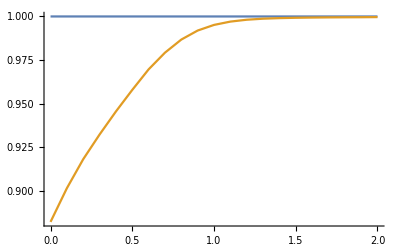

```mathematica
ListPlot[{TvS3[30],TvS4[30]},Joined->True,PlotRange->All]
```

P=40

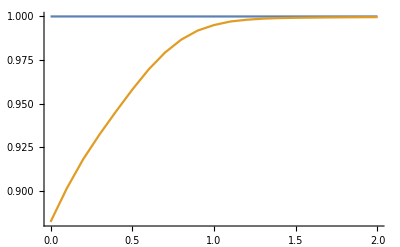

```mathematica
ListPlot[{TvS3[40],TvS4[40]},Joined->True,PlotRange->All]
```

P=50

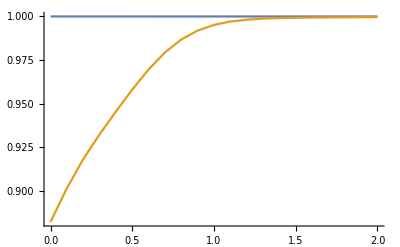

```mathematica
ListPlot[{TvS3[50],TvS4[50]},Joined->True,PlotRange->All]
```

```mathematica
Rbpress[55][[2]]*10^-9
```

0.530972

# Temp =55 ~ 530MHz

```mathematica
max3[i_]:=Mean[fil[Lev3DoppTestscSep[55,0/1000,1/1000,0*10^6,0,0,0,i*1000]]];
max4[i_]:=Mean[fil[Lev4DoppTestscSep[55,0/1000,1/1000,0*10^6,0,0,0,i*1000]]];
TvS3[P_]:=Table[{i,1-Min[fil[Lev3DoppTestscSep[55,P/1000,1/1000,0*10^6,0,0,0,i*1000]]]/max3[i]},{i,0,2,0.1}];
TvS4[P_]:= Table[{i,1-Min[fil[Lev4DoppTestscSep[55,P/1000,1/1000,0*10^6,0,0,0,i*1000]]]/max4[i]},{i,0,2,0.1}];
```

P=5

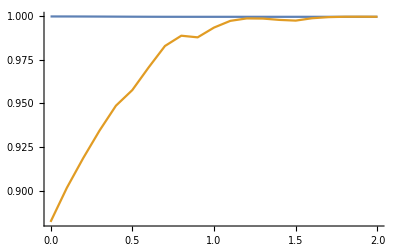

```mathematica
ListPlot[{TvS3[5],TvS4[5]},Joined->True,PlotRange->All]
```

P=10

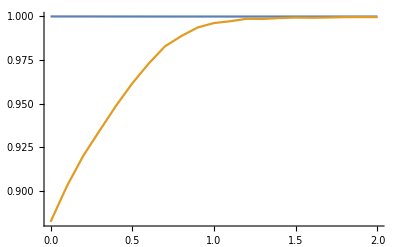

```mathematica
ListPlot[{TvS3[10],TvS4[10]},Joined->True,PlotRange->All]
```

P=15

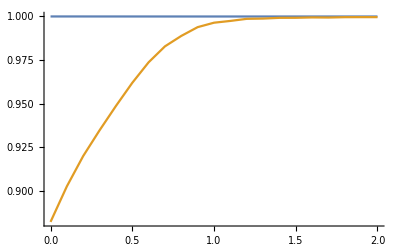

```mathematica
ListPlot[{TvS3[15],TvS4[15]},Joined->True,PlotRange->All]
```

P=20

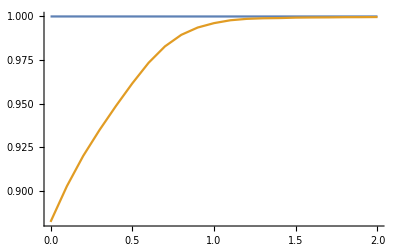

```mathematica
ListPlot[{TvS3[20],TvS4[20]},Joined->True,PlotRange->All]
```

P=30

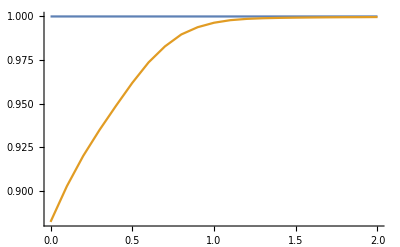

```mathematica
ListPlot[{TvS3[30],TvS4[30]},Joined->True,PlotRange->All]
```

P=40

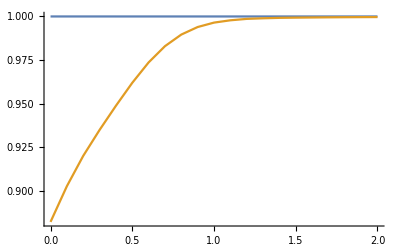

```mathematica
ListPlot[{TvS3[40],TvS4[40]},Joined->True,PlotRange->All]
```

P=50

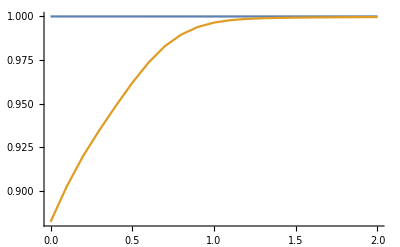

```mathematica
ListPlot[{TvS3[50],TvS4[50]},Joined->True,PlotRange->All]
```

```mathematica
Rbpress[55][[2]]*10^-9
```

0.530972

```mathematica
baom={TvS4[5],TvS4[15],TvS4[25],TvS4[50],TvS4[100]};
```

```mathematica
baom
```

{{{0.,0.882257},{0.1,0.901777},{0.2,0.918754},{0.3,0.934518},{0.4,0.948699},{0.5,0.957607},{0.6,0.970573},{0.7,0.982846},{0.8,0.988722},{0.9,0.987788},{1.,0.993374},{1.1,0.997218},{1.2,0.998612},{1.3,0.998524},{1.4,0.997762},{1.5,0.997357},{1.6,0.998715},{1.7,0.999345},{1.8,0.999563},{1.9,0.999588},{2.,0.999548}},{{0.,0.882272},{0.1,0.90266},{0.2,0.92005},{0.3,0.934752},{0.4,0.948683},{0.5,0.961939},{0.6,0.973713},{0.7,0.982846},{0.8,0.988833},{0.9,0.99385},{1.,0.996397},{1.1,0.997412},{1.2,0.998611},{1.3,0.998759},{1.4,0.999184},{1.5,0.99921},{1.6,0.99942},{1.7,0.999356},{1.8,0.999563},{1.9,0.999588},{2.,0.999586}},{{0.,0.882273},{0.1,0.902716},{0.2,0.920133},{0.3,0.93502},{0.4,0.948668},{0.5,0.961975},{0.6,0.973599},{0.7,0.982846},{0.8,0.98965},{0.9,0.993955},{1.,0.996481},{1.1,0.997877},{1.2,0.99861},{1.3,0.998987},{1.4,0.99919},{1.5,0.999305},{1.6,0.999367},{1.7,0.999494},{1.8,0.999563},{1.9,0.999588},{2.,0.999665}},{{0.,0.882273},{0.1,0.902742},{0.2,0.920144},{0.3,0.935015},{0.4,0.948831},{0.5,0.961962},{0.6,0.973644},{0.7,0.983017},{0.8,0.989641},{0.9,0.993944},{1.,0.996473},{1.1,0.997871},{1.2,0.998607},{1.3,0.998986},{1.4,0.999189},{1.5,0.999316},{1.6,0.999427},{1.7,0.999494},{1.8,0.999563},{1.9,0.999619},{2.,0.999665}},{{0.,0.882273},{0.1,0.902773},{0.2,0.920167},{0.3,0.93501},{0.4,0.94881},{0.5,0.961935},{0.6,0.973636},{0.7,0.982987},{0.8,0.989626},{0.9,0.993923},{1.,0.996456},{1.1,0.997861},{1.2,0.998602},{1.3,0.998983},{1.4,0.999189},{1.5,0.999328},{1.6,0.999426},{1.7,0.999503},{1.8,0.999564},{1.9,0.999619},{2.,0.999665}}}

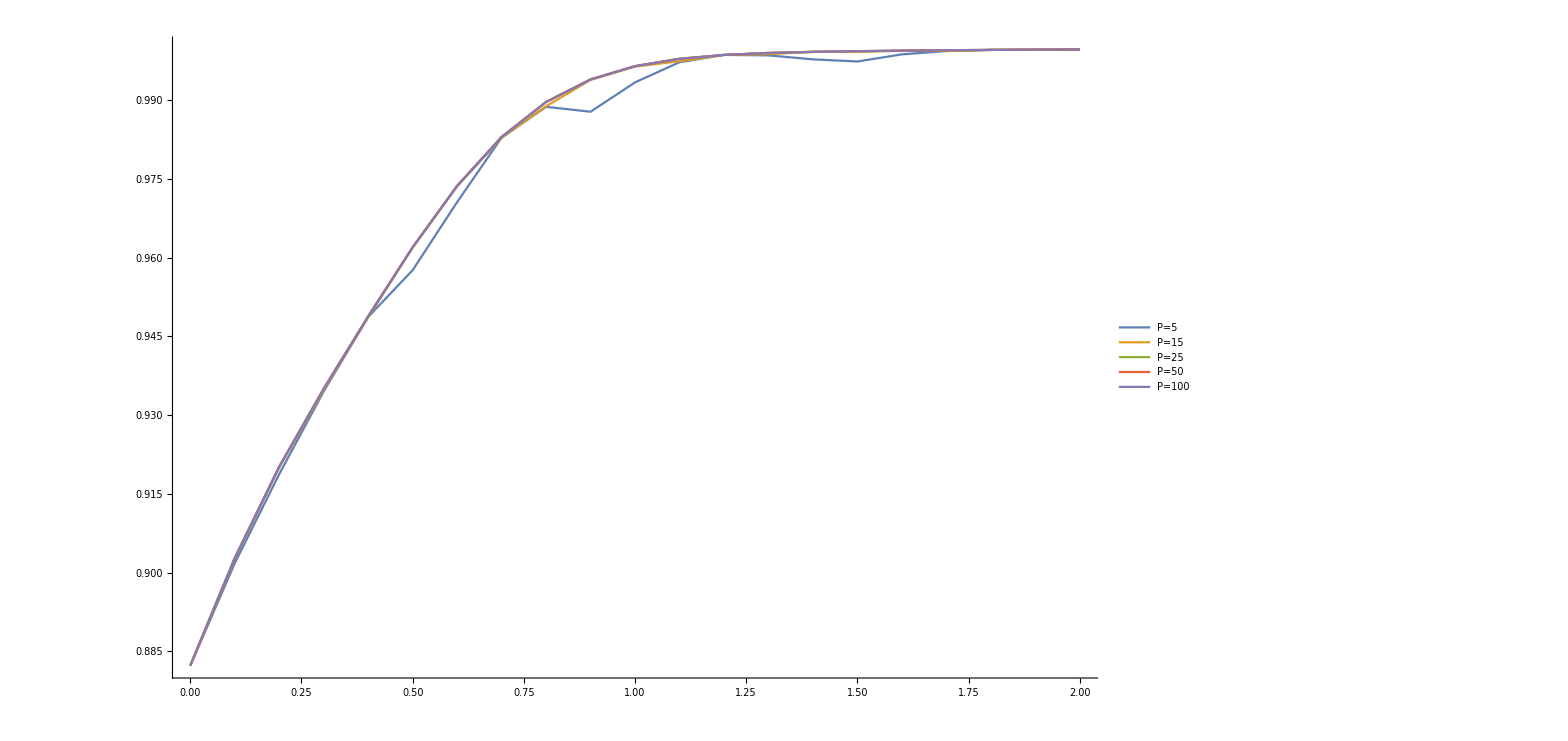

```mathematica
ListPlot[baom
,PlotLegends->{"P=5","P=15","P=25","P=50","P=100"},ImageSize->1200,Joined->True
]
```

## Temp compare

```mathematica
max3[i_]:=Mean[fil[Lev3DoppTestscSep[100,0/1000,1/1000,0*10^6,0,0,0,i*1000]]];max4[i_]:=Mean[fil[Lev4DoppTestscSep[100,0/1000,1/1000,0*10^6,0,0,0,i*1000]]];
a1={Table[{i,1-Min[fil[Lev3DoppTestscSep[100,50/1000,1/1000,0*10^6,0,0,0,i*1000]]]/max3[i]},{i,0,2,0.1}], Table[{i,1-Min[fil[Lev4DoppTestscSep[100,50/1000,1/1000,0*10^6,0,0,0,i*1000]]]/max4[i]},{i,0,2,0.05}]};
max3[i_]:=Mean[fil[Lev3DoppTestscSep[50,0/1000,1/1000,0*10^6,0,0,0,i*1000]]];max4[i_]:=Mean[fil[Lev4DoppTestscSep[50,0/1000,1/1000,0*10^6,0,0,0,i*1000]]];
a2={Table[{i,1-Min[fil[Lev3DoppTestscSep[50,50/1000,1/1000,0*10^6,0,0,0,i*1000]]]/max3[i]},{i,0,2,0.1}], Table[{i,1-Min[fil[Lev4DoppTestscSep[50,50/1000,1/1000,0*10^6,0,0,0,i*1000]]]/max4[i]},{i,0,2,0.05}]};
max3[i_]:=Mean[fil[Lev3DoppTestscSep[20,0/1000,1/1000,0*10^6,0,0,0,i*1000]]];max4[i_]:=Mean[fil[Lev4DoppTestscSep[20,0/1000,1/1000,0*10^6,0,0,0,i*1000]]];
a3={Table[{i,1-Min[fil[Lev3DoppTestscSep[20,50/1000,1/1000,0*10^6,0,0,0,i*1000]]]/max3[i]},{i,0,2,0.1}], Table[{i,1-Min[fil[Lev4DoppTestscSep[20,50/1000,1/1000,0*10^6,0,0,0,i*1000]]]/max4[i]},{i,0,2,0.05}]};
```

```mathematica
max3[i_]:=Mean[fil[Lev3DoppTestscSep[200,0/1000,1/1000,0*10^6,0,0,0,i*1000]]];max4[i_]:=Mean[fil[Lev4DoppTestscSep[200,0/1000,1/1000,0*10^6,0,0,0,i*1000]]];
a4={Table[{i,1-Min[fil[Lev3DoppTestscSep[200,50/1000,1/1000,0*10^6,0,0,0,i*1000]]]/max3[i]},{i,0,2,0.1}], Table[{i,1-Min[fil[Lev4DoppTestscSep[200,50/1000,1/1000,0*10^6,0,0,0,i*1000]]]/max4[i]},{i,0,2,0.05}]};
max3[i_]:=Mean[fil[Lev3DoppTestscSep[400,0/1000,1/1000,0*10^6,0,0,0,i*1000]]];max4[i_]:=Mean[fil[Lev4DoppTestscSep[400,0/1000,1/1000,0*10^6,0,0,0,i*1000]]];
a5={Table[{i,1-Min[fil[Lev3DoppTestscSep[400,50/1000,1/1000,0*10^6,0,0,0,i*1000]]]/max3[i]},{i,0,2,0.1}], Table[{i,1-Min[fil[Lev4DoppTestscSep[400,50/1000,1/1000,0*10^6,0,0,0,i*1000]]]/max4[i]},{i,0,2,0.05}]};
```

```mathematica
max3[i_]:=Mean[fil[Lev3DoppTestscSep[-20,0/1000,1/1000,0*10^6,0,0,0,i*1000]]];max4[i_]:=Mean[fil[Lev4DoppTestscSep[-20,0/1000,1/1000,0*10^6,0,0,0,i*1000]]];
a6={Table[{i,1-Min[fil[Lev3DoppTestscSep[-20,50/1000,1/1000,0*10^6,0,0,0,i*1000]]]/max3[i]},{i,0,2,0.1}], Table[{i,1-Min[fil[Lev4DoppTestscSep[-20,50/1000,1/1000,0*10^6,0,0,0,i*1000]]]/max4[i]},{i,0,2,0.05}]};
max3[i_]:=Mean[fil[Lev3DoppTestscSep[-100,0/1000,1/1000,0*10^6,0,0,0,i*1000]]];max4[i_]:=Mean[fil[Lev4DoppTestscSep[-100,0/1000,1/1000,0*10^6,0,0,0,i*1000]]];
a7={Table[{i,1-Min[fil[Lev3DoppTestscSep[-100,50/1000,1/1000,0*10^6,0,0,0,i*1000]]]/max3[i]},{i,0,2,0.1}], Table[{i,1-Min[fil[Lev4DoppTestscSep[-100,50/1000,1/1000,0*10^6,0,0,0,i*1000]]]/max4[i]},{i,0,2,0.05}]};
```

```mathematica
max3[i_]:=Mean[fil[Lev3DoppTestscSep[-200,0/1000,1/1000,0*10^6,0,0,0,i*1000]]];max4[i_]:=Mean[fil[Lev4DoppTestscSep[-200,0/1000,1/1000,0*10^6,0,0,0,i*1000]]];
a8={Table[{i,1-Min[fil[Lev3DoppTestscSep[-20,50/1000,1/1000,0*10^6,0,0,0,i*1000]]]/max3[i]},{i,0,2,0.1}], Table[{i,1-Min[fil[Lev4DoppTestscSep[-200,50/1000,1/1000,0*10^6,0,0,0,i*1000]]]/max4[i]},{i,0,2,0.05}]};
```

```mathematica
max3[i_]:=Mean[fil[Lev3DoppTestscSep[-250,0/1000,1/1000,0*10^6,0,0,0,i*1000]]];max4[i_]:=Mean[fil[Lev4DoppTestscSep[-250,0/1000,1/1000,0*10^6,0,0,0,i*1000]]];
a9={Table[{i,1-Min[fil[Lev3DoppTestscSep[-250,50/1000,1/1000,0*10^6,0,0,0,i*1000]]]/max3[i]},{i,0,2,0.1}], Table[{i,1-Min[fil[Lev4DoppTestscSep[-250,50/1000,1/1000,0*10^6,0,0,0,i*1000]]]/max4[i]},{i,0,2,0.05}]};
```

```mathematica
Rbpress[50][[2]]*10^-9
Rbpress[20][[2]]*10^-9
Rbpress[100][[2]]*10^-9
Rbpress[200][[2]]*10^-9
Rbpress[400][[2]]*10^-9
Rbpress[-20][[2]]*10^-9
Rbpress[-100][[2]]*10^-9
Rbpress[-200][[2]]*10^-9
Rbpress[-250][[2]]*10^-9
```

0.526911

0.501857

0.566209

0.63758

0.760486

0.466363

0.385697

0.250693

0.14103

```mathematica
asdfdsaasddfadsasdfaasdfdssdfsdafsdfdsf
```

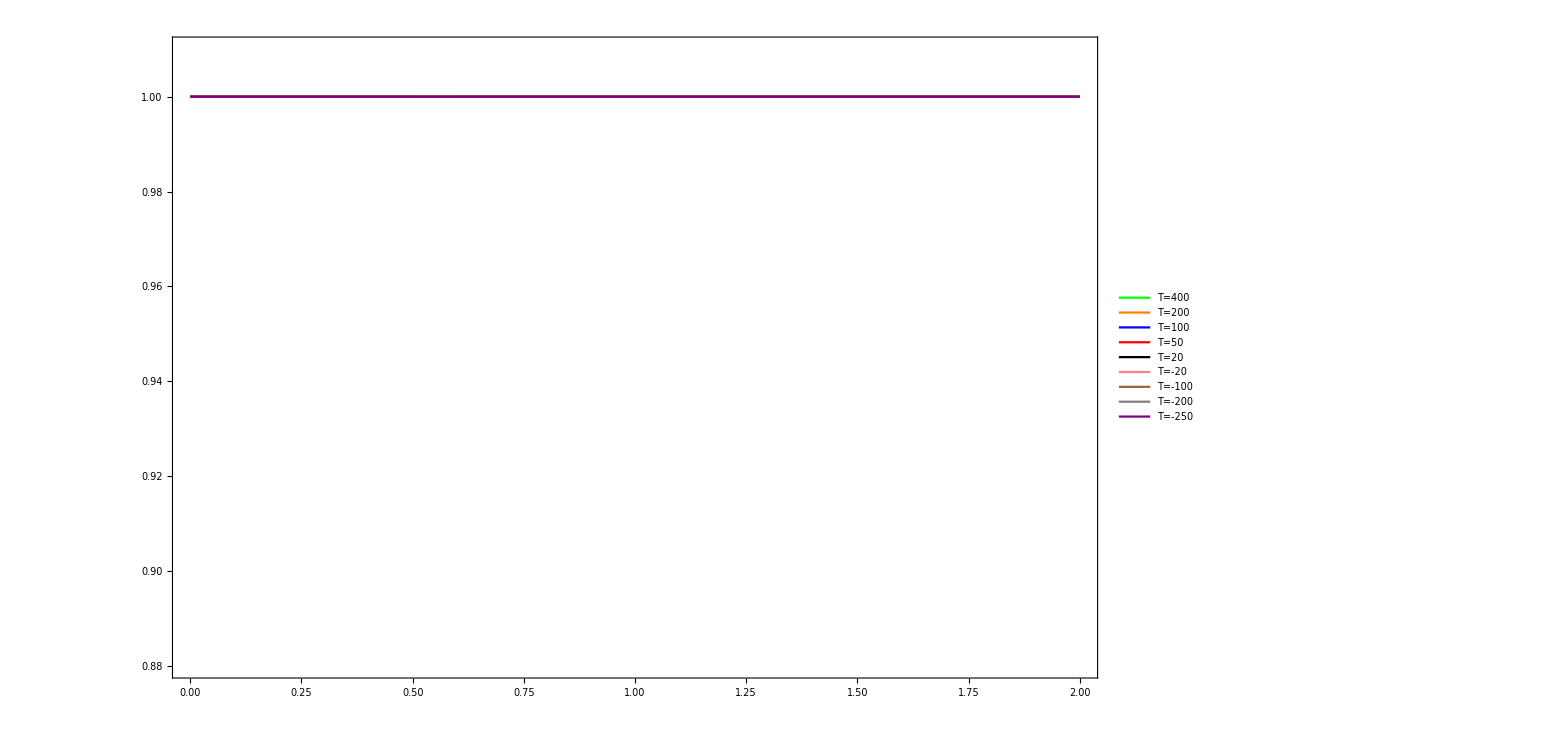

```mathematica
ListPlot[{a5[[1]],a4[[1]],a1[[1]],a2[[1]],a3[[1]],a6[[1]],a7[[1]],a8[[1]],a9[[1]]},PlotLegends->{"T=400","T=200","T=100","T=50","T=20","T=-20","T=-100","T=-200","T=-250"},ImageSize->1200,Joined->True,PlotStyle->{Green,Orange,Blue,Red,Black,Pink,Brown,Gray,Purple},PlotRange->{0.88,1.01},Frame->True,Axes->False]
```

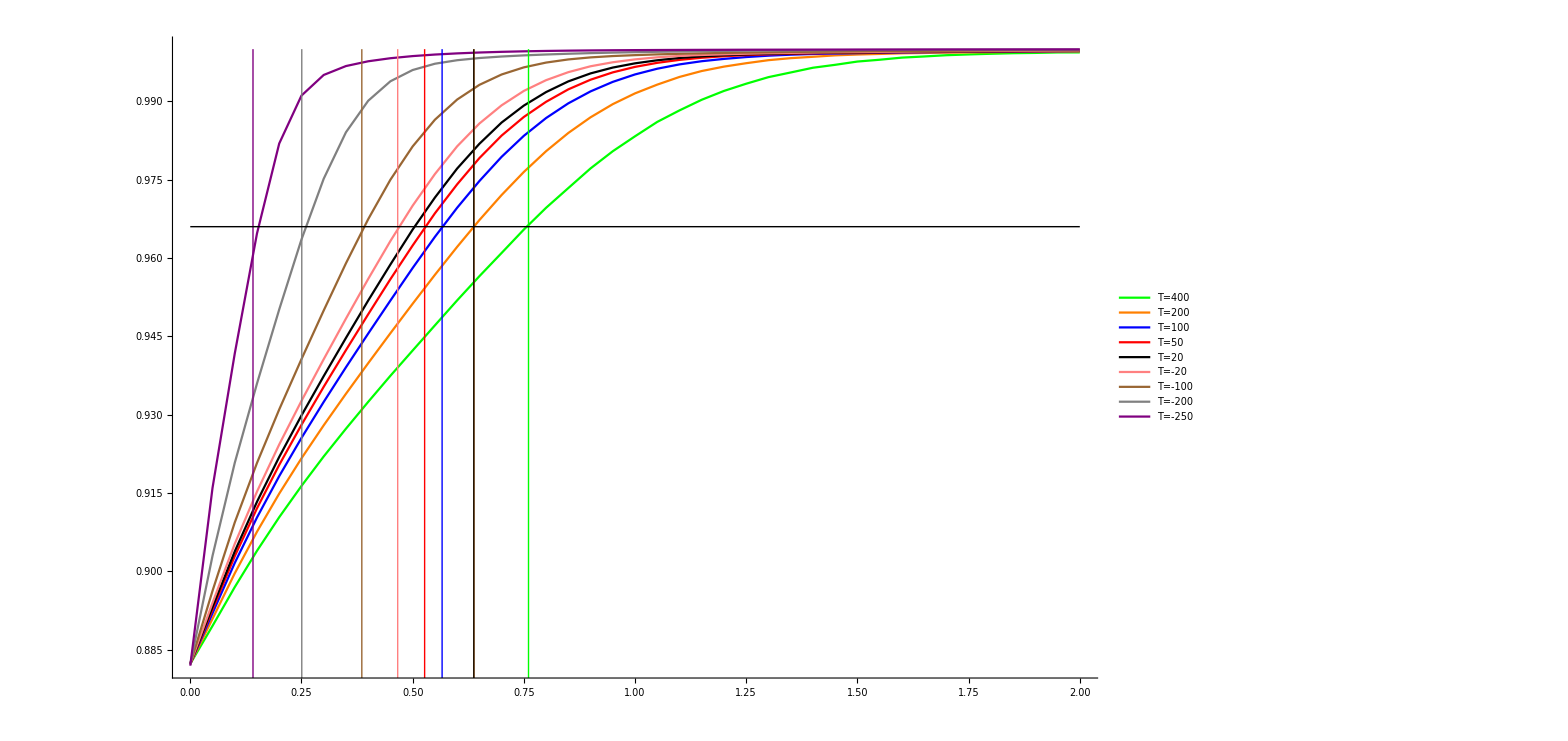

```mathematica
ListPlot[{a5[[2]],a4[[2]],a1[[2]],a2[[2]],a3[[2]],a6[[2]],a7[[2]],a8[[2]],a9[[2]]},PlotLegends->{"T=400","T=200","T=100","T=50","T=20","T=-20","T=-100","T=-200","T=-250"},ImageSize->1200,Joined->True,PlotStyle->{Green,Orange,Blue,Red,Black,Pink,Brown,Gray,Purple},
Epilog->{{Green,Line[{{Rbpress[400][[2]]*10^-9,0},{Rbpress[400][[2]]*10^-9,1}}]},{Orange,Line[{{Rbpress[200][[2]]*10^-9,0},{Rbpress[200][[2]]*10^-9,1}}]},{Blue,Line[{{Rbpress[100][[2]]*10^-9,0},{Rbpress[100][[2]]*10^-9,1}}]},{Red,Line[{{Rbpress[50][[2]]*10^-9,0},{Rbpress[50][[2]]*10^-9,1}}]},{Black,Line[{{Rbpress[200][[2]]*10^-9,0},{Rbpress[200][[2]]*10^-9,1}}]},{Pink,Line[{{Rbpress[-20][[2]]*10^-9,0},{Rbpress[-20][[2]]*10^-9,1}}]},{Brown,Line[{{Rbpress[-100][[2]]*10^-9,0},{Rbpress[-100][[2]]*10^-9,1}}]},{Gray,Line[{{Rbpress[-200][[2]]*10^-9,0},{Rbpress[-200][[2]]*10^-9,1}}]},{Purple,Line[{{Rbpress[-250][[2]]*10^-9,0},{Rbpress[-250][[2]]*10^-9,1}}]},Line[{{0,0.966},{2,0.966}}]}]
```

# Seperation vs Real Part

Module

```mathematica
Lev4DoppTestscSepRe[T_,P_,diam_,gam_,delt_,kia_,ab_,Sep_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Δ2,d31,d41},
d=(kia+Range[-0.01,0.01,0.000005])*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(Sep*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

If[ab==0,
(*{Transpose[{d/10^9,Im[sd24[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd23[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}],
Transpose[{d/10^9,Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}]
}*)

(*Re[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Re[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]*)
Re[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Re[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]

,
(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}]*)
{Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]])]
}]}
]
]
```

```mathematica
Lev3DoppTestscSepRe[T_,P_,diam_,gam_,delt_,kia_,ab_,sep_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},

d=(kia+Range[-0.01,0.01,0.000005])*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(sep*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 
If[ab==0,
(*{Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
}*)
(*Re[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Re[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]*)
Re[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Re[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]

,
(*
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}],*)
{
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]])]}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
}
]]
```

P=0

```mathematica
Off[Power::infy]
Off[Infinity::indet]
```

```mathematica
Manipulate[ListPlot[{Lev4DoppTestscSepRe[55,P/1000,1/1000,0*10^6,0,0,0,i*1000],Lev3DoppTestscSepRe[55,P/1000,1/1000,0*10^6,0,0,0,i*1000],Lev3DoppTestscSepRe[55,0/1000,1/1000,0*10^6,0,0,0,i*1000]},PlotLegends->{"4Level","3Level","WIthout EIT"},Axes->False,Frame->True,FrameLabel->{Style["-10MHz to +10 MHz",20,Black],Style["Re[χ] Dispersion",20,Black]},FrameTicks->{False,True},Joined->True,ImageSize->1020,PlotRange->{-0.00003,.00003}],{{i,0,"Seperation(GHz)"},0,5},{P,0,50}]
```

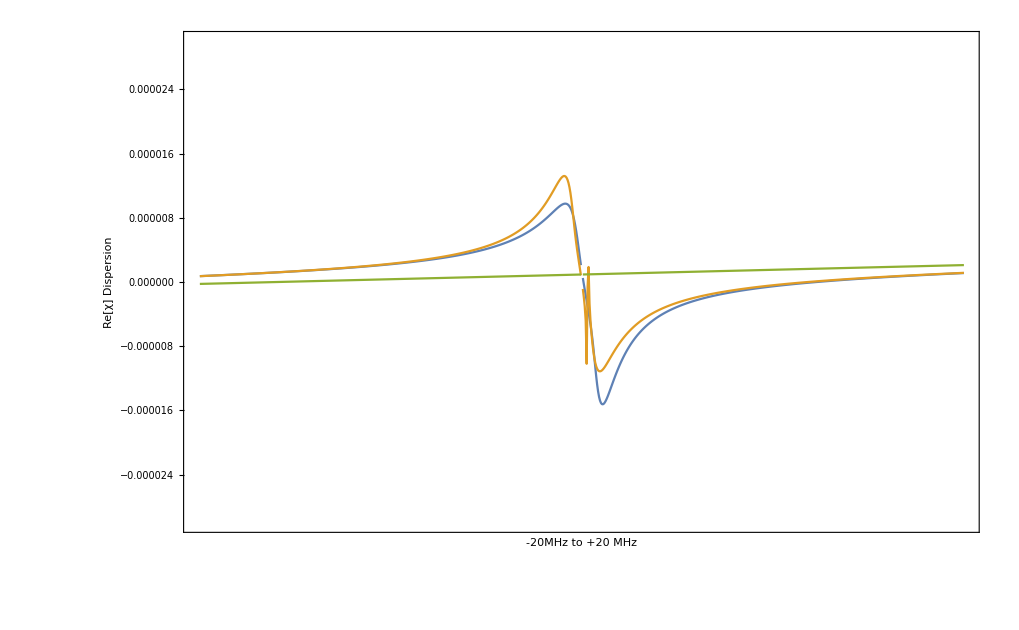

## Off resonance

```mathematica
Lev4DoppTestscSepReOff[T_,P_,diam_,gam_,delt_,kia_,ab_,Sep_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Δ2,d31,d41},
d=(kia+Range[-0.01,0.01,0.00005])*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(Sep*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

If[ab==0,
(*{Transpose[{d/10^9,Im[sd24[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd23[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}],
Transpose[{d/10^9,Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}]
}*)

(*Re[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Re[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]*)
Re[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Re[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]

,
(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}]*)
{Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]])]
}]}
]
]
```

```mathematica
Lev3DoppTestsc[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},
d=Range[2,2.0008,0.000001]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 
If[ab==0,
(*{Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
}*)Transpose[{δ/10^6,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}],

(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}]*)
If[ab==3,
Transpose[{d/10^9,
(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])}],
{
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]])]}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
}
]]]
```

```mathematica
Lev3DoppTestscSepReOff[T_,P_,diam_,gam_,delt_,kia_,ab_,sep_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},

d=(kia+Range[-0.0001,0.0006,0.000001])*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(sep*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 
If[ab==0,
(*{Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
}*)
(*Re[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Re[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]*)
Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]

,
(*
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}],*)
{
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]])]}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
}
]]
```

```mathematica
I
```

```mathematica
Manipulate[ListPlot[{Lev4DoppTestscSepReOff[55,P/1000,1/1000,0*10^6,δ*10^9,δ,0,i*1000],Lev3DoppTestscSepReOff[55,P/1000,1/1000,0*10^6,δ*10^9,δ,0,i*1000],Lev3DoppTestscSepReOff[55,0/1000,1/1000,0*10^6,δ*10^9,δ,0,i*1000]},PlotLegends->{"4Level","3Level","WIthout EIT"},Axes->False,Frame->True,FrameLabel->{Style["-100MHz to +100 MHz",20,Black],Style["Re[χ] Dispersion",20,Black]},FrameTicks->{False,True},Joined->True,ImageSize->1020],{{i,0.3,"Seperation(GHz)"},0,5},{{P,0.1},0,50},{{δ,0.1},0,10}]
```

```mathematica
Manipulate[ListPlot[Lev3DoppTestscSepReOff[55,P/1000,1/1000,0*10^6,δ*10^9,δ,2,i*1000],PlotLegends->{"4Level","3Level","WIthout EIT"},Axes->False,Frame->True,FrameLabel->{Style["-100MHz to +100 MHz",20,Black],Style["Re[χ] Dispersion",20,Black]},FrameTicks->{False,True},Joined->True,ImageSize->1020],{{i,0.36,"Seperation(GHz)"},0,5},{{P,5},0,50},{{δ,2},0,10}]
```

General::ovfl: Overflow occurred in computation.

General::unfl: Underflow occurred in computation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

Statistics`Library`MatrixRowTranslate::ovfl: Overflow occurred in computation.

# γ vs Transmission

Module

```mathematica
Lev4DoppTestsc4[T_,P_,diam_,gam_,delt_,kia_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Δ2,d31,d41},
d=(kia+Range[-0.01,0.01,0.00005])*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

If[ab==0,
(*{Transpose[{d/10^9,Im[sd24[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd23[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}],
Transpose[{d/10^9,Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}]
}*)

Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]


,
(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}]*)
{Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]])]
}]}
]
]
```

```mathematica
Lev3DoppTestsc4[T_,P_,diam_,gam_,delt_,kia_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},

d=(kia+Range[-0.01,0.01,0.00005])*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 
If[ab==0,
(*{Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
}*)
Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]],
(*
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}],*)
{
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]])]}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
}
]]
```

```mathematica
Lev3Testsc4[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41,Δ2},
d=Range[-0.01,0.01,0.000005]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(4 d42^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ+w43)-ⅈ omegac2^2) ℏ);   
χ24=(4 d42^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ+w43)+ⅈ omegac2^2) ℏ);   
χ32=(4 d32^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ)-ⅈ omegac1^2) ℏ);   
χ23=(4 d32^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)+ⅈ omegac1^2) ℏ); 

If[ab==0,
(*{Transpose[{d/10^9,Im[χ24]}],
Transpose[{d/10^9,Im[χ42]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
}*)
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]}],
(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]*)
If[ab==3,
Transpose[{d/10^9,
(Im[χ42]+Im[χ32])}],
{Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ32])]
}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42])]
}]}
]]
]
```

```mathematica
Lev4Testsc4[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41,Δ2},
d=Range[-0.01,0.01,0.0000005]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(d42^2 Nat ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(2 √5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ32=-(d32^2 Nat ((-35+2 √70) omegac1^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)))/(5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ24=(d42^2 Nat (ⅈ (4 √5-5 √14) omegac1^2+16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)))/(2 √5 e0 (8 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ) (w43+ⅈ γ42+δ+Δ)+ⅈ omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)) ℏ);
χ23=(d32^2 Nat ((35 √2-4 √35) omegac1^2-40 ⅈ √2 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ)))/(5 √2 e0 (omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))) ℏ);

If[ab==0,
(*{Transpose[{d/10^9,Im[χ24]}],
Transpose[{d/10^9,Im[χ42]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
}*)Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}],
(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]*)
If[ab==3,
Transpose[{d/10^9,
(Im[χ42]+Im[χ32])
}],
{Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ32])]
}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42])]
}]}
]]
]
```

P=0

```mathematica
Clear[γvT3,γvT4]
```

```mathematica
(*Range[-0.3,0.1,0.001]*)
max3=Mean[GaussianFilter[DeleteCases[Select[Lev3DoppTestsc4[50,0/1000,1/1000,0*10^6,0,0,0],-10^-10≤ #&&#∈Reals&],Indeterminate],5]];
max4=Mean[GaussianFilter[DeleteCases[Select[Lev4DoppTestsc4[50,0/1000,1/1000,0*10^6,0,0,0],-10^-10≤ #&&#∈Reals&],Indeterminate],6]];
γvT3[P_]:=γvT3[P]=Table[{k,1-Min[Select[MedianFilter[Select[Lev3DoppTestsc4[50,P/1000,1/1000,k*10^6,0,0,0],-10^-10≤ #&&#∈Reals&],5],#≥0&]]/max3},{k,0,10,0.2}];
γvT4[P_]:=γvT4[P]=Table[{k,1-Min[Select[MedianFilter[Select[Lev4DoppTestsc4[50,P/1000,1/1000,k*10^6,0,0,0],-10^-10≤ #&&#∈Reals&],5],1>#≥0&]]/max4},{k,0,10,0.2}];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

Power::infy: Infinite expression 1/(0.+0. ⅈ)^2 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
Clear[
```

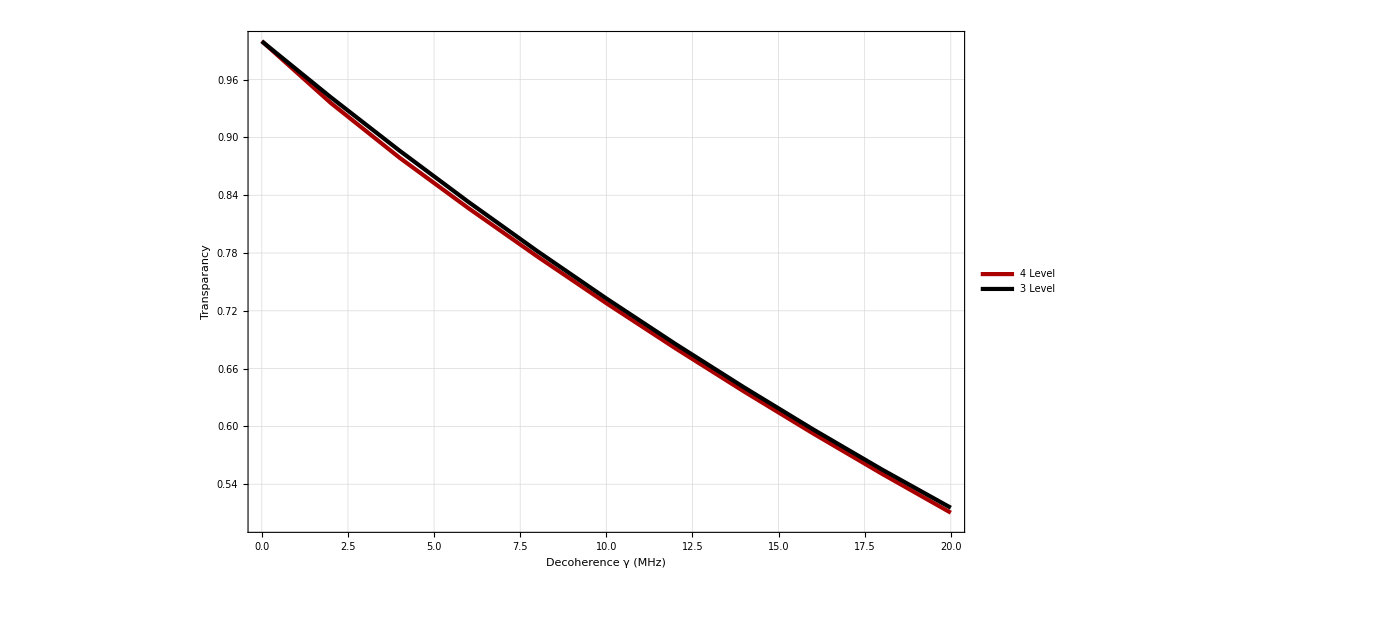

```mathematica
ListPlot[{p1,p2},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[LineLegend[{"4 Level","3 Level"},LegendFunction->"Frame",LabelStyle->{FontSize->36}],{Right,Center}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Darker[Black]},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Decoherence γ (MHz)",50,Black],Style["Transparancy",50,Black]},GridLines->Automatic,PlotRange->{{0,20},{.5,1}}]
```

{{0,1.},{2,0.93586},{4,0.878908},{6,0.826506},{8,0.776345},{10,0.727938},{12,0.68123},{14,0.63618},{16,0.592733},{18,0.550828},{20,0.510394}}

{{0,0.999839},{2,0.941786},{4,0.886228},{6,0.832973},{8,0.781881},{10,0.732831},{12,0.685717},{14,0.640448},{16,0.596963},{18,0.555258},{20,0.515531}}

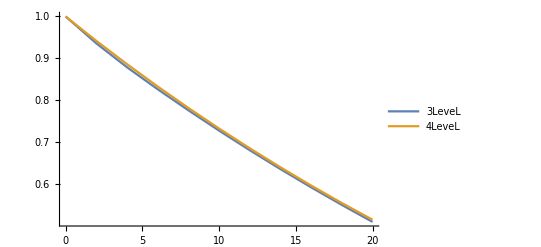

```mathematica
max3=Mean[GaussianFilter[DeleteCases[Select[Lev3Testsc4[50,0/1000,1/1000,0*10^6,0,3][[All,2]],-10^-10≤ #&&#∈Reals&],Indeterminate],5]];
max4=Mean[GaussianFilter[DeleteCases[Select[Lev4Testsc4[50,0/1000,1/1000,0*10^6,0,3][[All,2]],-10^-10≤ #&&#∈Reals&],Indeterminate],6]];
p1=Table[{k,1-Min[Select[MedianFilter[Select[Lev3Testsc4[50,20/1000,1/1000,k*10^6,0,3][[All,2]],-10^-10≤ #&&#∈Reals&],5],#≥0&]]/max3},{k,0,20,2}]
p2=Table[{k,1-Min[Select[MedianFilter[Select[Lev4Testsc4[50,20/1000,1/1000,k*10^6,0,3][[All,2]],-10^-10≤ #&&#∈Reals&],5],1>#≥0&]]/max4},{k,0,20,2}]
ListPlot[{p1,p2},Joined->True,PlotLegends->{"3LeveL","4LeveL"}]
```

{{0.,0.999992},{0.2,0.936811},{0.4,0.879806},{0.6,0.826784},{0.8,0.776407},{1.,0.727952},{1.2,0.681229},{1.4,0.636174},{1.6,0.615394},{1.8,0.613089},{2.,0.611078},{2.2,0.609355},{2.4,0.607911},{2.6,0.606737},{2.8,0.605822},{3.,0.605154},{3.2,0.604721},{3.4,0.604509},{3.6,0.604506},{3.8,0.604698},{4.,0.605071},{4.2,0.605612},{4.4,0.606308},{4.6,0.607145},{4.8,0.608113},{5.,0.609198},{5.2,0.610389},{5.4,0.611676},{5.6,0.613049},{5.8,0.614496},{6.,0.61601},{6.2,0.617583},{6.4,0.619205},{6.6,0.62087},{6.8,0.622571},{7.,0.624302},{7.2,0.626057},{7.4,0.627831},{7.6,0.629619},{7.8,0.631417},{8.,0.63322},{8.2,0.635025},{8.4,0.636829},{8.6,0.638629},{8.8,0.640423},{9.,0.642207},{9.2,0.64398},{9.4,0.64574},{9.6,0.647486},{9.8,0.649215},{10.,0.650927},{10.2,0.652621},{10.4,0.654296},{10.6,0.65595},{10.8,0.657583},{11.,0.659196},{11.2,0.660786},{11.4,0.662354},{11.6,0.6639},{11.8,0.665424},{12.,0.666924},{12.2,0.668402},{12.4,0.669857},{12.6,0.671289},{12.8,0.672698},{13.,0.674085},{13.2,0.675449},{13.4,0.676791},{13.6,0.67811},{13.8,0.679408},{14.,0.680684},{14.2,0.681939},{14.4,0.683173},{14.6,0.684386},{14.8,0.685578},{15.,0.686751},{15.2,0.687903},{15.4,0.689036},{15.6,0.690149},{15.8,0.691243},{16.,0.692319},{16.2,0.693377},{16.4,0.694417},{16.6,0.695439},{16.8,0.696443},{17.,0.697431},{17.2,0.698402},{17.4,0.699357},{17.6,0.700296},{17.8,0.701219},{18.,0.702126},{18.2,0.703019},{18.4,0.703897},{18.6,0.70476},{18.8,0.705609},{19.,0.706444},{19.2,0.707265},{19.4,0.708073},{19.6,0.708868},{19.8,0.70965},{20.,0.71042}}

{{0.,0.999838},{0.2,0.941681},{0.4,0.885985},{0.6,0.832596},{0.8,0.781371},{1.,0.732183},{1.2,0.684911},{1.4,0.639445},{1.6,0.635455},{1.8,0.633548},{2.,0.631883},{2.2,0.630455},{2.4,0.629256},{2.6,0.628281},{2.8,0.62752},{3.,0.626964},{3.2,0.626604},{3.4,0.626429},{3.6,0.626429},{3.8,0.626592},{4.,0.626909},{4.2,0.627368},{4.4,0.627959},{4.6,0.628671},{4.8,0.629494},{5.,0.630419},{5.2,0.631437},{5.4,0.632537},{5.6,0.633712},{5.8,0.634954},{6.,0.636254},{6.2,0.637607},{6.4,0.639004},{6.6,0.640441},{6.8,0.641911},{7.,0.643408},{7.2,0.644929},{7.4,0.646468},{7.6,0.648021},{7.8,0.649584},{8.,0.651154},{8.2,0.652728},{8.4,0.654303},{8.6,0.655876},{8.8,0.657444},{9.,0.659007},{9.2,0.660561},{9.4,0.662105},{9.6,0.663638},{9.8,0.665158},{10.,0.666664},{10.2,0.668155},{10.4,0.669631},{10.6,0.67109},{10.8,0.672531},{11.,0.673955},{11.2,0.675361},{11.4,0.676747},{11.6,0.678115},{11.8,0.679464},{12.,0.680794},{12.2,0.682104},{12.4,0.683394},{12.6,0.684665},{12.8,0.685916},{13.,0.687148},{13.2,0.688361},{13.4,0.689554},{13.6,0.690728},{13.8,0.691883},{14.,0.69302},{14.2,0.694137},{14.4,0.695237},{14.6,0.696318},{14.8,0.697381},{15.,0.698427},{15.2,0.699455},{15.4,0.700466},{15.6,0.70146},{15.8,0.702437},{16.,0.703399},{16.2,0.704344},{16.4,0.705273},{16.6,0.706187},{16.8,0.707085},{17.,0.707969},{17.2,0.708837},{17.4,0.709692},{17.6,0.710532},{17.8,0.711358},{18.,0.712171},{18.2,0.71297},{18.4,0.713756},{18.6,0.71453},{18.8,0.71529},{19.,0.716039},{19.2,0.716775},{19.4,0.717499},{19.6,0.718212},{19.8,0.718913},{20.,0.719603}}

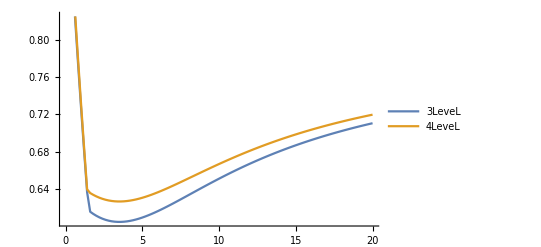

```mathematica
p1=Table[{k,1-Min[Select[MedianFilter[Select[Lev3Testsc4[50,2/1000,1/1000,k*10^6,0,3][[All,2]],-10^-10≤ #&&#∈Reals&],5],#≥0&]]/max3},{k,0,20,.2}]
p2=Table[{k,1-Min[Select[MedianFilter[Select[Lev4Testsc4[50,2/1000,1/1000,k*10^6,0,3][[All,2]],-10^-10≤ #&&#∈Reals&],5],1>#≥0&]]/max4},{k,0,20,.2}]
ListPlot[{p1,p2},Joined->True,PlotLegends->{"3LeveL","4LeveL"}]
```

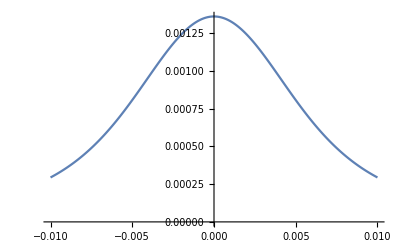

```mathematica
ListPlot[Lev3Testsc4[60,2/1000,1/1000,12*10^6,0,3],PlotRange->All,Joined->True]
```

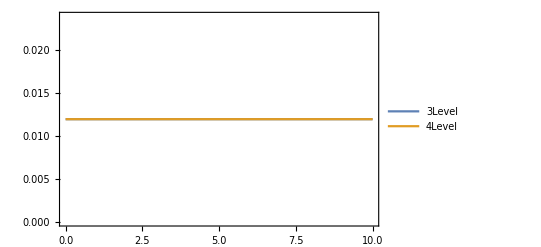

```mathematica
ListPlot[{γvT3[0],γvT4[0]},Joined->True,PlotRange->All,Frame->True,Axes->False,PlotLegends->{"3Level","4Level"}]
```

P=1

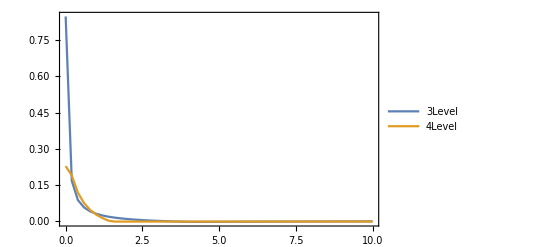

```mathematica
ListPlot[{γvT3[1],γvT4[1]},Joined->True,PlotRange->All,Frame->True,Axes->False,PlotLegends->{"3Level","4Level"}]
```

P=10 (Poster)

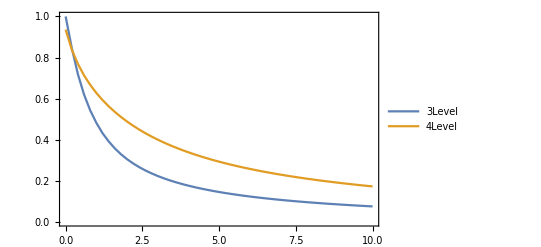

```mathematica
ListPlot[{γvT3[20],γvT4[20]},Joined->True,PlotRange->All,Frame->True,Axes->False,PlotLegends->{"3Level","4Level"}]
```

P=50

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

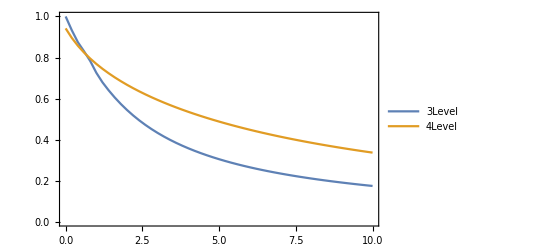

```mathematica
ListPlot[{γvT3[50],γvT4[50]},Joined->True,PlotRange->All,Frame->True,Axes->False,PlotLegends->{"3Level","4Level"}]
```

P=100

```mathematica
ListPlot[{γvT3[100],γvT4[100]},Joined->True,PlotRange->All,Frame->True,Axes->False,PlotLegends->{"3Level","4Level"}]
```

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

$Aborted

## Power vs Transmission

Module

```mathematica
Lev4DoppTestsc4[T_,P_,diam_,gam_,delt_,kia_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Δ2,d31,d41},
d=(kia+Flatten[{Range[-0.002,-0.0006,0.00005],Range[0.0006,0.02,0.0005]}])*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

If[ab==0,
(*{Transpose[{d/10^9,Im[sd24[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd23[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}],
Transpose[{d/10^9,Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}]
}*)

Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]


,
(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}]*)
{Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]])]
}]}
]
]
```

```mathematica
Lev3DoppTestsc4[T_,P_,diam_,gam_,delt_,kia_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},
d=(kia+Flatten[{Range[-0.002,-0.0006,0.00005],Range[0.0006,0.02,0.0005]}])*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 
If[ab==0,
(*{Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
}*)
Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]],
(*
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}],*)
{
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]])]}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
}
]]
```

P=0

```mathematica
Clear[PvT3,PvT4]
```

```mathematica
(*Off[Power::infy];
Off[Infinity::indet]
max3=Min[DeleteCases[Select[Lev3DoppTestsc4[60,0/1000,1/1000,0.5*10^6,0,0,0],-10^-10≤ #&&#∈Reals&],Indeterminate]];
max4=Min[DeleteCases[Select[Lev4DoppTestsc4[60,0/1000,1/1000,0.5*10^6,0,0,0],-10^-10≤ #&&#∈Reals&],Indeterminate]];
PvT3[γ_]:=PvT3[γ]=Table[{k,1-Min[Select[GaussianFilter[Select[Lev3DoppTestsc4[60,k/1000,1/1000,γ*10^6,0,0,0],0.00005 >#>10^-8&&#∈Reals&],50],0.00005>#≥10^-8&]]/max3},{k,0,100,1}];
PvT4[γ_]:=PvT4[γ]=Table[{k,1-Min[Select[GaussianFilter[Select[Lev4DoppTestsc4[60,k/1000,1/1000,γ*10^6,0,0,0],0.00005 >#>10^-8&&#∈Reals&],50],0.00005>#≥10^-8&]]/max4},{k,0,100,1}];*)
```

```mathematica
(*Clear[PvT3,PvT4]
max3=Min[DeleteCases[Select[Lev3DoppTestsc4[60,0/1000,1/1000,0.5*10^6,0,0,0],-10^-10≤ #&&#∈Reals&],Indeterminate]];
max4=Min[DeleteCases[Select[Lev4DoppTestsc4[60,0/1000,1/1000,0.5*10^6,0,0,0],-10^-10≤ #&&#∈Reals&],Indeterminate]];
Import["https://raw.githubusercontent.com/antononcube/MathematicaForPrediction/master/OutlierIdentifiers.m"]
PvT3[γ_,l_]:=PvT3[γ,l]=Module[{data1,olPos,data},
Table[
data1=Lev3DoppTestsc4[60,k/1000,1/1000,γ*10^6,0,0,0];
olPos=OutlierPosition[data1,SPLUSQuartileIdentifierParameters];
data=Delete[data1,List/@olPos];
{k,1-Min[Select[GaussianFilter[Select[data,0.00005>#>10^-8&],l],0.00005>#≥10^-8&]]/max3},{k,0,100,1}]
]
PvT4[γ_,l_]:=PvT4[γ,l]=Module[{data1,olPos,data},
Table[
data1=Lev4DoppTestsc4[60,k/1000,1/1000,γ*10^6,0,0,0];
olPos=OutlierPosition[data1,SPLUSQuartileIdentifierParameters];
data=Delete[data1,List/@olPos];
{k,1-Min[Select[GaussianFilter[Select[data,0.00005>#>10^-8&],l],0.00005>#≥10^-8&]]/max4},{k,0,100,1}]
]*)
```

```mathematica
Clear[PvT3,PvT4]
max3=Min[DeleteCases[Select[Lev3DoppTestsc4[60,0/1000,1/1000,0.5*10^6,0,0,0],1.1 10^-6<#<0.00006&],Indeterminate]];
max4=Min[DeleteCases[Select[Lev4DoppTestsc4[60,0/1000,1/1000,0.5*10^6,0,0,0],1.1 10^-6<#<0.00006&],Indeterminate]];
PvT3[γ_]:=PvT3[γ]=Module[{outliers,data},
Table[
data=Select[Lev3DoppTestsc4[60,k/1000,1/1000,γ*10^6,0,0,0],1.1 10^-6<#<0.00006&];
outliers=Flatten[Position[data,x_/;x>1||x<0]];
(data[[#]]=Mean[Select[data[[#-3;;#+3]],0<#<1&]])&/@outliers;
{k,1-Min[data,1]/max3},{k,0,200,0.1}]
]
PvT4[γ_]:=PvT4[γ]=Module[{outliers,data},
Table[
data=Select[Lev4DoppTestsc4[60,k/1000,1/1000,γ*10^6,0,0,0],1.1 10^-6<#<0.00006&];
outliers=Flatten[Position[data,x_/;x>1||x<0]];
(data[[#]]=Mean[Select[data[[#-3;;#+3]],0<#<1&]])&/@outliers;
{k,1-Min[data,1]/max3},{k,0,200,0.1}]
]
```

```mathematica
Manipulate[
data=Select[Lev4DoppTestsc4[60,k/1000,1/1000,0.5*10^6,0,0,0],1.1 10^-6<#<0.00006&];
outliers=Flatten[Position[data,x_/;x>1||x<0]];
(data[[#]]=Mean[Select[data[[#-3;;#+3]],0<#<1&]])&/@outliers;
Show[ListPlot[data,ImageSize->1020],ListPlot[MedianFilter[data,2],Joined->True,PlotStyle->Red]
]
,{k,0,400,1}]
```

ListPlot::lpn: Lev4DoppTestsc4[] is not a list of numbers or pairs of numbers.

MedianFilter::arg1: The first argument Lev4DoppTestsc4[] is neither a rectangular array nor an image.

General::stop: Further output of MedianFilter::arg1 will be suppressed during this calculation.

ListPlot::lpn: MedianFilter[Lev4DoppTestsc4[],2.] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[Lev4DoppTestsc4[],ImageSize→1020],ListPlot[MedianFilter[Lev4DoppTestsc4[],2],Joined→True,PlotStyle→RGBColor[1, 0, 0]]].

ListPlot::lpn: Lev4DoppTestsc4[] is not a list of numbers or pairs of numbers.

MedianFilter::arg1: The first argument Lev4DoppTestsc4[] is neither a rectangular array nor an image.

ListPlot::lpn: MedianFilter[Lev4DoppTestsc4[],2.] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

MedianFilter::arg1: The first argument Lev4DoppTestsc4[] is neither a rectangular array nor an image.

General::stop: Further output of MedianFilter::arg1 will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[Lev4DoppTestsc4[],ImageSize→1020],ListPlot[MedianFilter[Lev4DoppTestsc4[],2],Joined→True,PlotStyle→RGBColor[1, 0, 0]]].

ListPlot::lpn: Lev4DoppTestsc4[] is not a list of numbers or pairs of numbers.

MedianFilter::arg1: The first argument Lev4DoppTestsc4[] is neither a rectangular array nor an image.

ListPlot::lpn: MedianFilter[Lev4DoppTestsc4[],2.] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

MedianFilter::arg1: The first argument Lev4DoppTestsc4[] is neither a rectangular array nor an image.

General::stop: Further output of MedianFilter::arg1 will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[Lev4DoppTestsc4[],ImageSize→1020],ListPlot[MedianFilter[Lev4DoppTestsc4[],2],Joined→True,PlotStyle→RGBColor[1, 0, 0]]].

ListPlot::lpn: Lev4DoppTestsc4[] is not a list of numbers or pairs of numbers.

MedianFilter::arg1: The first argument Lev4DoppTestsc4[] is neither a rectangular array nor an image.

ListPlot::lpn: MedianFilter[Lev4DoppTestsc4[],2.] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

MedianFilter::arg1: The first argument Lev4DoppTestsc4[] is neither a rectangular array nor an image.

General::stop: Further output of MedianFilter::arg1 will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[Lev4DoppTestsc4[],ImageSize→1020],ListPlot[MedianFilter[Lev4DoppTestsc4[],2],Joined→True,PlotStyle→RGBColor[1, 0, 0]]].

```mathematica
Manipulate[
data=Select[Lev3DoppTestsc4[60,k/1000,1/1000,0.5*10^6,0,0,0],1.1 10^-6<#<0.00006&];
outliers=Flatten[Position[data,x_/;x>1||x<0]];
(data[[#]]=Mean[Select[data[[#-3;;#+3]],0<#<1&]])&/@outliers;
Show[ListPlot[data,ImageSize->1020],ListPlot[MedianFilter[data,2],Joined->True,PlotStyle->Red]
]
,{k,0,300,1}]
```

ListPlot::lpn: Lev3DoppTestsc4[] is not a list of numbers or pairs of numbers.

MedianFilter::arg1: The first argument Lev3DoppTestsc4[] is neither a rectangular array nor an image.

General::stop: Further output of MedianFilter::arg1 will be suppressed during this calculation.

ListPlot::lpn: MedianFilter[Lev3DoppTestsc4[],2.] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[Lev3DoppTestsc4[],ImageSize→1020],ListPlot[MedianFilter[Lev3DoppTestsc4[],2],Joined→True,PlotStyle→RGBColor[1, 0, 0]]].

ListPlot::lpn: Lev3DoppTestsc4[] is not a list of numbers or pairs of numbers.

MedianFilter::arg1: The first argument Lev3DoppTestsc4[] is neither a rectangular array nor an image.

General::stop: Further output of MedianFilter::arg1 will be suppressed during this calculation.

ListPlot::lpn: MedianFilter[Lev3DoppTestsc4[],2.] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[Lev3DoppTestsc4[],ImageSize→1020],ListPlot[MedianFilter[Lev3DoppTestsc4[],2],Joined→True,PlotStyle→RGBColor[1, 0, 0]]].

ListPlot::lpn: Lev3DoppTestsc4[] is not a list of numbers or pairs of numbers.

MedianFilter::arg1: The first argument Lev3DoppTestsc4[] is neither a rectangular array nor an image.

ListPlot::lpn: MedianFilter[Lev3DoppTestsc4[],2.] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

MedianFilter::arg1: The first argument Lev3DoppTestsc4[] is neither a rectangular array nor an image.

General::stop: Further output of MedianFilter::arg1 will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[Lev3DoppTestsc4[],ImageSize→1020],ListPlot[MedianFilter[Lev3DoppTestsc4[],2],Joined→True,PlotStyle→RGBColor[1, 0, 0]]].

ListPlot::lpn: Lev3DoppTestsc4[] is not a list of numbers or pairs of numbers.

MedianFilter::arg1: The first argument Lev3DoppTestsc4[] is neither a rectangular array nor an image.

ListPlot::lpn: MedianFilter[Lev3DoppTestsc4[],2.] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

MedianFilter::arg1: The first argument Lev3DoppTestsc4[] is neither a rectangular array nor an image.

General::stop: Further output of MedianFilter::arg1 will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[Lev3DoppTestsc4[],ImageSize→1020],ListPlot[MedianFilter[Lev3DoppTestsc4[],2],Joined→True,PlotStyle→RGBColor[1, 0, 0]]].

ListPlot::lpn: Lev3DoppTestsc4[] is not a list of numbers or pairs of numbers.

MedianFilter::arg1: The first argument Lev3DoppTestsc4[] is neither a rectangular array nor an image.

ListPlot::lpn: MedianFilter[Lev3DoppTestsc4[],2.] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

MedianFilter::arg1: The first argument Lev3DoppTestsc4[] is neither a rectangular array nor an image.

General::stop: Further output of MedianFilter::arg1 will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[Lev3DoppTestsc4[],ImageSize→1020],ListPlot[MedianFilter[Lev3DoppTestsc4[],2],Joined→True,PlotStyle→RGBColor[1, 0, 0]]].

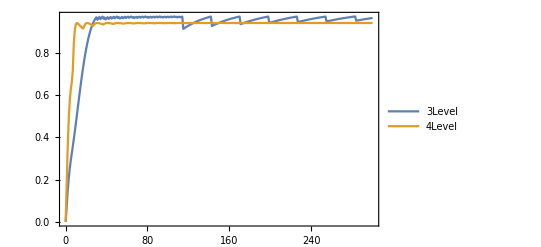

```mathematica
ListPlot[{PvT3[0],PvT4[0]},Joined->True,PlotRange->All,Frame->True,Axes->False,PlotLegends->{"3Level","4Level"},PlotRange->{0,1}]
```

γ=0.5*10^6

```mathematica
Om[P_]:=Module[{ℏ,e0,c,d31,diam},
d31=Sqrt[2/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
diam=1/1000;
1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]]
```

```mathematica
Om[1]
```

1.43437×10^9

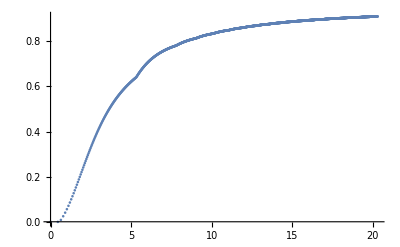

```mathematica
ListPlot[Transpose[{Om[PvT4[0.5][[All,1]]/1000]*10^-9,PvT4[0.5][[All,2]]}],PlotRange->All]
```

C:\Users\Admin\Qsync\PersonalFolders\Saesun\Poster

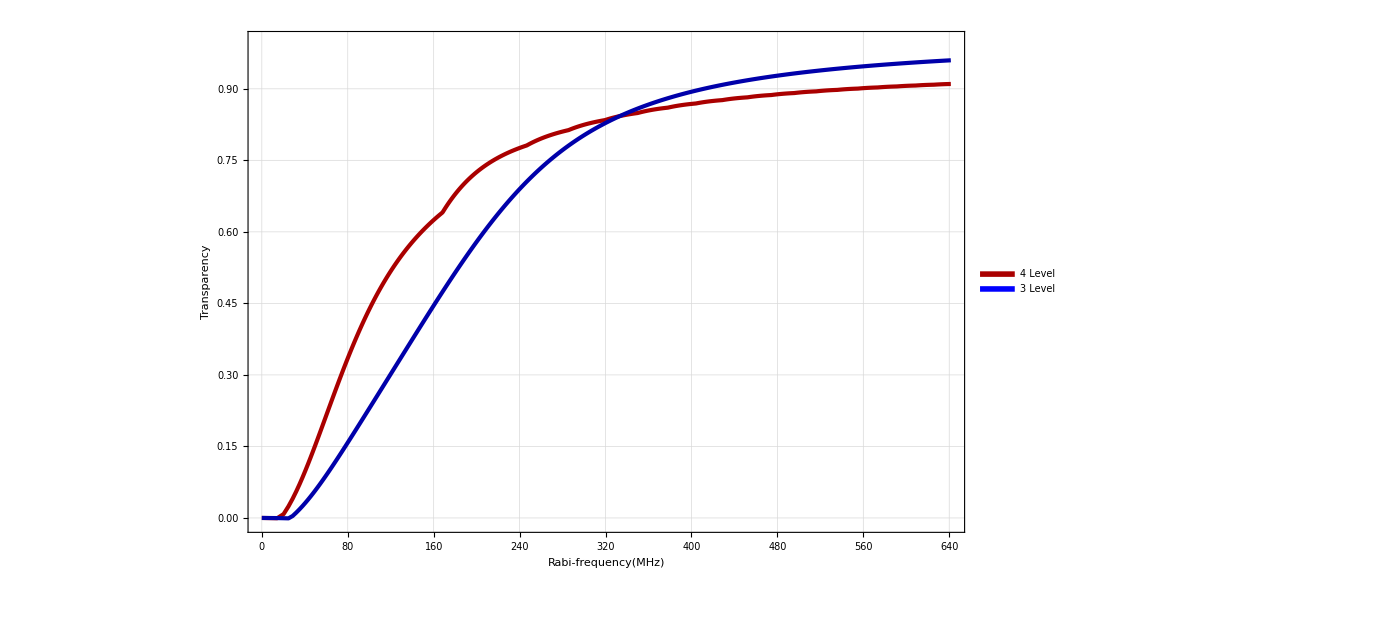

```mathematica
SetDirectory["C:\\Users\\Admin\\Qsync\\PersonalFolders\\Saesun\\Poster"]
ListPlot[{Transpose[{Om[PvT4[0.5][[All,1]]/1000]*10^-6,PvT4[0.5][[All,2]]//Chop}],Transpose[{Om[PvT3[0.5][[All,1]]/1000]*10^-6,PvT3[0.5][[All,2]]//Chop}]},Joined->True,PlotRange->{-0.01,1},Frame->True,Axes->False,Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,Center}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Darker[Blue]}},FrameLabel->{Style["Rabi-frequency(MHz)",50,Black],Style["Transparency ",50,Black]},GridLines->Automatic]
```

```mathematica
ListPlot[{Transpose[{Om[PvT4[0.5][[All,1]]/1000]*10^-6,PvT4[0.3][[All,2]]//Chop}],Transpose[{Om[PvT3[0.5][[All,1]]/1000]*10^-6,PvT3[0.3][[All,2]]//Chop}]},Joined->True,PlotRange->{-0.01,1},Frame->True,Axes->False,Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,Center}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Darker[Blue]}},FrameLabel->{Style["Rabi-frequency(MHz)",50,Black],Style["Transparency ",50,Black]},GridLines->Automatic]
```

$Aborted

```mathematica
Export["helloPvT.jpg",Out[214]]
```

helloPvT.jpg

γ=1*10^6

```mathematica
ListPlot[{PvT3[1],PvT4[1]},Joined->True,PlotRange->All,Frame->True,Axes->False,PlotLegends->{"3Level","4Level"},PlotRange->{0,1}]
```

$Aborted

γ=2*10^6

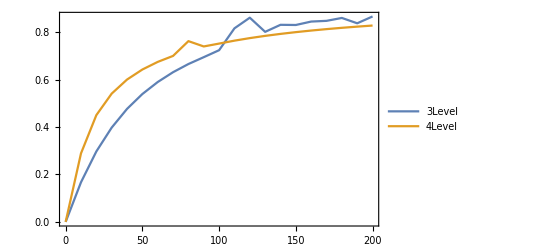

```mathematica
ListPlot[{PvT3[2],PvT4[2]},Joined->True,PlotRange->All,Frame->True,Axes->False,PlotLegends->{"3Level","4Level"},PlotRange->{0,1}]
```

γ=5*10^6

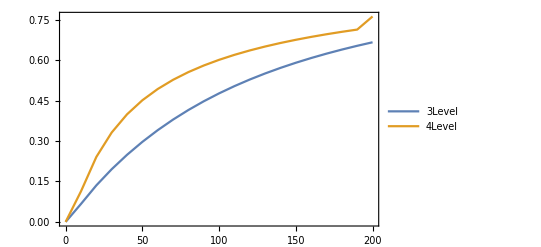

```mathematica
ListPlot[{PvT3[5],PvT4[5]},Joined->True,PlotRange->All,Frame->True,Axes->False,PlotLegends->{"3Level","4Level"}]
```

γ=10*10^6

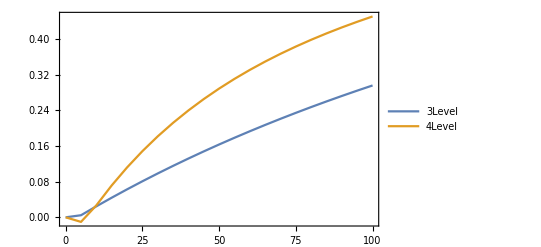

```mathematica
ListPlot[{PvT3[10],PvT4[10]},Joined->True,PlotRange->All,Frame->True,Axes->False,PlotLegends->{"3Level","4Level"}]
```

## Checking the Broadening and not braodening

```mathematica
Lev3Testsc6[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41,Δ2},
d=Range[-0.6,0.6,0.0017]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(4 d42^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ+w43)-ⅈ omegac2^2) ℏ);   
χ24=(4 d42^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ+w43)+ⅈ omegac2^2) ℏ);   
χ32=(4 d32^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ)-ⅈ omegac1^2) ℏ);   
χ23=(4 d32^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)+ⅈ omegac1^2) ℏ); 

If[ab==0,
(*{Transpose[{d/10^9,Im[χ24]}],
Transpose[{d/10^9,Im[χ42]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
}*)
{Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ32])]}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42])]}]},
(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]*)
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ32]+Im[χ42])]}]
]
]
```

```mathematica
Lev4Testsc6[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41,Δ2},
d=Range[-0.6,0.6,0.0017]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(d42^2 Nat ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(2 √5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ32=-(d32^2 Nat ((-35+2 √70) omegac1^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)))/(5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ24=(d42^2 Nat (ⅈ (4 √5-5 √14) omegac1^2+16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)))/(2 √5 e0 (8 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ) (w43+ⅈ γ42+δ+Δ)+ⅈ omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)) ℏ);
χ23=(d32^2 Nat ((35 √2-4 √35) omegac1^2-40 ⅈ √2 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ)))/(5 √2 e0 (omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))) ℏ);

If[ab==0,
(*{Transpose[{d/10^9,Im[χ24]}],
Transpose[{d/10^9,Im[χ42]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
}*){Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42])]
}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ32])]
}]

}
,
(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]*)
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]
]
]
```

```mathematica
Lev4DoppTestsc6[T_,P_,diam_,gam_,delt_,kia_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Δ2,d31,d41},
d=(kia+Flatten[{Range[-0.6,0.6,0.0017]}])*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

If[ab==0,
(*{Transpose[{d/10^9,Im[sd24[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd23[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}],
Transpose[{d/10^9,Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}]
}*)

(*Transpose[{d/10^9,Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}]*)

{Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]])]
}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}]
}
,
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]}]
]]
```

```mathematica
Lev3DoppTestsc6[T_,P_,diam_,gam_,delt_,kia_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},

d=(kia+Flatten[{Range[-0.6,0.6,0.0017]}])*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 
If[ab==0,
(*{Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
}*)
(*Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],*)

{Transpose[{d/10^9,Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]])]}],
Transpose[{d/10^9,Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}]}
,
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}]
]]
```

20

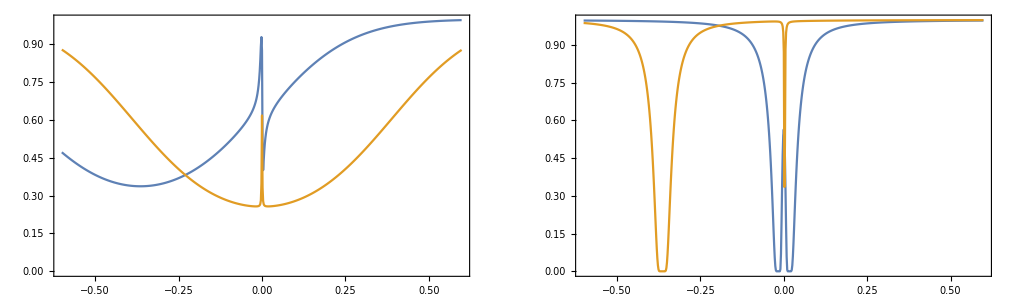

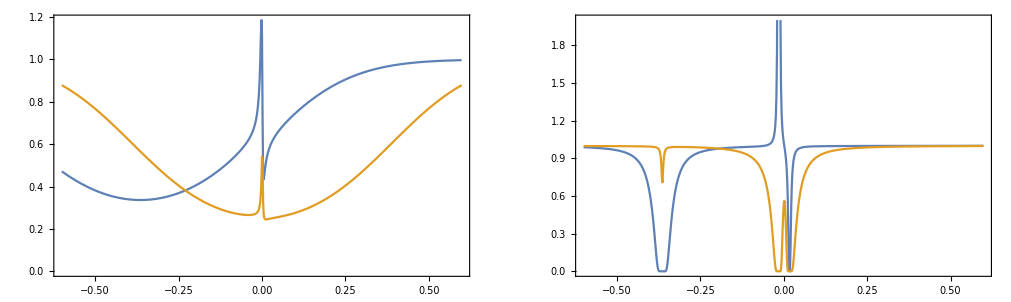

```mathematica
p=20
GraphicsRow[{ListPlot[Lev3DoppTestsc6[50,p/1000,1/1000,0.5*10^6,0,0,0],Joined->True,Frame->True,Axes->False],ListPlot[Lev3Testsc6[50,p/1000,1/1000,0.5*10^6,0,0],Joined->True,Frame->True,Axes->False,PlotRange->All]}]
GraphicsRow[{ListPlot[Lev4DoppTestsc6[50,p/1000,1/1000,0.5*10^6,0,0,0],Joined->True,Frame->True,Axes->False],ListPlot[Lev4Testsc6[50,p/1000,1/1000,0.5*10^6,0,0],Joined->True,Frame->True,Axes->False,PlotRange->{0,2}]}]
```

```mathematica
Select[Lev3DoppTestsc6[50,p/1000,1/1000,0.5*10^6,0,0,0],#[[1,2]]∈Reals&&0<#[[1,2]]<100&]
```

{{{-0.6,0.457423},{-0.59983,0.45724},{-0.59966,0.457056},{-0.59949,0.456873},{-0.59932,0.45669},{-0.59915,0.456507},{-0.59898,0.456324},{-0.59881,0.456141},{-0.59864,0.455958},{-0.59847,0.455776},{-0.5983,0.455593},{-0.59813,0.455411},{-0.59796,0.455229},7034,{0.59799,0.995973},{0.59816,0.99598},{0.59833,0.995987},{0.5985,0.995994},{0.59867,0.996001},{0.59884,0.996007},{0.59901,0.996014},{0.59918,0.996021},{0.59935,0.996028},{0.59952,0.996035},{0.59969,0.996041},{0.59986,0.996048}},{1}}
 |  |  |  |

200

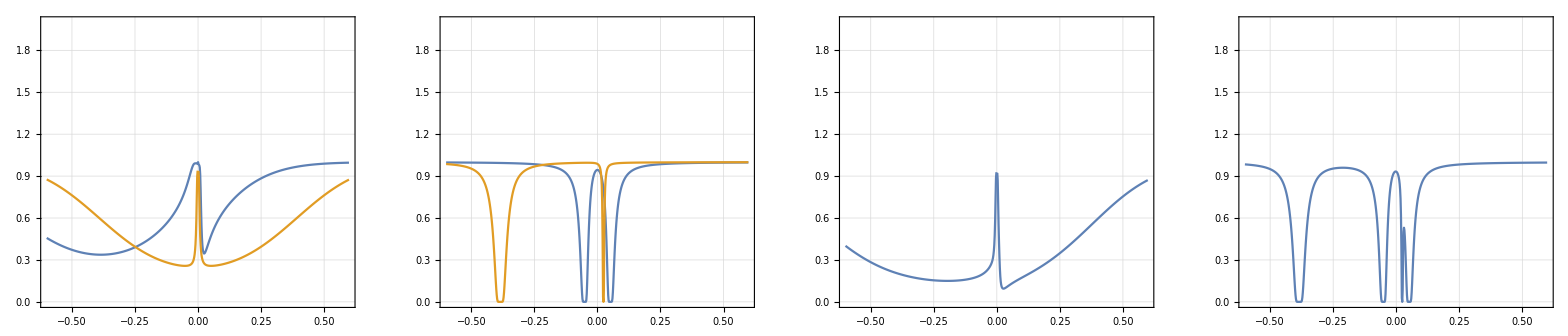

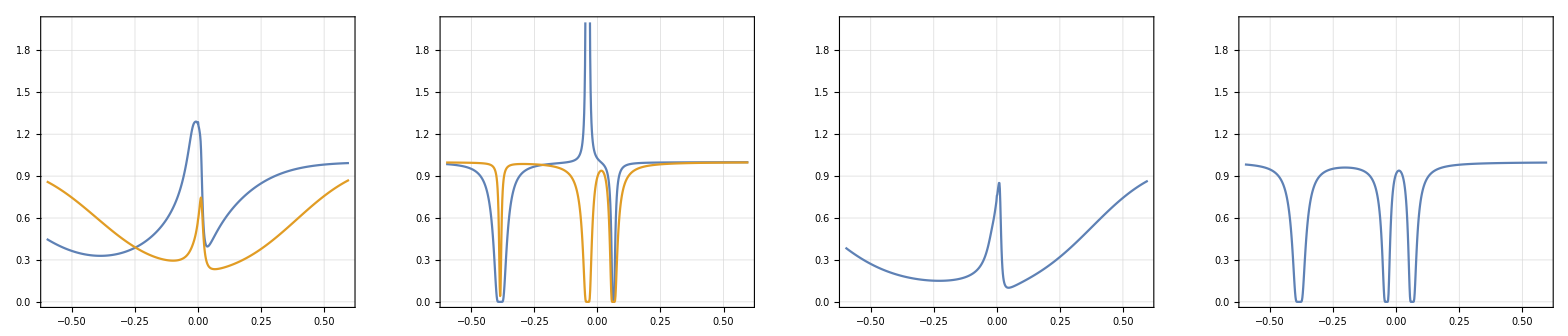

```mathematica
Off[General::unfl]
Off[General::stop]
Off[General::ovfl]
Off[Mean::rectt]
Off[Part::pkspec1]
Off[ListPlot::prng]
Off[Set::pkspec1]
p=200
GraphicsRow[{ListPlot[Select[Lev3DoppTestsc6[50,p/1000,1/1000,0.5*10^6,0,0,0],#[[1,2]]∈Reals&&0<#[[1,2]]<100&],Joined->True,Frame->True,Axes->False,PlotRange->{0,2},GridLines->Automatic,ImageSize->500],ListPlot[Select[Lev3Testsc6[50,p/1000,1/1000,0.5*10^6,0,0],#[[1,2]]∈Reals&&0<#[[1,2]]<100&],Joined->True,Frame->True,Axes->False,PlotRange->{0,2},GridLines->Automatic,ImageSize->500],
ListPlot[Lev3DoppTestsc6[50,p/1000,1/1000,0.5*10^6,0,0,2],Joined->True,Frame->True,Axes->False,PlotRange->{0,2},GridLines->Automatic,ImageSize->500],
ListPlot[Select[Lev3Testsc6[50,p/1000,1/1000,0.5*10^6,0,2],#[[2]]∈Reals&&0<#[[2]]<100&],Joined->True,Frame->True,Axes->False,PlotRange->{0,2},GridLines->Automatic,ImageSize->500]}]
GraphicsRow[{ListPlot[Select[Lev4DoppTestsc6[50,p/1000,1/1000,0.5*10^6,0,0,0],#[[1,2]]∈Reals&&0<#[[1,2]]<100&],Joined->True,Frame->True,Axes->False,PlotRange->{0,2},GridLines->Automatic,ImageSize->500],ListPlot[Select[Lev4Testsc6[50,p/1000,1/1000,0.5*10^6,0,0],#[[1,2]]∈Reals&&0<#[[1,2]]<100&],Joined->True,Frame->True,Axes->False,PlotRange->{0,2},GridLines->Automatic,ImageSize->500],
ListPlot[Select[Lev4DoppTestsc6[50,p/1000,1/1000,0.5*10^6,0,0,2],#[[2]]∈Reals&&0<#[[2]]<100&],Joined->True,Frame->True,Axes->False,PlotRange->{0,2},GridLines->Automatic,ImageSize->500],ListPlot[Select[Lev4Testsc6[50,p/1000,1/1000,0.5*10^6,0,2],#[[2]]∈Reals&&0<#[[2]]<100&],Joined->True,Frame->True,Axes->False,PlotRange->{0,2},GridLines->Automatic,ImageSize->500]}]
```

## γ vs FWHM

Module

```mathematica
Lev4DoppTestsc3[T_,P_,diam_,gam_,delt_,kia_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Δ2,d31,d41},
d=(kia+Flatten[{Range[-0.3,0.0006,0.0001],Range[-0.000599,0.000599,0.00001],Range[0.0006,0.3,0.0001]}])*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

If[ab==0,
(*{Transpose[{d/10^9,Im[sd24[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd23[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}],
Transpose[{d/10^9,Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}]
}*)

Transpose[{d/10^9,Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}]
,
(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}]*)
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]}]
]]
```

```mathematica
Lev3DoppTestsc3[T_,P_,diam_,gam_,delt_,kia_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},

d=(kia+Flatten[{Range[-0.3,0.0006,0.0001],Range[-0.000599,0.000599,0.00001],Range[0.0006,0.3,0.0001]}])*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 
If[ab==0,
(*{Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
}*)
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],

(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}],*)
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}]
]]
```

P=20

```mathematica
$Pre=Quiet
```

Quiet

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

a

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

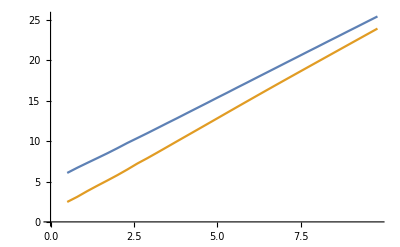

```mathematica
f={};
g={};
Off[Power::infy];
Off[Infinity::indet];
Off[General::ovfl];
Off[General::unfl];
Do[
d3d=Lev3DoppTestsc3[50,20/1000,1/1000,k*10^6,0*10^6,0,0];
d3d0=Lev3DoppTestsc3[50,0/1000,1/1000,k*10^6,0*10^6,0,0];
d3d2=Select[Transpose[{d3d[[All,1]],d3d[[All,2]]-d3d0[[All,2]]}],-100<#[[2]]&];
d3d1=Select[Transpose[{d3d2[[All,1]],MedianFilter[d3d2[[All,2]],10]}],#[[2]]∈Reals&];
nlm=NonlinearModelFit[d3d1,a 1/(b (1+(-c+x)^2/b^2))+d,{{a,0.5},{b,0.00001},{c,0},{d,0}},x];
FWHM=Differences[Solve[nlm[x]==Min[d3d1[[All,2]]]/2,x][[All,1,2]]][[1]]*10^9;
f=Append[f,{k,FWHM*10^-6}];
,{k,0.5,10,0.3}]
Print[a];
Do[
d3d=Lev4DoppTestsc3[50,20/1000,1/1000,k*10^6,0*10^6,0,0];
d3d0=Lev4DoppTestsc3[50,0/1000,1/1000,k*10^6,0*10^6,0,0];
d3d2=Select[Transpose[{d3d[[All,1]],d3d[[All,2]]-d3d0[[All,2]]}],-100<#[[2]]&];
d3d1=Select[Transpose[{d3d2[[All,1]],MedianFilter[d3d2[[All,2]],10]}],#[[2]]∈Reals&];
nlm=NonlinearModelFit[d3d1,a 1/(b (1+(-c+x)^2/b^2))+d,{{a,0.5},{b,0.00001},{c,0},{d,0}},x];
FWHM=Differences[Solve[nlm[x]==Min[d3d1[[All,2]]]/2,x][[All,1,2]]][[1]]*10^9;
g=Append[g,{k,FWHM*10^-6}];
,{k,0.5,10,0.3}]
ListPlot[{g,f},Joined->True]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

a

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

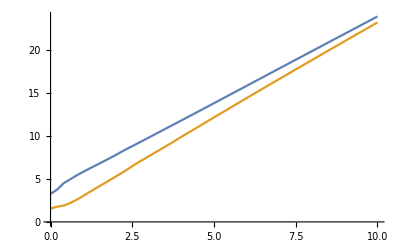

```mathematica
f1={};
g1={};
Off[Power::infy];
Off[Infinity::indet];
Off[General::ovfl];
Off[General::unfl];
Do[
d3d=Lev3DoppTestsc3[50,20/1000,1/1000,k*10^6,0*10^6,0,1];
d3d0=Lev3DoppTestsc3[50,0/1000,1/1000,k*10^6,0*10^6,0,1];
d3d2=Select[Transpose[{d3d[[All,1]],d3d[[All,2]]-d3d0[[All,2]]}],#[[2]]<1&];
d3d1=Select[Transpose[{d3d2[[All,1]],MedianFilter[d3d2[[All,2]],10]}],#[[2]]∈Reals&];
nlm=NonlinearModelFit[d3d1,a 1/(b (1+(-c+x)^2/b^2))+d,{{a,0.5},{b,0.00001},{c,0},{d,0}},x];
FWHM=Differences[Solve[nlm[x]==Max[d3d1[[All,2]]]/2,x][[All,1,2]]][[1]]*10^9;
f1=Append[f1,{k,FWHM*10^-6}];
,{k,0,10,0.2}]
Print[a];
Do[
d3d=Lev4DoppTestsc3[50,20/1000,1/1000,k*10^6,0*10^6,0,1];
d3d0=Lev4DoppTestsc3[50,0/1000,1/1000,k*10^6,0*10^6,0,1];
d3d2=Select[Transpose[{d3d[[All,1]],d3d[[All,2]]-d3d0[[All,2]]}],#[[2]]<1&];
d3d1=Select[Transpose[{d3d2[[All,1]],MedianFilter[d3d2[[All,2]],10]}],#[[2]]∈Reals&];
nlm=NonlinearModelFit[d3d1,a 1/(b (1+(-c+x)^2/b^2))+d,{{a,0.5},{b,0.00001},{c,0},{d,0}},x];
FWHM=Differences[Solve[nlm[x]==Max[d3d1[[All,2]]]/2,x][[All,1,2]]][[1]]*10^9;
g1=Append[g1,{k,FWHM*10^-6}];
,{k,0,10,0.2}]
ListPlot[{g1,f1},Joined->True]
```

P=γ=0.5

```mathematica
$Pre=Quiet
```

NonlinearModelFit::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

Part::partw: Part 1 of {} does not exist.

Differences::listrp: List or SparseArray or StructuredArray expected at position 1 in Differences[{{}}⟦All,1,2⟧].

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

a

NonlinearModelFit::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

Part::partw: Part 1 of {} does not exist.

Differences::listrp: List or SparseArray or StructuredArray expected at position 1 in Differences[{{}}⟦All,1,2⟧].

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

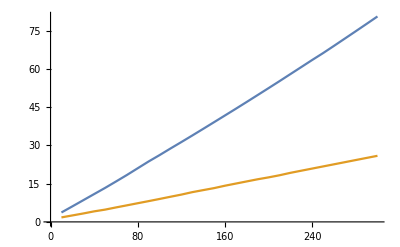

```mathematica
f3={};
g3={};
Off[Power::infy];
Off[Infinity::indet];
Off[General::ovfl];
Off[General::unfl];
Do[
d3d=Lev3DoppTestsc3[50,k/1000,1/1000,0.5*10^6,0*10^6,0,0];
d3d0=Lev3DoppTestsc3[50,0/1000,1/1000,0.5*10^6,0*10^6,0,0];
d3d2=Select[Transpose[{d3d[[All,1]],d3d[[All,2]]-d3d0[[All,2]]}],-1<#[[2]]<1&];
d3d1=Select[Transpose[{d3d2[[All,1]],MedianFilter[d3d2[[All,2]],30]}],#[[2]]∈Reals&];
nlm=NonlinearModelFit[d3d1,a 1/(b (1+(-c+x)^2/b^2))+d,{{a,0},{b,0.00005},{c,0},{d,0}},x,ConfidenceLevel->.99,MaxIterations->1000];
FWHM=Differences[Solve[nlm[x]==Min[d3d1[[All,2]]]/2,x][[All,1,2]]][[1]]*10^9;
f3=Append[f3,{k,FWHM*10^-6}];
,{k,0,300,10}]
Print[a];
Do[
d3d=Lev4DoppTestsc3[50,k/1000,1/1000,0.5*10^6,0*10^6,0,0];
d3d0=Lev4DoppTestsc3[50,0/1000,1/1000,0.5*10^6,0*10^6,0,0];
d3d2=Select[Transpose[{d3d[[All,1]],d3d[[All,2]]-d3d0[[All,2]]}],-1<#[[2]]<1&];
d3d1=Select[Transpose[{d3d2[[All,1]],MedianFilter[d3d2[[All,2]],30]}],#[[2]]∈Reals&];
nlm=NonlinearModelFit[d3d1,a 1/(b (1+(-c+x)^2/b^2))+d,{{a,0},{b,0.00005},{c,0},{d,0}},x,ConfidenceLevel->.99,MaxIterations->1000];
FWHM=Differences[Solve[nlm[x]==Min[d3d1[[All,2]]]/2,x][[All,1,2]]][[1]]*10^9;
g3=Append[g3,{k,FWHM*10^-6}];
,{k,0,300,10}]
ListPlot[{g3,f3},Joined->True]
```

```mathematica
γ
```

NonlinearModelFit::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

Part::partw: Part 1 of {} does not exist.

Differences::listrp: List or SparseArray or StructuredArray expected at position 1 in Differences[{{}}⟦All,1,2⟧].

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

a

NonlinearModelFit::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

Part::partw: Part 1 of {} does not exist.

Differences::listrp: List or SparseArray or StructuredArray expected at position 1 in Differences[{{}}⟦All,1,2⟧].

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit::sszero will be suppressed during this calculation.

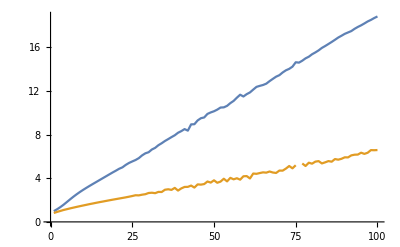

```mathematica
f4={};
g4={};
Off[Power::infy];
Off[Infinity::indet];
Off[General::ovfl];
Off[General::unfl];
Do[
d3d=Lev3DoppTestsc3[50,k/1000,1/1000,0.5*10^6,0*10^6,0,1];
d3d0=Lev3DoppTestsc3[50,0/1000,1/1000,0.5*10^6,0*10^6,0,1];
d3d2=Select[Transpose[{d3d[[All,1]],d3d[[All,2]]-d3d0[[All,2]]}],#[[2]]<1&];
d3d1=Select[Transpose[{d3d2[[All,1]],MedianFilter[d3d2[[All,2]],30]}],#[[2]]∈Reals&];
nlm=NonlinearModelFit[d3d1,a 1/(b (1+(-c+x)^2/b^2))+d,{{a,0},{b,0.00005},{c,0},{d,0}},x,ConfidenceLevel->.99,MaxIterations->1000];
FWHM=Differences[Solve[nlm[x]==Max[d3d1[[All,2]]]/2,x][[All,1,2]]][[1]]*10^9;
f4=Append[f4,{k,FWHM*10^-6}];
,{k,0,100,1}]
Print[a];
Do[
d3d=Lev4DoppTestsc3[50,k/1000,1/1000,0.5*10^6,0*10^6,0,1];
d3d0=Lev4DoppTestsc3[50,0/1000,1/1000,0.5*10^6,0*10^6,0,1];
d3d2=Select[Transpose[{d3d[[All,1]],d3d[[All,2]]-d3d0[[All,2]]}],#[[2]]<1&];
d3d1=Select[Transpose[{d3d2[[All,1]],MedianFilter[d3d2[[All,2]],30]}],#[[2]]∈Reals&];
nlm=NonlinearModelFit[d3d1,a 1/(b (1+(-c+x)^2/b^2))+d,{{a,0},{b,0.00005},{c,0},{d,0}},x,ConfidenceLevel->.99,MaxIterations->1000];
FWHM=Differences[Solve[nlm[x]==Max[d3d1[[All,2]]]/2,x][[All,1,2]]][[1]]*10^9;
g4=Append[g4,{k,FWHM*10^-6}];
,{k,0,100,1}]
ListPlot[{g4,f4},Joined->True]
```

1.76303×10^6

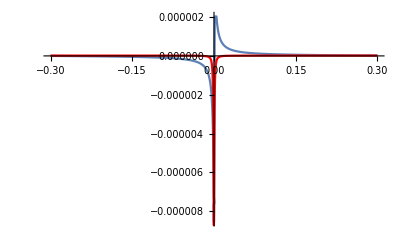

```mathematica
d3d=Lev3DoppTestsc3[50,10/1000,1/1000,0.5*10^6,0*10^6,0,0];
d3d0=Lev3DoppTestsc3[50,0/1000,1/1000,0.5*10^6,0*10^6,0,0];
d3d2=Select[Transpose[{d3d[[All,1]],d3d[[All,2]]-d3d0[[All,2]]}],-1<#[[2]]<1&];
d3d1=Select[Transpose[{d3d2[[All,1]],MedianFilter[d3d2[[All,2]],30]}],#[[2]]∈Reals&];
nlm=NonlinearModelFit[d3d1,a 1/(b (1+(-c+x)^2/b^2))+d,{{a,0},{b,0.00005},{c,0},{d,0}},x,ConfidenceLevel->.99,MaxIterations->1000];
FWHM=Differences[Solve[nlm[x]==Min[d3d1[[All,2]]]/2,x][[All,1,2]]][[1]]*10^9
Show[ListPlot[d3d1,Joined->True,PlotRange->All],Plot[nlm[x],{x,-0.3,0.3},PlotRange->All,PlotStyle->Red]]
```

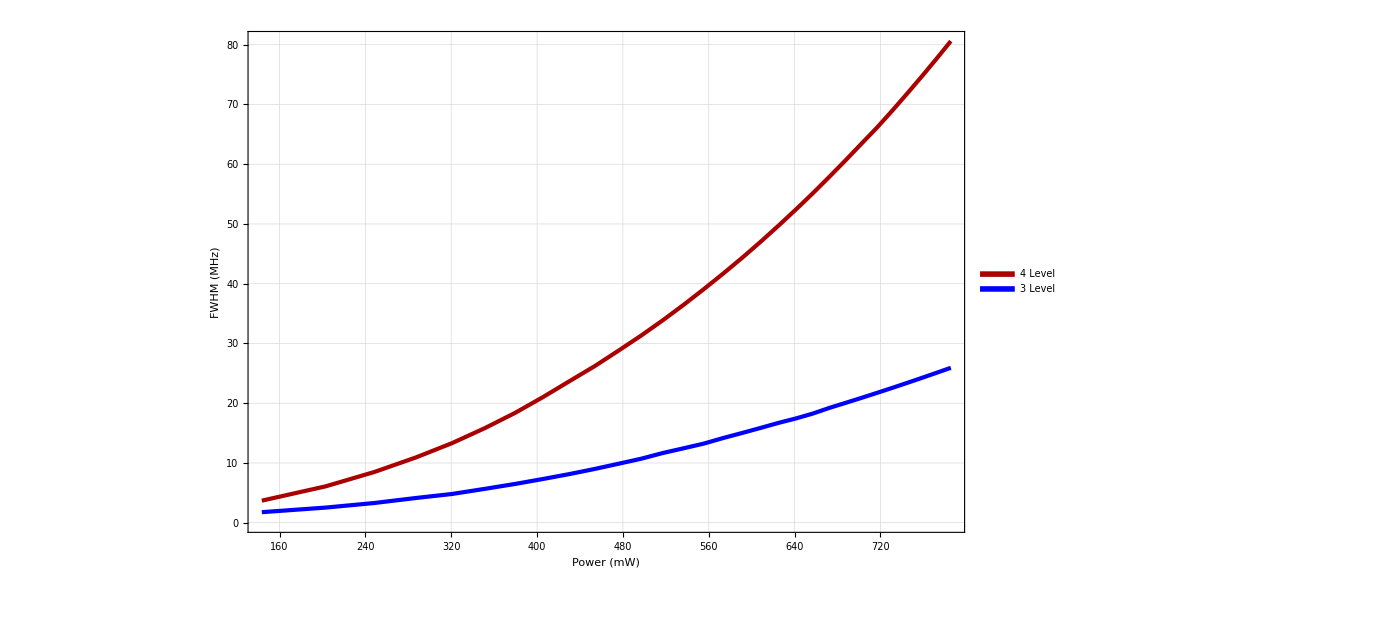

```mathematica
legend=LineLegend[Thread[Directive[{Darker[Red],Blue,{Darker[Gray],Dashed}},AbsoluteThickness[10]]],{Style["4 Level",Darker[Red]],Style["3 Level",Blue]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->45}];
pp1=ListPlot[{Transpose[{Om[g3[[All,1]]/1000]*10^-6,g3[[All,2]]//Chop}],Transpose[{Om[f3[[All,1]]/1000]*10^-6,f3[[All,2]]//Chop}]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,0.4}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Power (mW)",50,Black],Style["FWHM (MHz) ",50,Black]},GridLines->Automatic]
```

## Plot For Poster

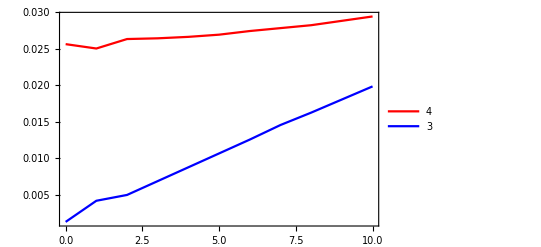

```mathematica
Show[ListPlot[f2,Joined->True,PlotStyle->Red,PlotLegends->{"4"},Frame->True,Axes->False,PlotRange->All],ListPlot[f1,Joined->True,PlotStyle->Blue,PlotLegends->{"3"}],PlotRange->All]
```

```mathematica
SetDirectory["C:\\Users\\Admin\\Qsync\\PersonalFolders\\Saesun\\Poster"]
```

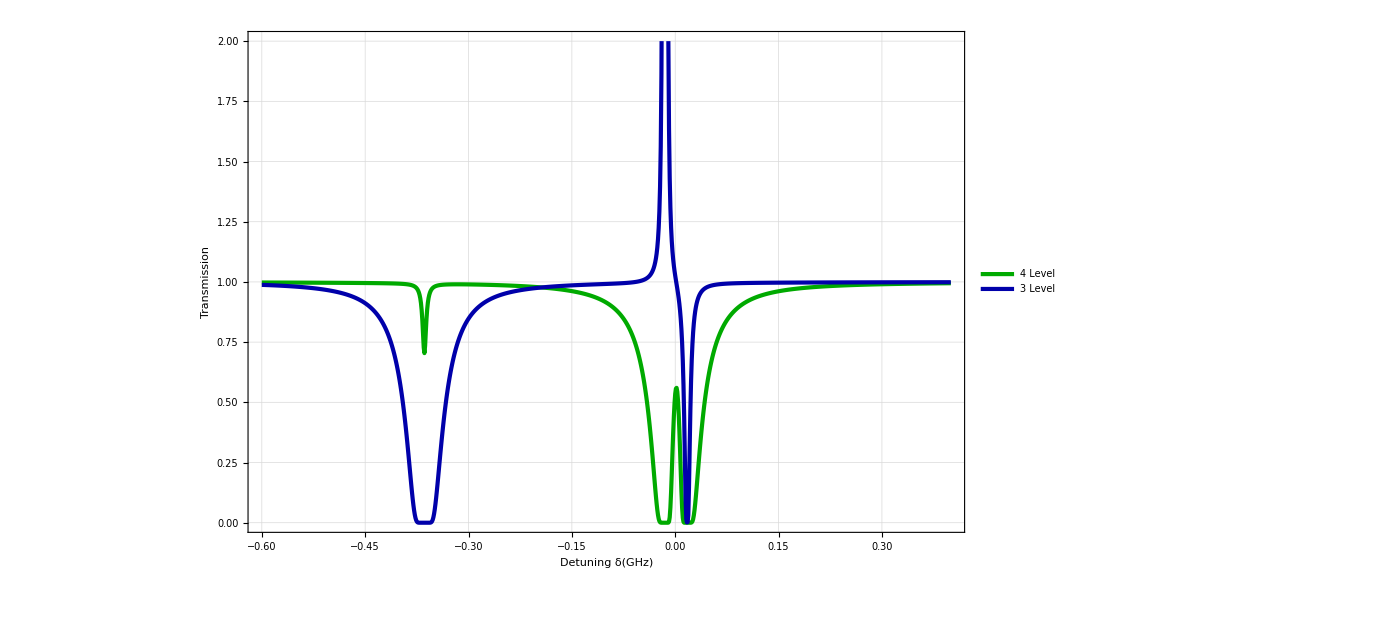

```mathematica
p=20;
p2=ListPlot[Lev4Testsc[50,p/1000,1/1000,0.5*10^6,0*10^6,2],Joined->True,FrameTicks->True,FrameTicksStyle->Directive[30],Frame->True,Axes->False,PlotLegends->Placed[LineLegend[{"4 Level","3 Level"},LegendFunction->"Frame",LabelStyle->{FontSize->35}],{Right,Center}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Green]},{AbsoluteThickness[3],Darker[Blue]},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Detuning δ(GHz)",20,Black],Style["Transmission ",20,Black]},GridLines->Automatic,PlotRange->{0,2}]
```

```mathematica
->
```

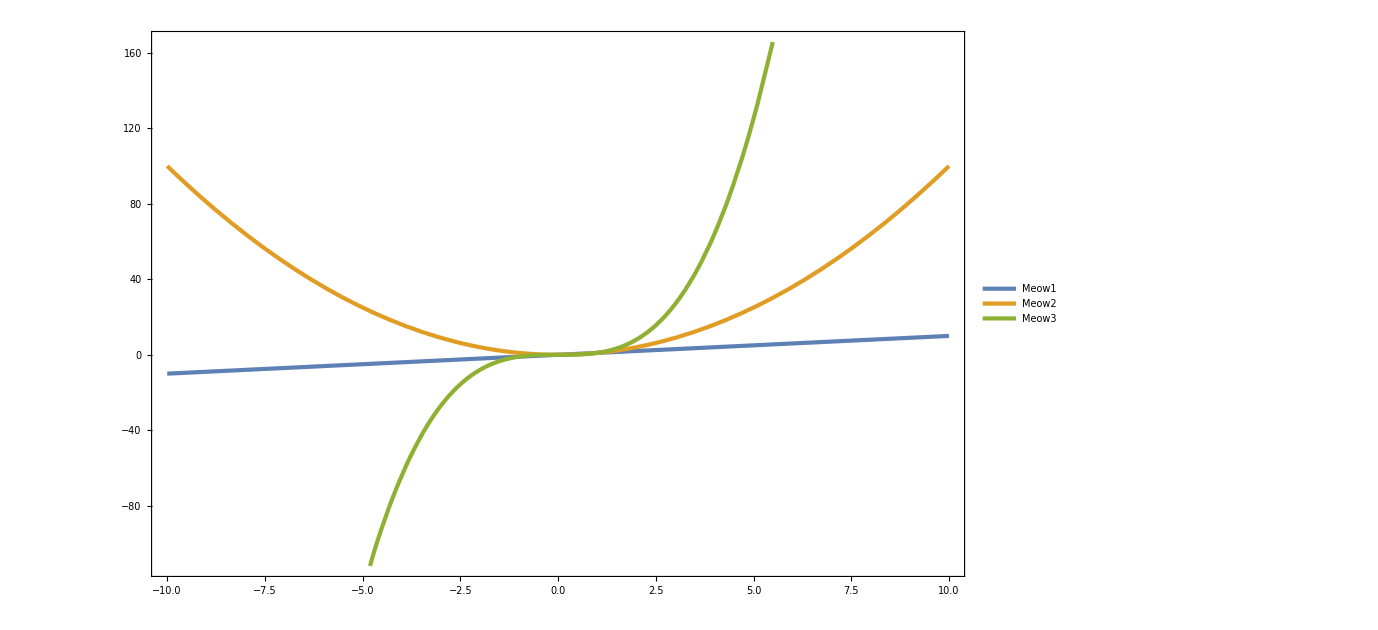

```mathematica
Plot[{x,x^2,x^3},{x,-10,10},Frame->True,Axes->False,ImageSize->1020,PlotStyle->AbsoluteThickness[3],
PlotLegends->Placed[LineLegend[{"Meow1","Meow2","Meow3"},LegendFunction->"Frame",LabelStyle->{FontSize->50}],{Right,Bottom}]]
```

```mathematica
Plot[{x,x^2,x^3},{x,-10,10},Frame->True,Axes->False,ImageSize->1020,PlotStyle->AbsoluteThickness[3],PlotLegends->Placed[legend,{Right,Bottom}]]
```

SetDirectory::cdir: Cannot set current directory to C:\Users\Admin\Qsync\PersonalFolders\Saesun\Poster.

$Failed

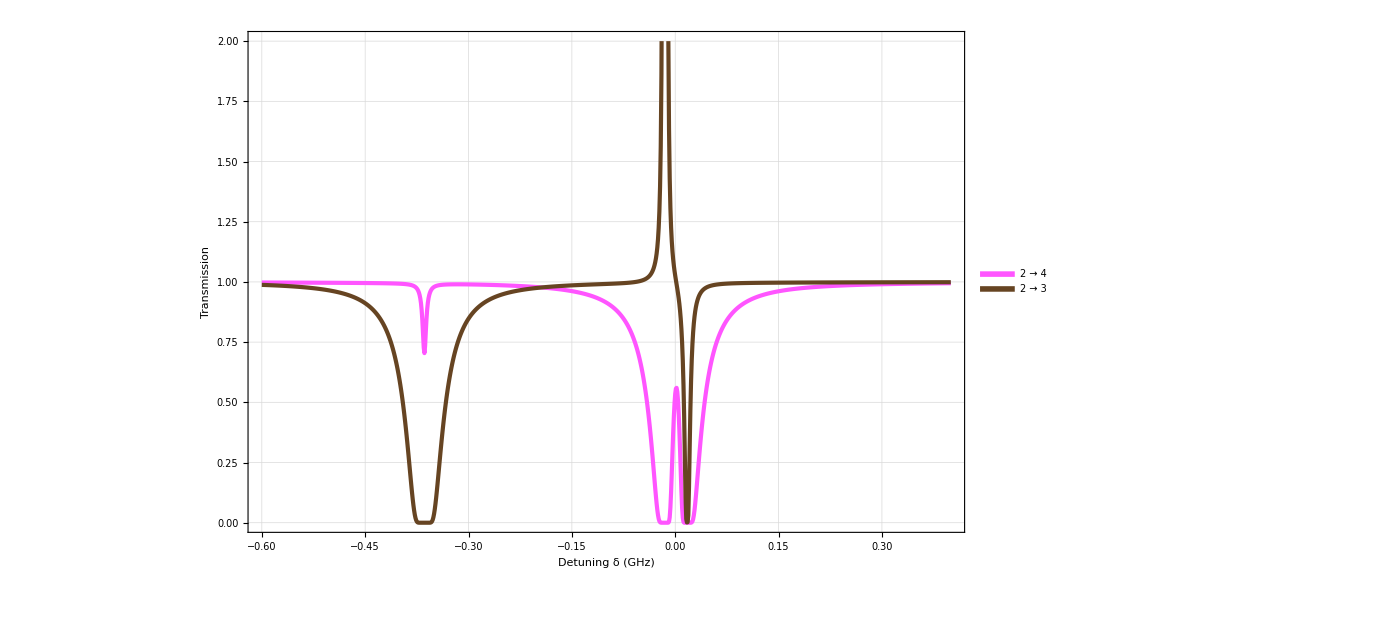

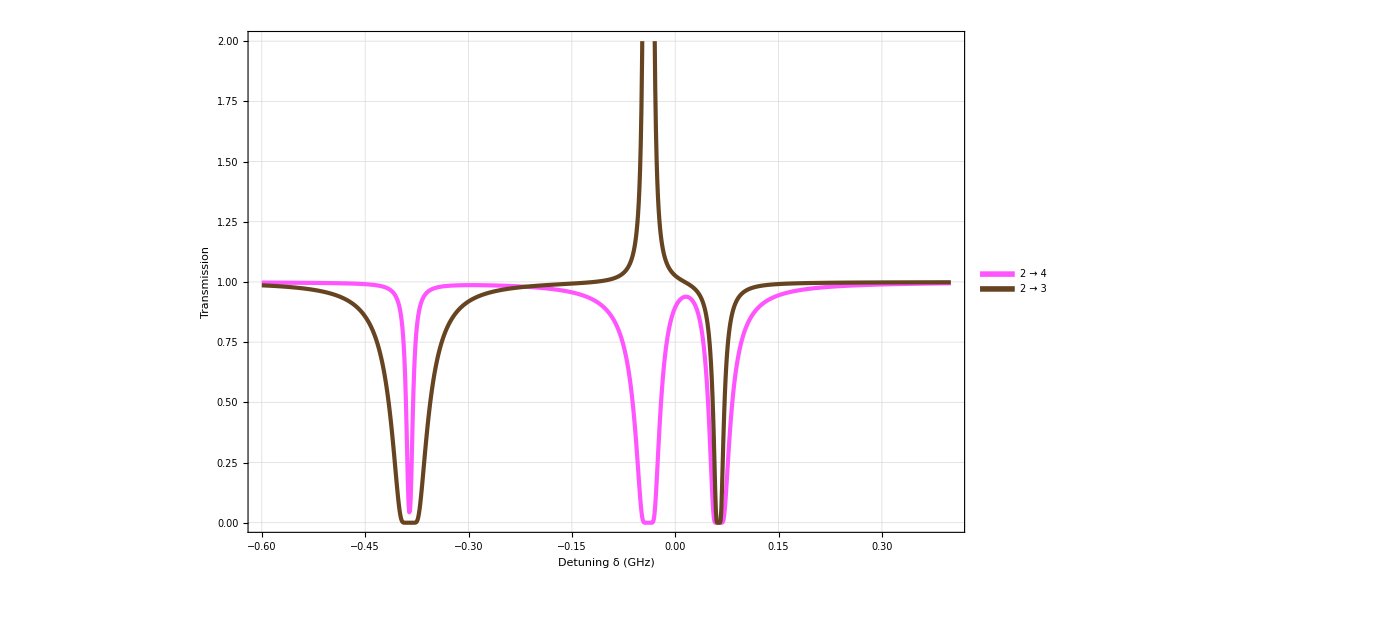

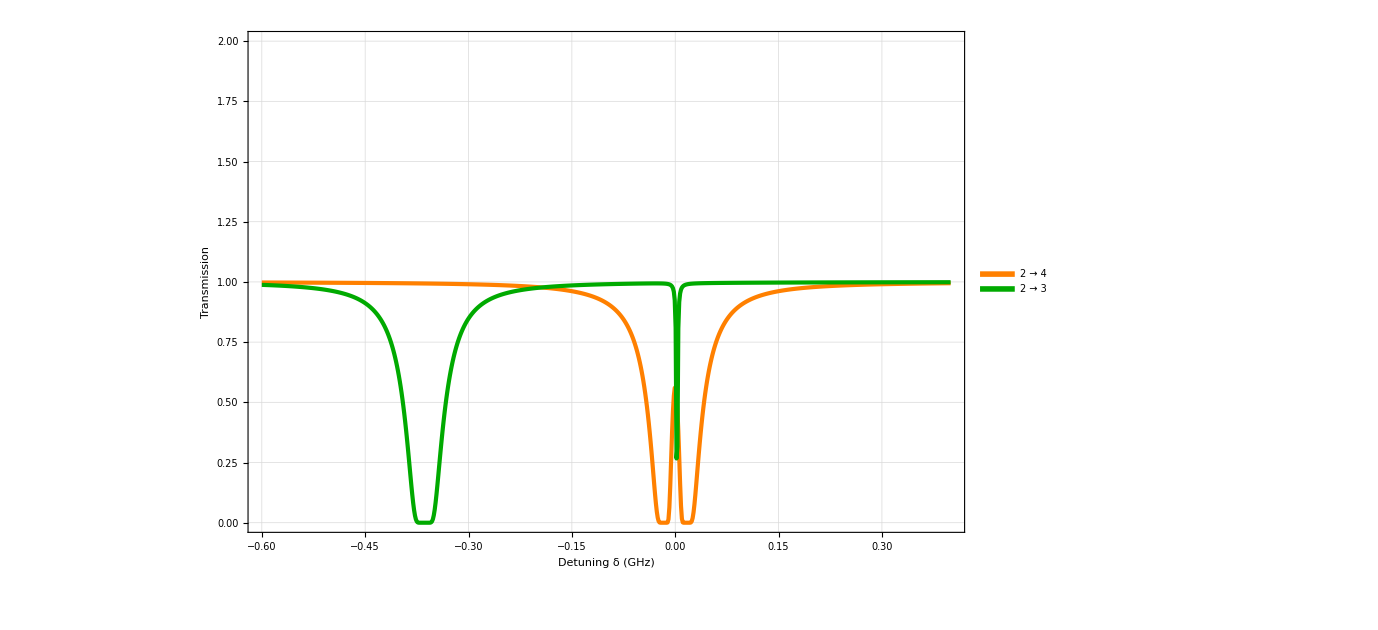

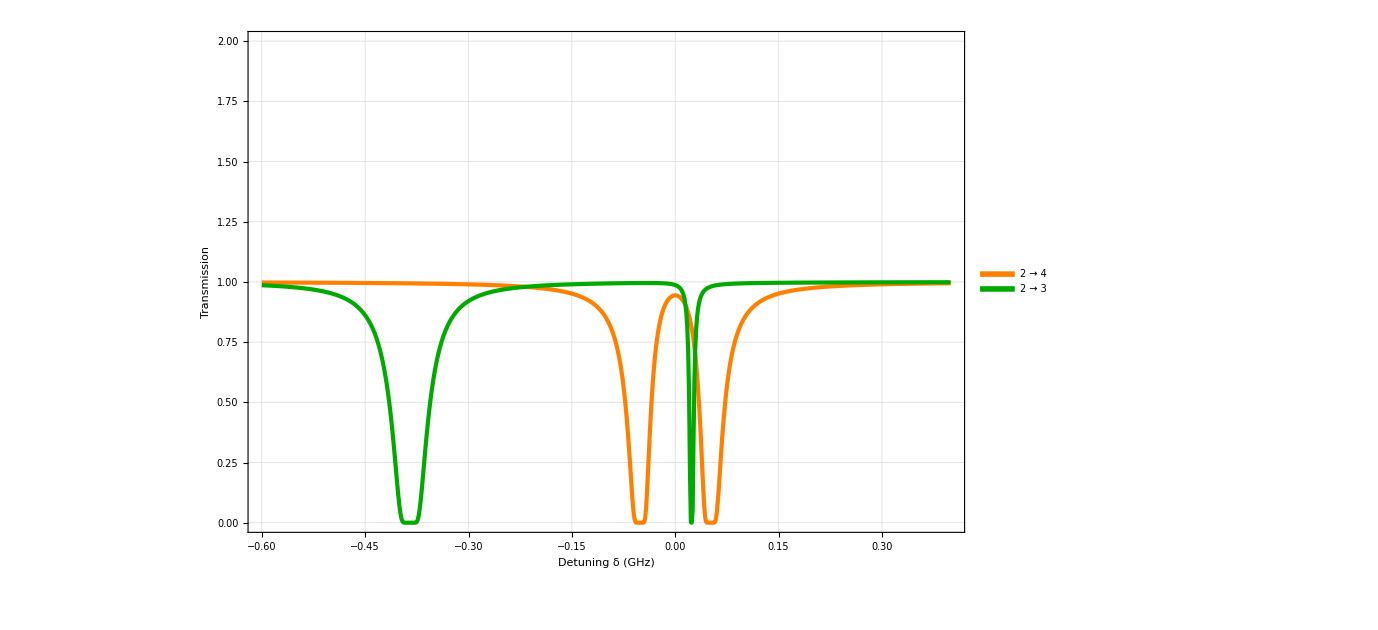

```mathematica
SetDirectory["C:\\Users\\Admin\\Qsync\\PersonalFolders\\Saesun\\Poster"]
p=20;
legend=LineLegend[Thread[Directive[{Lighter[Magenta],Darker[Brown]},AbsoluteThickness[10]]],{Style["2 → 4",Lighter[Magenta]],Style["2 → 3",Darker[Brown]]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->50}]
final4=ListPlot[Lev4Testsc[50,p/1000,1/1000,0.5*10^6,0*10^6,2],Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,Top}],ImageSize->1020,PlotStyle->{{AbsoluteThickness[3],Lighter[Magenta]},{AbsoluteThickness[3],Darker[Brown]},{AbsoluteThickness[3],Black,Dashed},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Detuning δ (GHz)",50,Black],Style["Transmission ",50,Black]},GridLines->Automatic,PlotRange->{{-0.6,0.4},{0,2}}]
p=200;
legend=LineLegend[Thread[Directive[{Lighter[Magenta],Darker[Brown]},AbsoluteThickness[10]]],{Style["2 → 4",Lighter[Magenta]],Style["2 → 3",Darker[Brown]]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->50}]
final5=ListPlot[Lev4Testsc[50,p/1000,1/1000,0.5*10^6,0*10^6,2],Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,Top}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Lighter[Magenta]},{AbsoluteThickness[3],Darker[Brown]},{AbsoluteThickness[3],Black,Dashed},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Detuning δ (GHz)",50,Black],Style["Transmission ",50,Black]},GridLines->Automatic,PlotRange->{{-0.6,0.4},{0,2}}]
p=20;
legend=LineLegend[Thread[Directive[{Orange,Darker[Green]},AbsoluteThickness[10]]],{Style["2 → 4",Orange],Style["2 → 3",Darker[Green]]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->50}]
final6=ListPlot[Lev3Testsc[50,p/1000,1/1000,0.5*10^6,0*10^6,2],Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,Top}],ImageSize->1020,PlotStyle->{{AbsoluteThickness[3],Orange},{AbsoluteThickness[3],Darker[Green]},{AbsoluteThickness[3],Black,Dashed},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Detuning δ (GHz)",50,Black],Style["Transmission ",50,Black]},GridLines->Automatic,PlotRange->{{-0.6,0.4},{0,2}}]
p=200;
legend=LineLegend[Thread[Directive[{Orange,Darker[Green]},AbsoluteThickness[10]]],{Style["2 → 4",Orange],Style["2 → 3",Darker[Green]]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->50}]
final7=ListPlot[Lev3Testsc[50,p/1000,1/1000,0.5*10^6,0*10^6,2],Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,Top}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Orange},{AbsoluteThickness[3],Darker[Green]},{AbsoluteThickness[3],Black,Dashed},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Detuning δ (GHz)",50,Black],Style["Transmission ",50,Black]},GridLines->Automatic,PlotRange->{{-0.6,0.4},{0,2}}]
```

```mathematica
Manipulate[
p=20;
ListPlot[Lev4Testsc[50,p/1000,1/1000,0.5*10^6,Δ*10^6,0],Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[LineLegend[{"4 Level 2 → 4","4 Level 2 → 3"},LegendFunction->"Frame",LabelStyle->{FontSize->36}],{Right,Top}],ImageSize->1020,PlotStyle->{{AbsoluteThickness[3],Lighter[Magenta]},{AbsoluteThickness[3],Darker[Brown]},{AbsoluteThickness[3],Black,Dashed},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Detuning δ (GHz)",50,Black],Style["Transmission ",50,Black]},GridLines->Automatic,PlotRange->{{-0.6,0.4},{0,2}}]

,{Δ,-600,400}]
```

```mathematica
Export["Meow00001.jpg",p1]
```

Meow00001.jpg

```mathematica
SetDirectory["E:\\QOLab\\PersonalFolders\\Saesun\\Poster"]
Export["Meow0a01.jpg",final4]
Export["Meow0a02.jpg",final5]
Export["Meow0a03.jpg",final6]
Export["Meow0a04.jpg",final7]
```

E:\QOLab\PersonalFolders\Saesun\Poster

Meow0a01.jpg

Meow0a02.jpg

Meow0a03.jpg

Meow0a04.jpg

```mathematica
Export["Meow5.jpg",p1]
Export["Meow6.jpg",p2]
```

Meow5.jpg

Meow6.jpg

```mathematica
Manipulate[
p=20;
ListPlot[Lev4DoppTestsc[50,p/1000,1/1000,0*10^6,Δ*10^6,0],Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[LineLegend[{"4 Level 2 → 4","4 Level 2 → 3"},LegendFunction->"Frame",LabelStyle->{FontSize->36}],{Right,Top}],ImageSize->1020,PlotStyle->{{AbsoluteThickness[3],Lighter[Magenta]},{AbsoluteThickness[3],Darker[Brown]},{AbsoluteThickness[3],Black,Dashed},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Detuning δ (GHz)",50,Black],Style["Transmission ",50,Black]},GridLines->Automatic,PlotRange->{0,1}]





,{Δ,-600,400}]
```

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

Power::infy: Infinite expression 1/(0.+0. ⅈ)^2 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

Power::infy: Infinite expression 1/(0.+0. ⅈ)^2 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

Power::infy: Infinite expression 1/(0.+0. ⅈ)^2 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

Power::infy: Infinite expression 1/(0.+0. ⅈ)^2 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

## Testing

```mathematica
Lev4Testsc[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41,Δ2},
d=Range[-2,2,0.005]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(d42^2 Nat ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(2 √5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ32=-(d32^2 Nat ((-35+2 √70) omegac1^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)))/(5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ24=(d42^2 Nat (ⅈ (4 √5-5 √14) omegac1^2+16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)))/(2 √5 e0 (8 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ) (w43+ⅈ γ42+δ+Δ)+ⅈ omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)) ℏ);
χ23=(d32^2 Nat ((35 √2-4 √35) omegac1^2-40 ⅈ √2 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ)))/(5 √2 e0 (omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))) ℏ);

If[ab==0,
(*{Transpose[{d/10^9,Im[χ24]}],
Transpose[{d/10^9,Im[χ42]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
}*)Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}],
(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]*)
If[ab==3,
{Transpose[{d/10^9,
(Im[χ32])
}],
Transpose[{d/10^9,
(Im[χ42])
}]},
{Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ32])]
}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42])]
}]}
]]
]
```

```mathematica
Lev4DoppTestsc[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Δ2,d31,d41},
d=Range[-2,2,0.005]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

If[ab==0,
(*{Transpose[{d/10^9,Im[sd24[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd23[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}],
Transpose[{d/10^9,Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}]
}*)
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}]

,
(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}]*)
If[ab==3,
{Transpose[{d/10^9,
Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]
}],
Transpose[{d/10^9,
Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]
}]},
{Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]])]
}]}
]]
]
```

```mathematica
Lev3Testsc[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41,Δ2},
d=Range[-2,2,0.0013]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(4 d42^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ+w43)-ⅈ omegac2^2) ℏ);   
χ24=(4 d42^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ+w43)+ⅈ omegac2^2) ℏ);   
χ32=(4 d32^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ)-ⅈ omegac1^2) ℏ);   
χ23=(4 d32^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)+ⅈ omegac1^2) ℏ); 

If[ab==0,
(*{Transpose[{d/10^9,Im[χ24]}],
Transpose[{d/10^9,Im[χ42]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
}*)
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]}],
(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]*)
If[ab==3,
Transpose[{d/10^9,
(Im[χ42]+Im[χ32])}],
{Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ32])]
}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42])]
}]}
]]
]
```

```mathematica
Lev3DoppTestsc[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},
d=Range[-2,2,0.0013]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 
If[ab==0,
(*{Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
}*)Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}],

(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}]*)
If[ab==3,
Transpose[{d/10^9,
(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])}],
{
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]])]}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
}
]]]
```

```mathematica
Manipulate[
p1=ListPlot[{Lev3DoppTestsc[50,p/1000,1/1000,0.5*10^6,δ*10^6,0],Lev3Testsc[50,p/1000,1/1000,0.5*10^6,δ*10^6,1][[1]],Lev3Testsc[50,p/1000,1/1000,0.5*10^6,δ*10^6,1][[2]]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[LineLegend[{"4 Level 2 → 4","4 Level 2 → 3"},LegendFunction->"Frame",LabelStyle->{FontSize->36}],{Right,Top}],ImageSize->1020,PlotStyle->{{AbsoluteThickness[3],Lighter[Magenta]},{AbsoluteThickness[3],Darker[Brown]},{AbsoluteThickness[3],Black,Dashed},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Detuning δ (GHz)",50,Black],Style["Transmission ",50,Black]},GridLines->Automatic,PlotRange->{0,2}]

,{δ,-600,600},{p,0,3000}]
```

General::unfl: Underflow occurred in computation.

General::ovfl: Overflow occurred in computation.

Statistics`Library`MatrixRowTranslate::ovfl: Overflow occurred in computation.

Set::pkspec1: The expression {5,15,25,24,34,33,32,42,43,44,45,Overflow[],41,51,52,53,63,64,65,75,85,95,35,55,54,31} cannot be used as a part specification.

General::unfl: Underflow occurred in computation.

```mathematica
Manipulate[
p1=ListPlot[{Lev4DoppTestsc[50,p/1000,1/1000,0.5*10^6,δ*10^6,0],Lev4Testsc[50,p/1000,1/1000,0.5*10^6,δ*10^6,1][[1]],Lev4Testsc[50,p/1000,1/1000,0.5*10^6,δ*10^6,1][[2]]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[LineLegend[{"4 Level 2 → 4","4 Level 2 → 3"},LegendFunction->"Frame",LabelStyle->{FontSize->36}],{Right,Top}],ImageSize->1020,PlotStyle->{{AbsoluteThickness[3],Lighter[Magenta]},{AbsoluteThickness[3],Darker[Brown]},{AbsoluteThickness[3],Black,Dashed},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Detuning δ (GHz)",50,Black],Style["Transmission ",50,Black]},GridLines->Automatic,PlotRange->{0,2}]

,{δ,-600,600},{p,0,3000}]
```

```mathematica
PlotR
```

```mathematica
Clear[δ]
(d42^2 Nat ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(2 √5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ)/.Δ->0
```

(d42^2 Nat ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ δ)))/(2 √5 e0 (8 (γ21+ⅈ δ) (γ32+ⅈ δ) (w43-ⅈ γ42+δ)+omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ)) ℏ)

```mathematica
sol=D[(d42^2 Nat ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ δ)))/(2 √5 e0 (8 (γ21+ⅈ δ) (γ32+ⅈ δ) (w43-ⅈ γ42+δ)+omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ)) ℏ),δ]//FullSimplify
```

(d42^2 Nat (16 ⅈ √5 (γ21+γ32+2 ⅈ δ) (8 (γ21+ⅈ δ) (γ32+ⅈ δ) (w43-ⅈ γ42+δ)+omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ))-((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ δ)) (9 omegac1^2+8 (γ21 γ32+γ21 γ42+γ32 γ42+ⅈ w43 (γ21+γ32+2 ⅈ δ)+2 ⅈ (γ21+γ32+γ42) δ-3 δ^2))))/(2 √5 e0 (8 (γ21+ⅈ δ) (γ32+ⅈ δ) (w43-ⅈ γ42+δ)+omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ))^2 ℏ)

```mathematica
SetDirectory["E:\\QOLab\\PersonalFolders\\Saesun\\Poster"]
```

E:\QOLab\PersonalFolders\Saesun\Poster

```mathematica
Export["Final4a.jpg",final4,ImageSize-> 2000]
Export["Final5a.jpg",final5,ImageSize-> 2000]
Export["Final6a.jpg",final6,ImageSize-> 2000]
Export["Final7a.jpg",final7,ImageSize-> 2000]
```

```mathematica
Export["Final0a.jpg",final0,ImageSize-> 2000]
Export["Final1a.jpg",final1,ImageSize-> 2000]
Export["Final2a.jpg",final2,ImageSize-> 2000]
Export["Final3a.jpg",final3,ImageSize-> 2000]
```

Final0a.jpg

Final1a.jpg

Final2a.jpg

Final3a.jpg

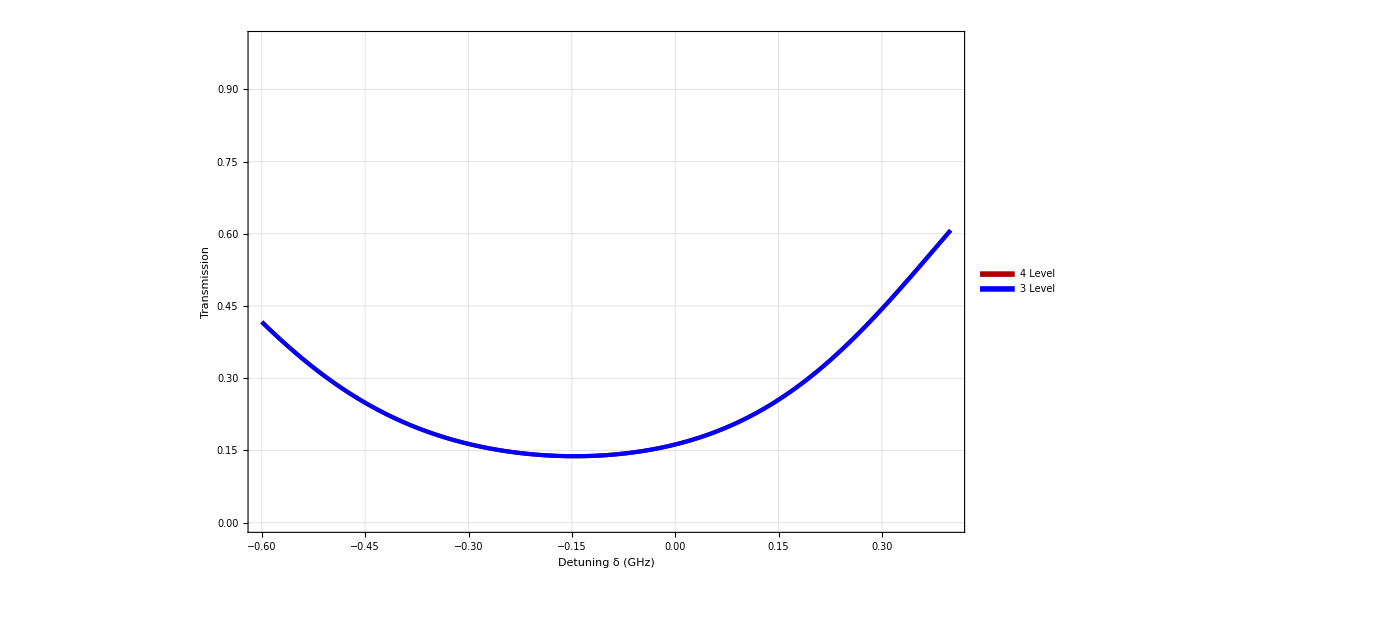

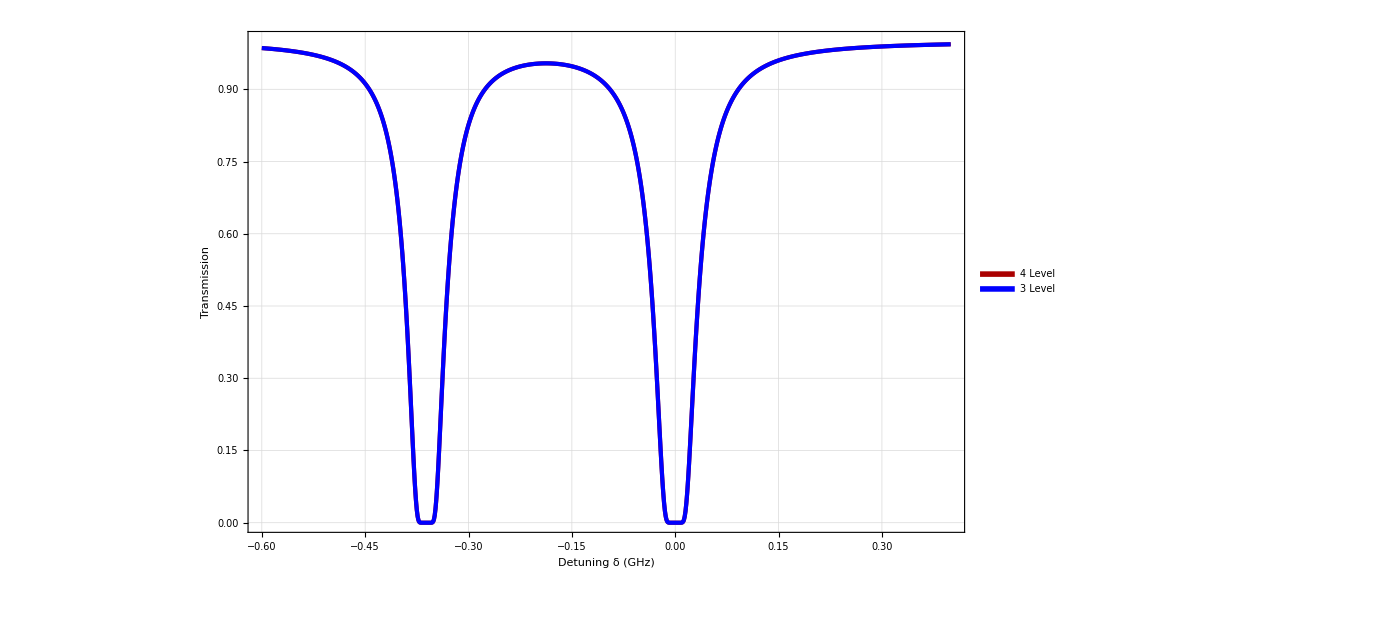

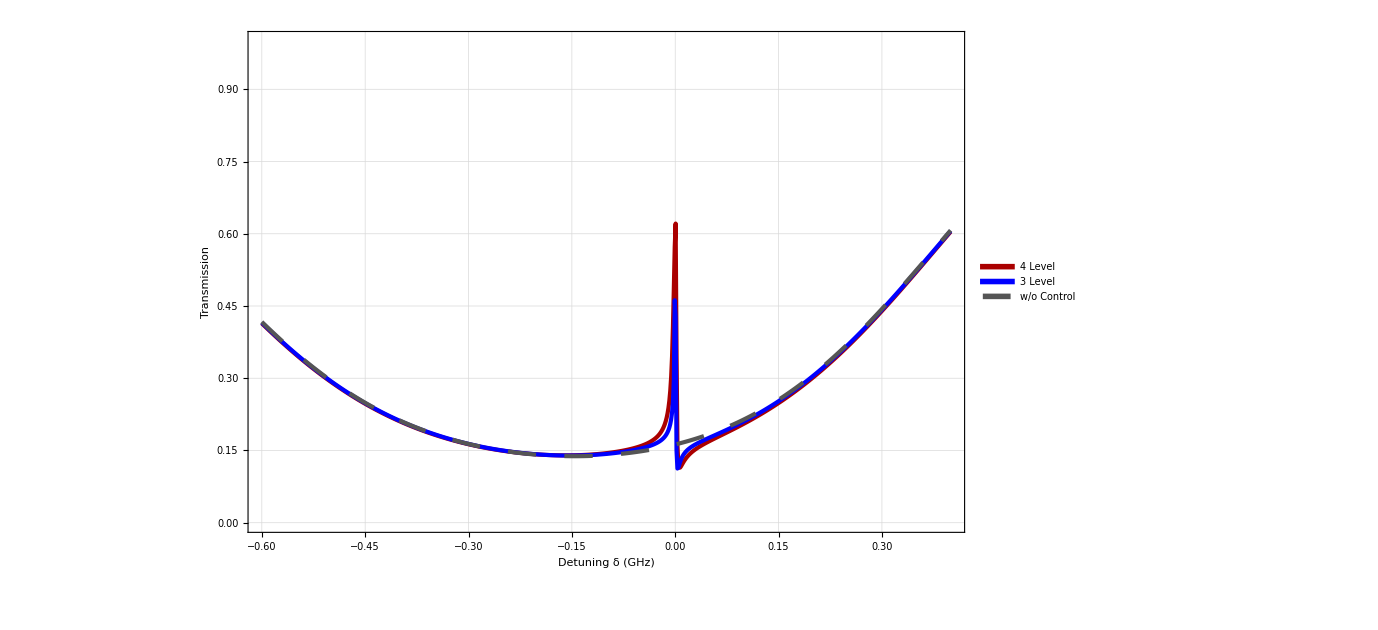

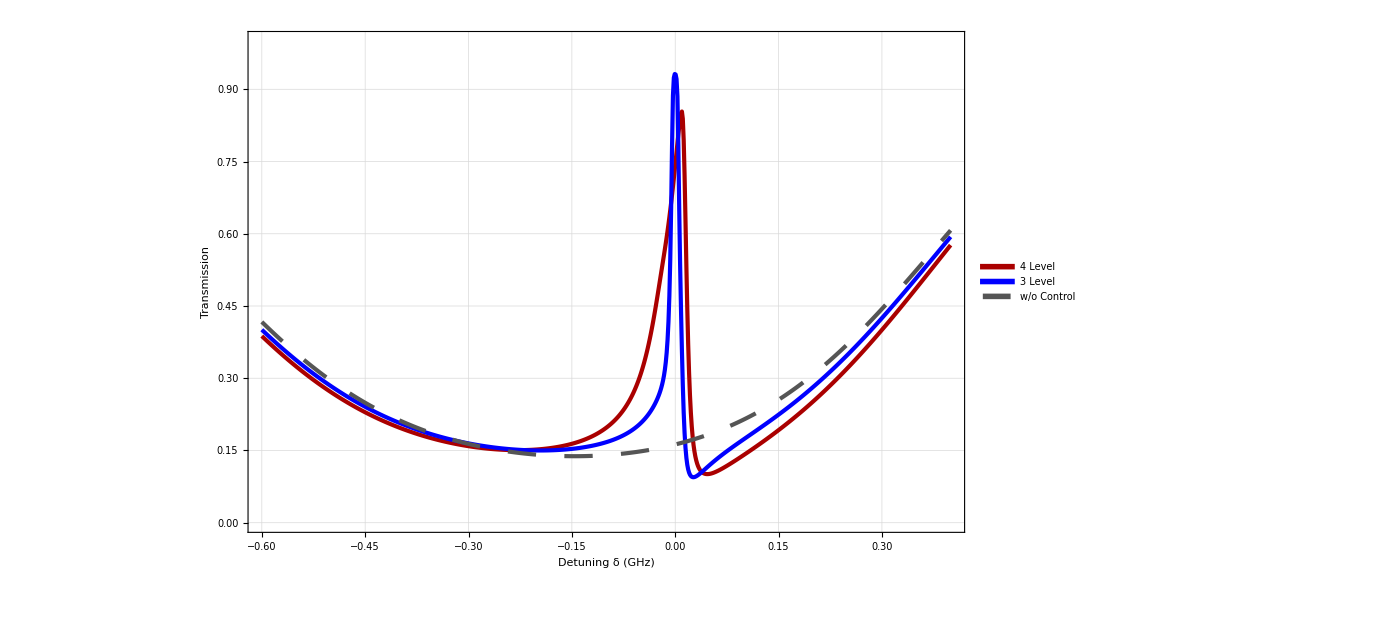

```mathematica
p=0;
legend=LineLegend[Thread[Directive[{Darker[Red],Blue,{Darker[Gray],Dashed}},AbsoluteThickness[10]]],{Style["4 Level",Darker[Red]],Style["3 Level",Blue]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->45}];
final1=ListPlot[{Lev4DoppTestsc[50,p/1000,1/1000,0.5*10^6,0*10^6,0],Lev3DoppTestsc[50,p/1000,1/1000,0.5*10^6,0*10^6,0]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,Top}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Darker[Gray],Dashing[.02]},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Detuning δ (GHz)",50,Black],Style["Transmission ",50,Black]},GridLines->Automatic,PlotRange->{{-0.6,0.4},{0,1}}]
final0=ListPlot[{Lev4Testsc[50,p/1000,1/1000,0.5*10^6,0*10^6,0],Lev3Testsc[50,p/1000,1/1000,0.5*10^6,0*10^6,0]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,Center}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Detuning δ (GHz)",50,Black],Style["Transmission ",50,Black]},GridLines->Automatic,PlotRange->{{-0.6,0.4},{0,1}}]
p=20;
legend=LineLegend[Thread[Directive[{Darker[Red],Blue,{Darker[Gray],Dashed}},AbsoluteThickness[10]]],{Style["4 Level",Darker[Red]],Style["3 Level",Blue],Style["w/o Control",Darker[Gray]]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->45}];
final2=ListPlot[{Lev4DoppTestsc[50,p/1000,1/1000,0.5*10^6,0*10^6,0],Lev3DoppTestsc[50,p/1000,1/1000,0.5*10^6,0*10^6,0],Lev3DoppTestsc[50,0/1000,1/1000,0.5*10^6,0*10^6,0]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,Top}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Darker[Gray],Dashing[.02]},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Detuning δ (GHz)",50,Black],Style["Transmission ",50,Black]},GridLines->Automatic,PlotRange->{{-0.6,0.4},{0,1}}]
p=200;
legend=LineLegend[Thread[Directive[{Darker[Red],Blue,{Darker[Gray],Dashed}},AbsoluteThickness[10]]],{Style["4 Level",Darker[Red]],Style["3 Level",Blue],Style["w/o Control",Darker[Gray]]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->45}];
final3=ListPlot[{Lev4DoppTestsc[50,p/1000,1/1000,0.5*10^6,0*10^6,0],Lev3DoppTestsc[50,p/1000,1/1000,0.5*10^6,0*10^6,0],Lev3DoppTestsc[50,0/1000,1/1000,0.5*10^6,0*10^6,0]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,Top}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Darker[Gray],Dashing[.02]},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Detuning δ (GHz)",50,Black],Style["Transmission ",50,Black]},GridLines->Automatic,PlotRange->{{-0.6,0.4},{0,1}}]
```

```mathematica
Exp
```

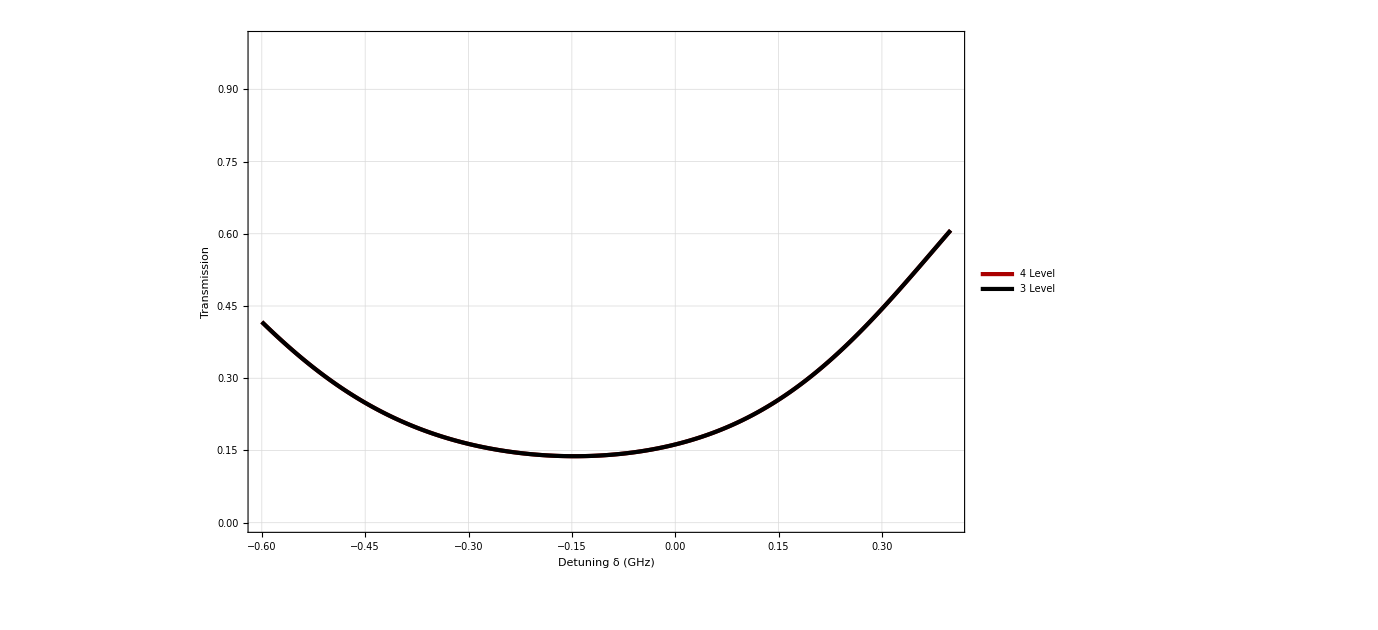

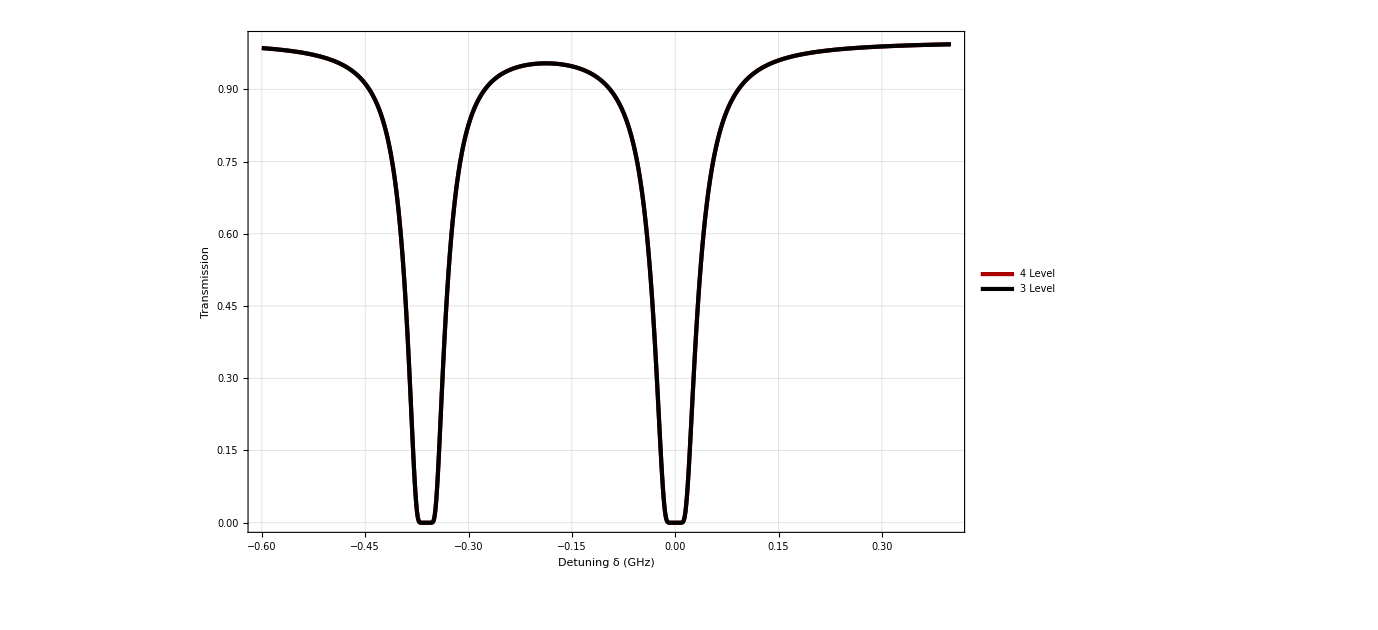

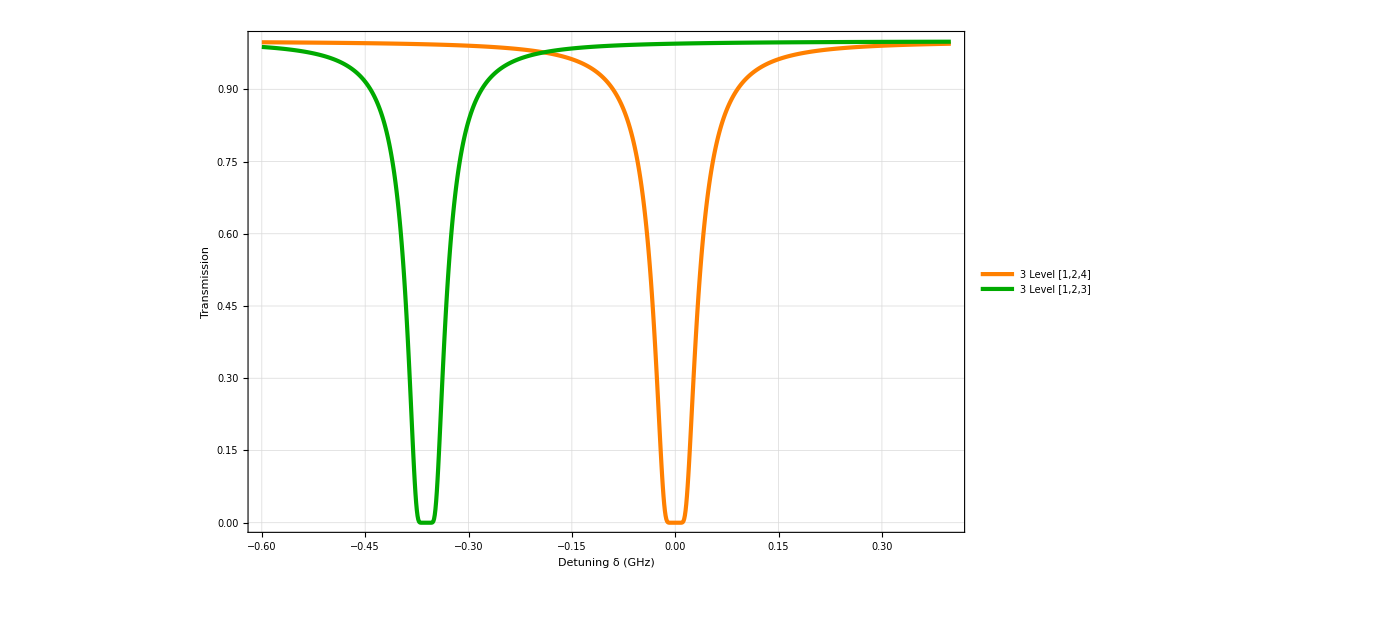

```mathematica
p=0;
p1=ListPlot[{Lev4DoppTestsc[50,p/1000,1/1000,0.5*10^6,0*10^6,0],Lev3DoppTestsc[50,p/1000,1/1000,0.5*10^6,0*10^6,0]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[LineLegend[{"4 Level","3 Level"},LegendFunction->"Frame",LabelStyle->{FontSize->36}],{Right,Top}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Darker[Black]},{AbsoluteThickness[3],Black,Dashed},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Detuning δ (GHz)",50,Black],Style["Transmission ",50,Black]},GridLines->Automatic,PlotRange->{{-0.6,0.4},{0,1}}]
p2=ListPlot[{Lev4Testsc[50,p/1000,1/1000,0.5*10^6,0*10^6,0],Lev3Testsc[50,p/1000,1/1000,0.5*10^6,0*10^6,0]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[LineLegend[{"4 Level","3 Level"},LegendFunction->"Frame",LabelStyle->{FontSize->36}],{Right,Center}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Darker[Black]},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Detuning δ (GHz)",50,Black],Style["Transmission ",50,Black]},GridLines->Automatic,PlotRange->{{-0.6,0.4},{0,1}}]
p3=ListPlot[{Lev3Testsc[50,p/1000,1/1000,0.5*10^6,0*10^6,1][[1]],Lev3Testsc[50,p/1000,1/1000,0.5*10^6,0*10^6,1][[2]]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[LineLegend[{"3 Level [1,2,4] ","3 Level [1,2,3]"},LegendFunction->"Frame",LabelStyle->{FontSize->34}],{Right,Center}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Orange},{AbsoluteThickness[3],Darker[Green]},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Detuning δ (GHz)",50,Black],Style["Transmission ",50,Black]},GridLines->Automatic,PlotRange->{{-0.6,0.4},{0,1}}]
```

```mathematica
Manipulate[ListPlot[{Lev4DoppTestsc[50,p/1000,1/1000,γ*10^6,0*10^6,0],Lev3DoppTestsc[50,p/1000,1/1000,γ*10^6,0*10^6,0]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[30],Frame->True,Axes->False,PlotLegends->Placed[LineLegend[{"4 Level","3 Level"},LegendFunction->"Frame",LabelStyle->{FontSize->35}],{Right,Bottom}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Darker[Black]},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Detuning Δ(GHz)",20,Black],Style["Transmission ",20,Black]},GridLines->Automatic]
,{p,0,100},{γ,0,10}]
```

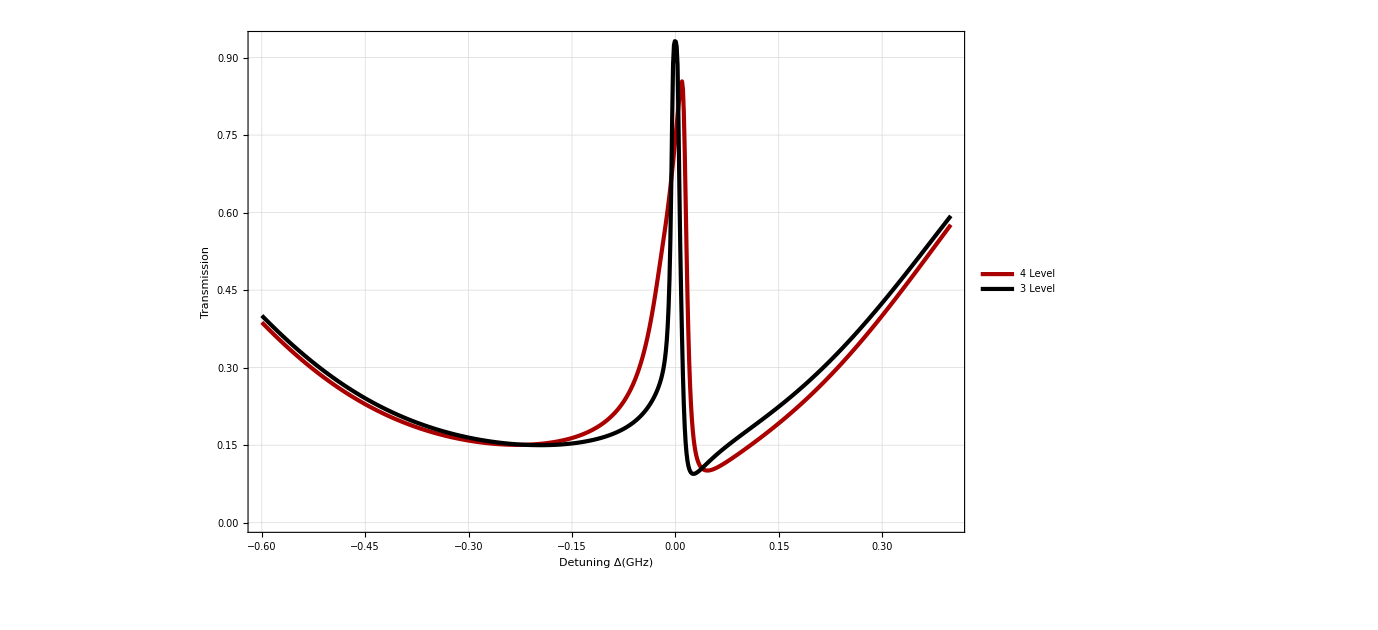

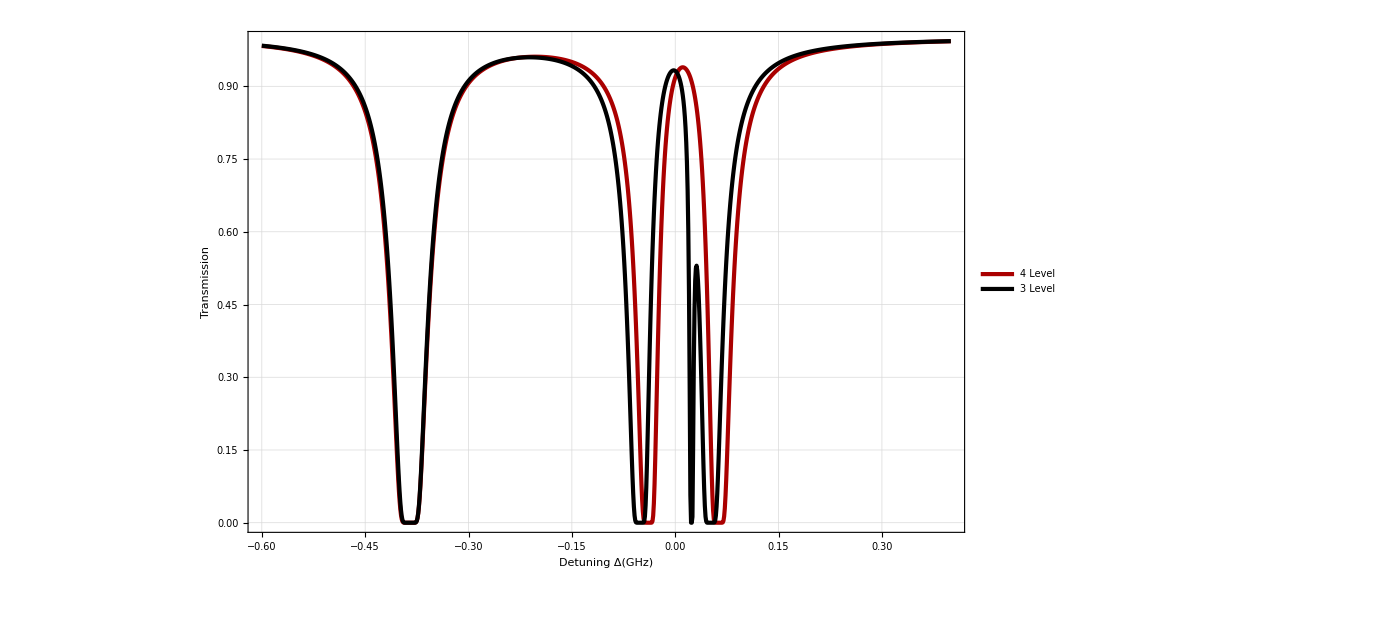

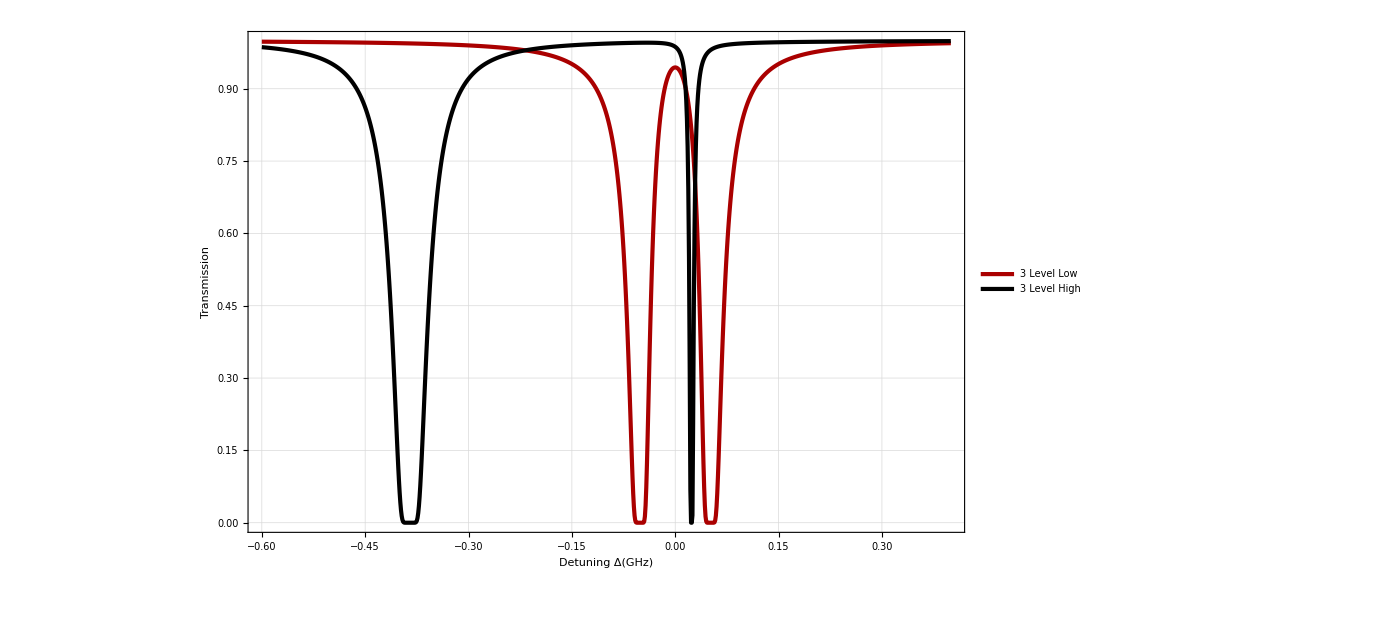

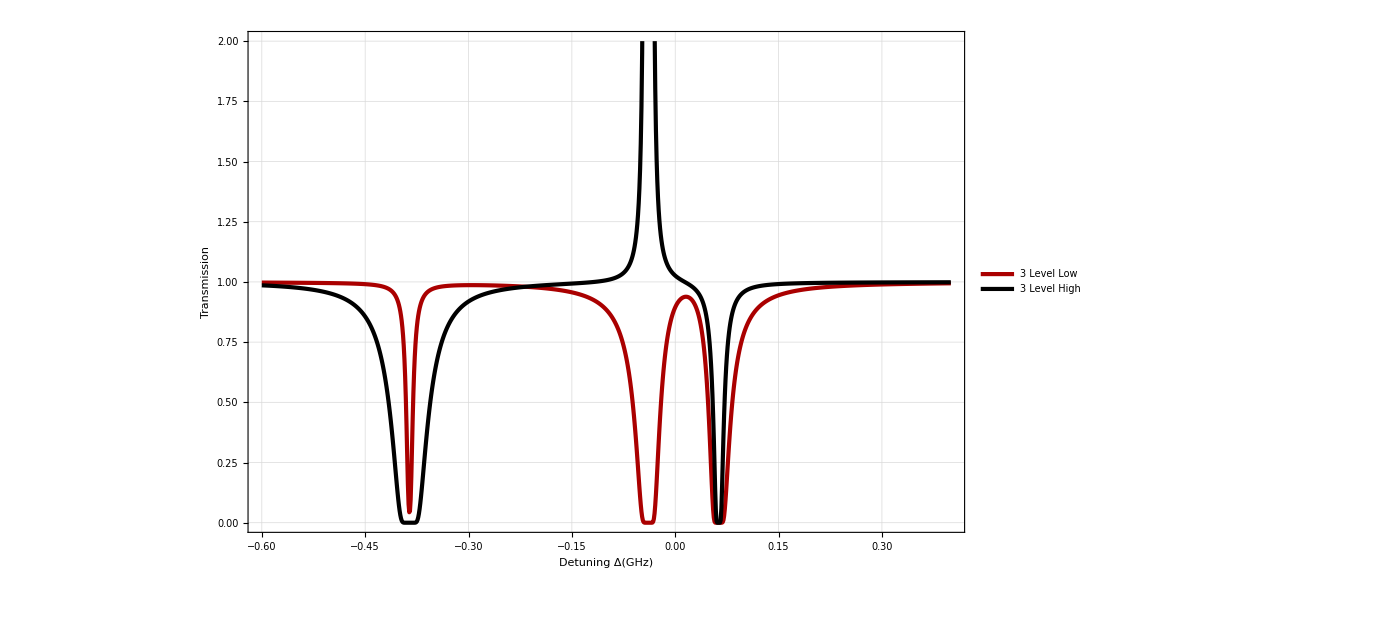

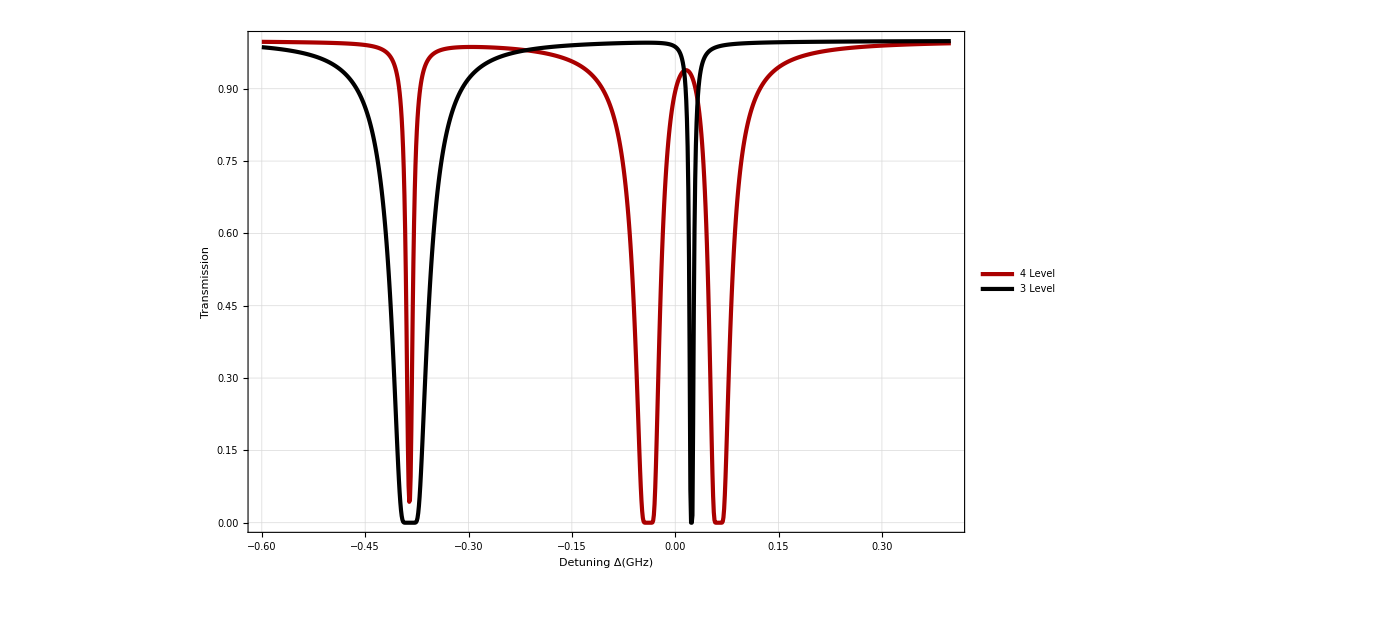

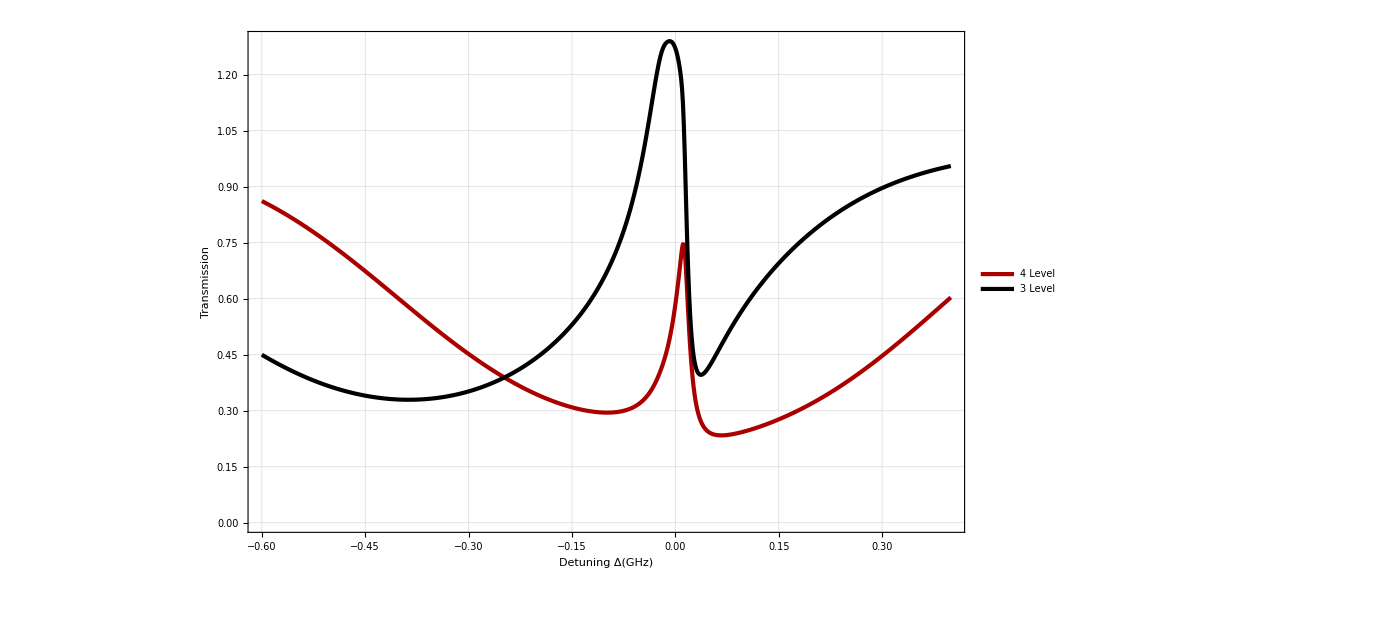

```mathematica
p=200;
δ=0;
p1=ListPlot[{Lev4DoppTestsc[50,p/1000,1/1000,0.5*10^6,δ*10^6,0],Lev3DoppTestsc[50,p/1000,1/1000,0.5*10^6,δ*10^6,0]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[30],Frame->True,Axes->False,PlotLegends->Placed[LineLegend[{"4 Level","3 Level"},LegendFunction->"Frame",LabelStyle->{FontSize->35}],{Right,Bottom}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Darker[Black]},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Detuning Δ(GHz)",20,Black],Style["Transmission ",20,Black]},GridLines->Automatic]
ListPlot[{Lev4Testsc[50,p/1000,1/1000,0.5*10^6,δ*10^6,0],Lev3Testsc[50,p/1000,1/1000,0.5*10^6,δ*10^6,0]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[30],Frame->True,Axes->False,PlotLegends->Placed[LineLegend[{"4 Level","3 Level"},LegendFunction->"Frame",LabelStyle->{FontSize->35}],{Right,Center}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Darker[Black]},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Detuning Δ(GHz)",20,Black],Style["Transmission ",20,Black]},GridLines->Automatic,PlotRange->All]
ListPlot[{Lev3Testsc[50,p/1000,1/1000,0.5*10^6,δ*10^6,1][[1]],Lev3Testsc[50,p/1000,1/1000,0.5*10^6,δ*10^6,1][[2]]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[30],Frame->True,Axes->False,PlotLegends->Placed[LineLegend[{"3 Level Low ","3 Level High"},LegendFunction->"Frame",LabelStyle->{FontSize->35}],{Right,Center}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Darker[Black]},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Detuning Δ(GHz)",20,Black],Style["Transmission ",20,Black]},GridLines->Automatic,PlotRange->All]
ListPlot[{Lev4Testsc[50,p/1000,1/1000,0.5*10^6,δ*10^6,1][[1]],Lev4Testsc[50,p/1000,1/1000,0.5*10^6,δ*10^6,1][[2]]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[30],Frame->True,Axes->False,PlotLegends->Placed[LineLegend[{"3 Level Low ","3 Level High"},LegendFunction->"Frame",LabelStyle->{FontSize->35}],{Right,Center}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Darker[Black]},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Detuning Δ(GHz)",20,Black],Style["Transmission ",20,Black]},GridLines->Automatic,PlotRange->{0,2}]
ListPlot[{Lev4Testsc[50,p/1000,1/1000,0.5*10^6,δ*10^6,3][[1]],Lev3Testsc[50,p/1000,1/1000,0.5*10^6,δ*10^6,1][[2]]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[30],Frame->True,Axes->False,PlotLegends->Placed[LineLegend[{"4 Level","3 Level"},LegendFunction->"Frame",LabelStyle->{FontSize->35}],{Right,Center}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Darker[Black]},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Detuning Δ(GHz)",20,Black],Style["Transmission ",20,Black]},GridLines->Automatic,PlotRange->All]
ListPlot[{Lev4DoppTestsc[50,p/1000,1/1000,0.5*10^6,δ*10^6,1][[1]],Lev4DoppTestsc[50,p/1000,1/1000,0.5*10^6,δ*10^6,1][[2]]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[30],Frame->True,Axes->False,PlotLegends->Placed[LineLegend[{"4 Level","3 Level"},LegendFunction->"Frame",LabelStyle->{FontSize->35}],{Right,Bottom}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Darker[Black]},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Detuning Δ(GHz)",20,Black],Style["Transmission ",20,Black]},GridLines->Automatic]
```

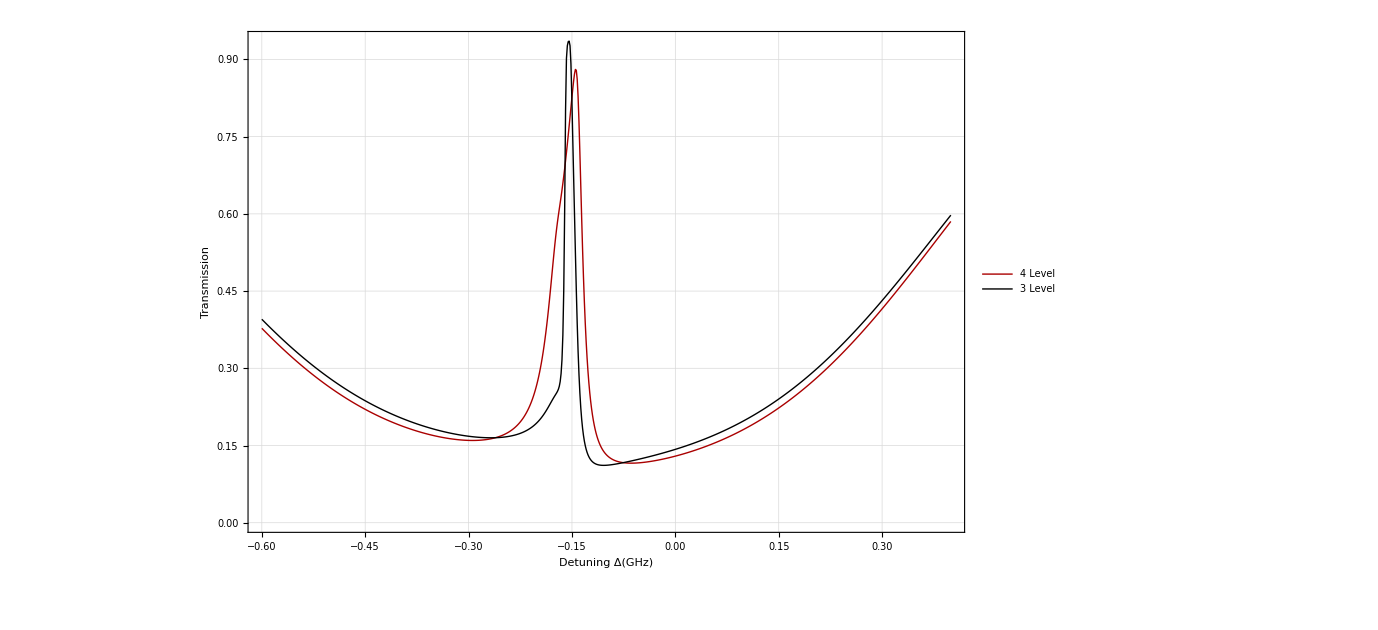

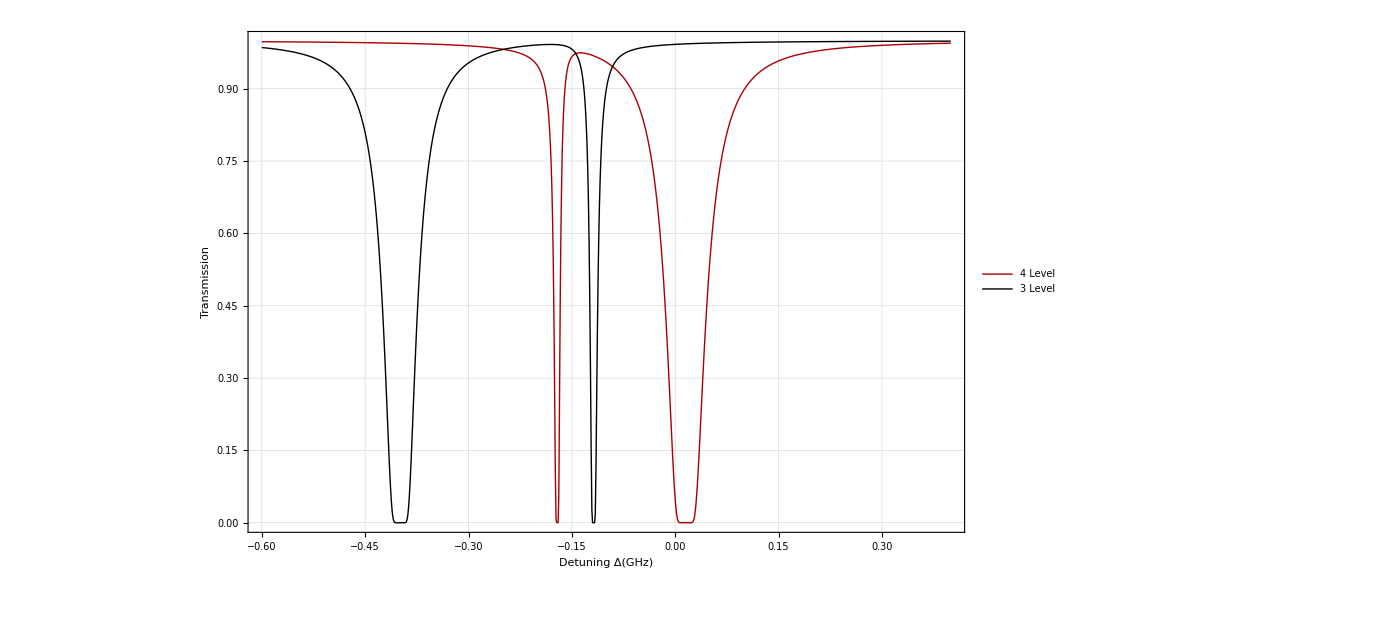

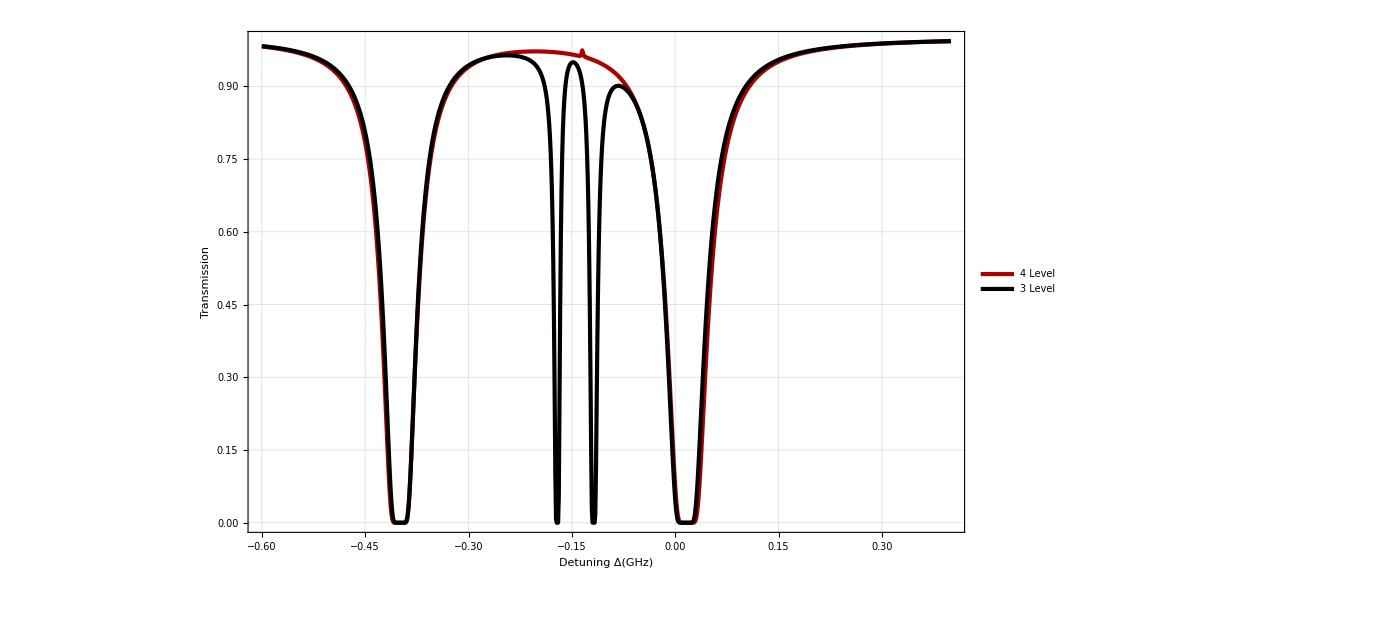

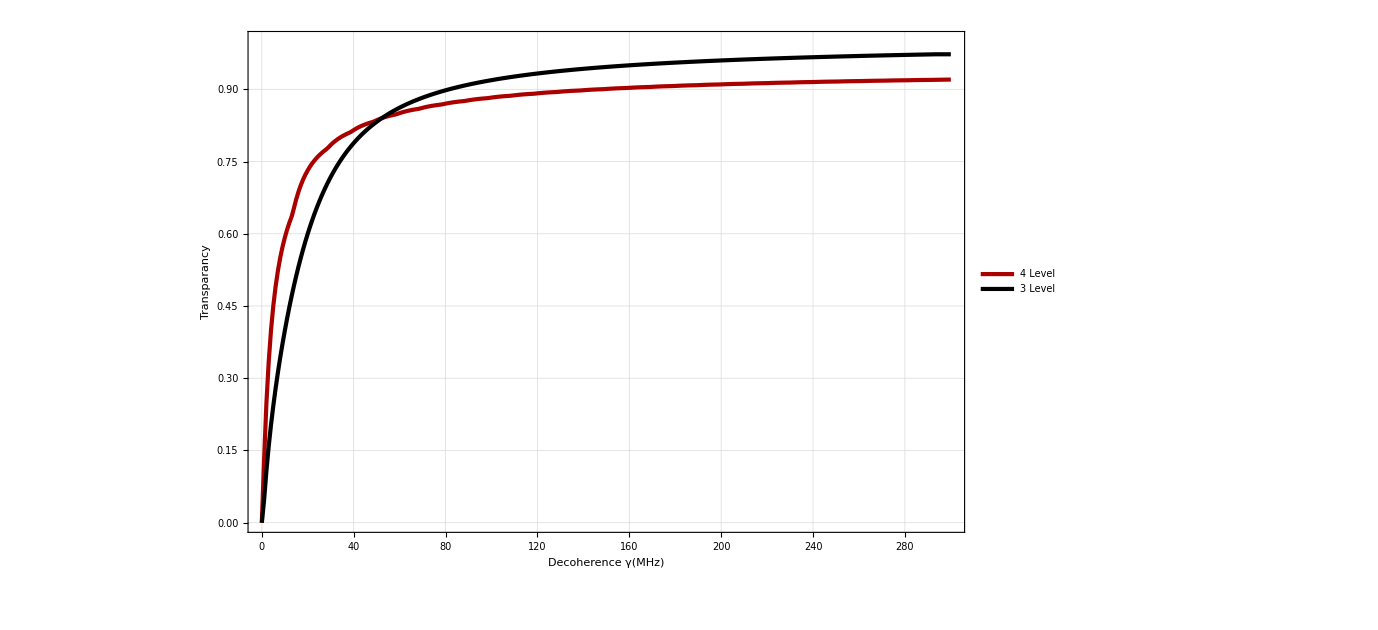

```mathematica
p=200;
δ=-156;
ListPlot[{Lev4DoppTestsc[50,p/1000,1/1000,0.5*10^6,δ*10^6,0],Lev3DoppTestsc[50,p/1000,1/1000,0.5*10^6,δ*10^6,0]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[30],Frame->True,Axes->False,PlotLegends->Placed[LineLegend[{"4 Level","3 Level"},LegendFunction->"Frame",LabelStyle->{FontSize->35}],{Right,Center}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[1],Darker[Red]},{AbsoluteThickness[1],Darker[Black]},{AbsoluteThickness[1],Red},{AbsoluteThickness[1],Black,Dashed}},FrameLabel->{Style["Detuning Δ(GHz)",20,Black],Style["Transmission ",20,Black]},GridLines->Automatic,PlotRange->All]
ListPlot[{Lev3Testsc[50,p/1000,1/1000,0.5*10^6,δ*10^6,1][[1]],Lev3Testsc[50,p/1000,1/1000,0.5*10^6,δ*10^6,1][[2]]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[30],Frame->True,Axes->False,PlotLegends->Placed[LineLegend[{"4 Level","3 Level"},LegendFunction->"Frame",LabelStyle->{FontSize->35}],{Right,Center}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[1],Darker[Red]},{AbsoluteThickness[1],Darker[Black]},{AbsoluteThickness[1],Red},{AbsoluteThickness[1],Black,Dashed}},FrameLabel->{Style["Detuning Δ(GHz)",20,Black],Style["Transmission ",20,Black]},GridLines->Automatic,PlotRange->All]
ListPlot[{Lev4Testsc[50,p/1000,1/1000,0.5*10^6,δ*10^6,0],Lev3Testsc[50,p/1000,1/1000,0.5*10^6,δ*10^6,0]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[30],Frame->True,Axes->False,PlotLegends->Placed[LineLegend[{"4 Level","3 Level"},LegendFunction->"Frame",LabelStyle->{FontSize->35}],{Right,Center}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Darker[Black]},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Detuning Δ(GHz)",20,Black],Style["Transmission ",20,Black]},GridLines->Automatic,PlotRange->All]
```

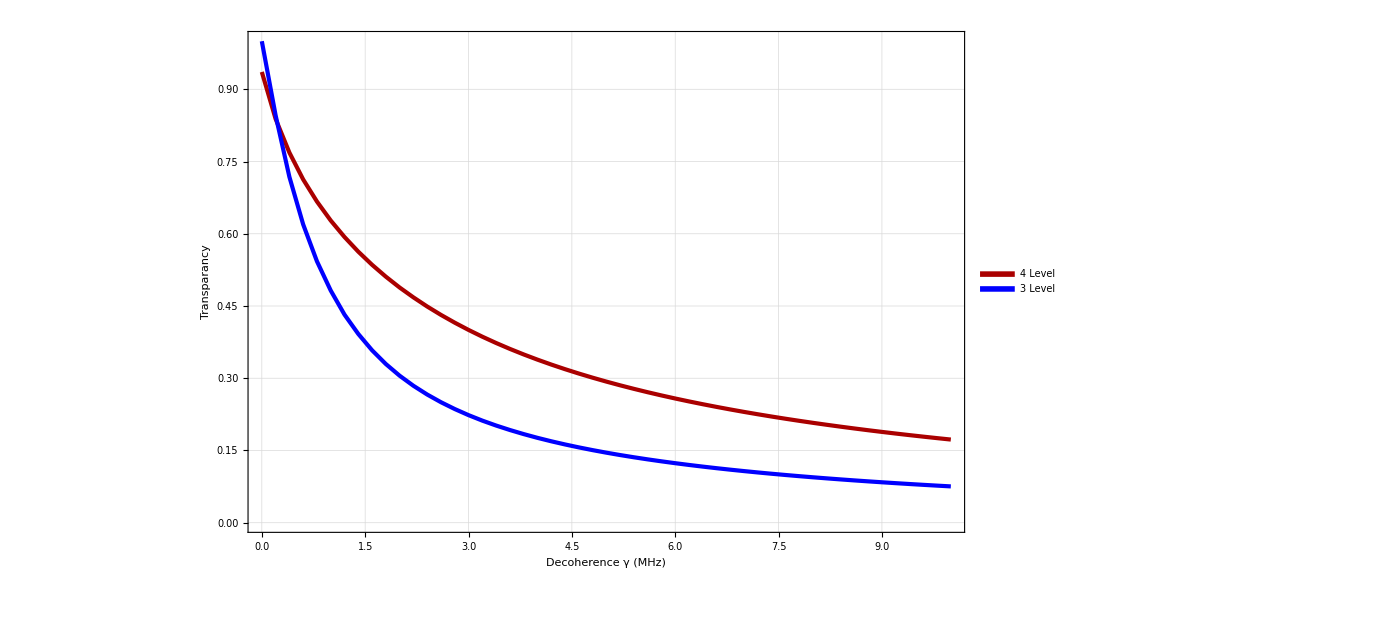

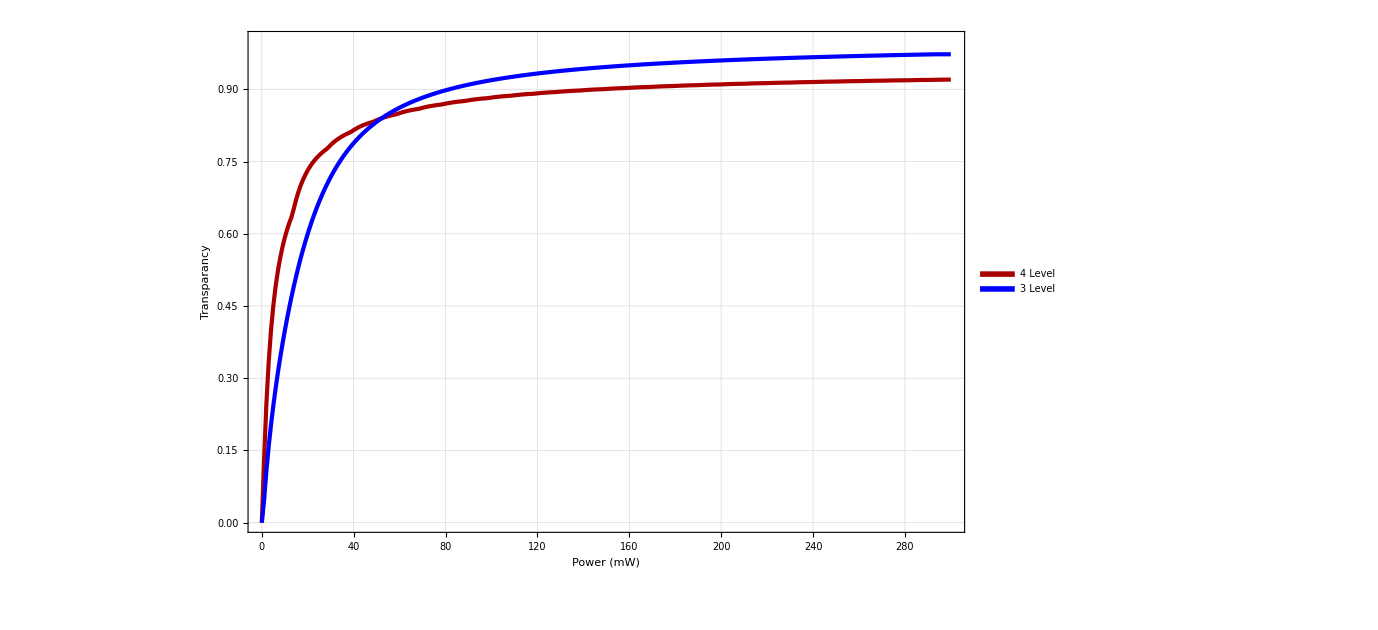

```mathematica
legend=LineLegend[Thread[Directive[{Darker[Red],Blue,{Darker[Gray],Dashed}},AbsoluteThickness[10]]],{Style["4 Level",Darker[Red]],Style["3 Level",Blue]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->45}];
pp1=ListPlot[{γvT4[20],γvT3[20]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,Center}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Decoherence γ (MHz)",50,Black],Style["Transparancy",50,Black]},GridLines->Automatic,PlotRange->{{0,10},{0,1}}]
pp2=ListPlot[{PvT4[0.5],PvT3[0.5]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,Center}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Power (mW)",50,Black],Style["Transparancy",50,Black]},GridLines->Automatic,PlotRange->{{0,300},{0,1}}]
```

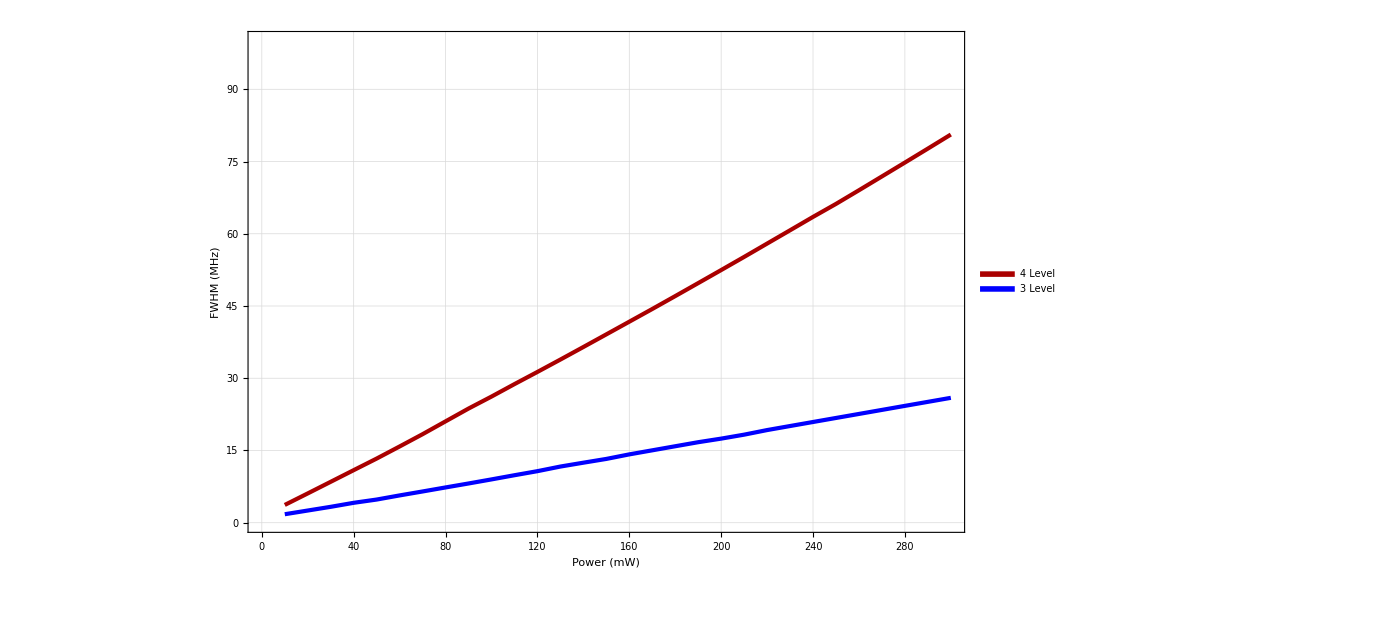

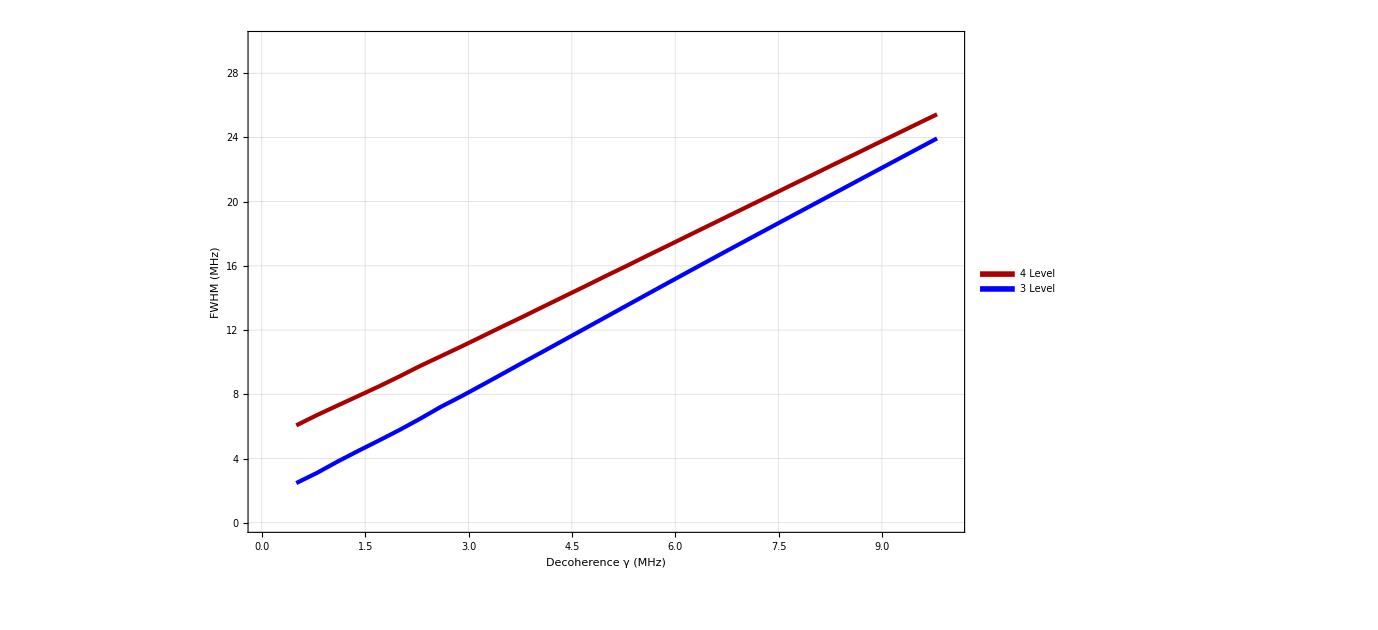

```mathematica
legend=LineLegend[Thread[Directive[{Darker[Red],Blue,{Darker[Gray],Dashed}},AbsoluteThickness[10]]],{Style["4 Level",Darker[Red]],Style["3 Level",Blue]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->45}];
pp1=ListPlot[{g3,f3},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,0.4}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Power (mW)",50,Black],Style["FWHM (MHz) ",50,Black]},GridLines->Automatic,PlotRange->{{0,300},{0,100}}]
pp2=ListPlot[{g,f},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,0.4}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Decoherence γ (MHz)",50,Black],Style["FWHM (MHz) ",50,Black]},GridLines->Automatic,PlotRange->{{0,10},{0,30}}]
```

```mathematica
SetDirectory["E:\\QOLab\\PersonalFolders\\Saesun\\Poster"]
```

E:\QOLab\PersonalFolders\Saesun\Poster

```mathematica
Export["h7117.jpg",pp1,ImageSize->3000]
Export["h8118.jpg",pp2,ImageSize->3000]
```

h7117.jpg

h8118.jpg

```mathematica
SetDirectory["C:\\Users\\Admin\\Qsync\\PersonalFolders\\Saesun\\Poster"]
Export["h56.jpg",pp1,ImageSize->3000]
Export["h57.jpg",pp2,ImageSize->3000]
```

C:\Users\Admin\Qsync\PersonalFolders\Saesun\Poster

h56.jpg

h57.jpg

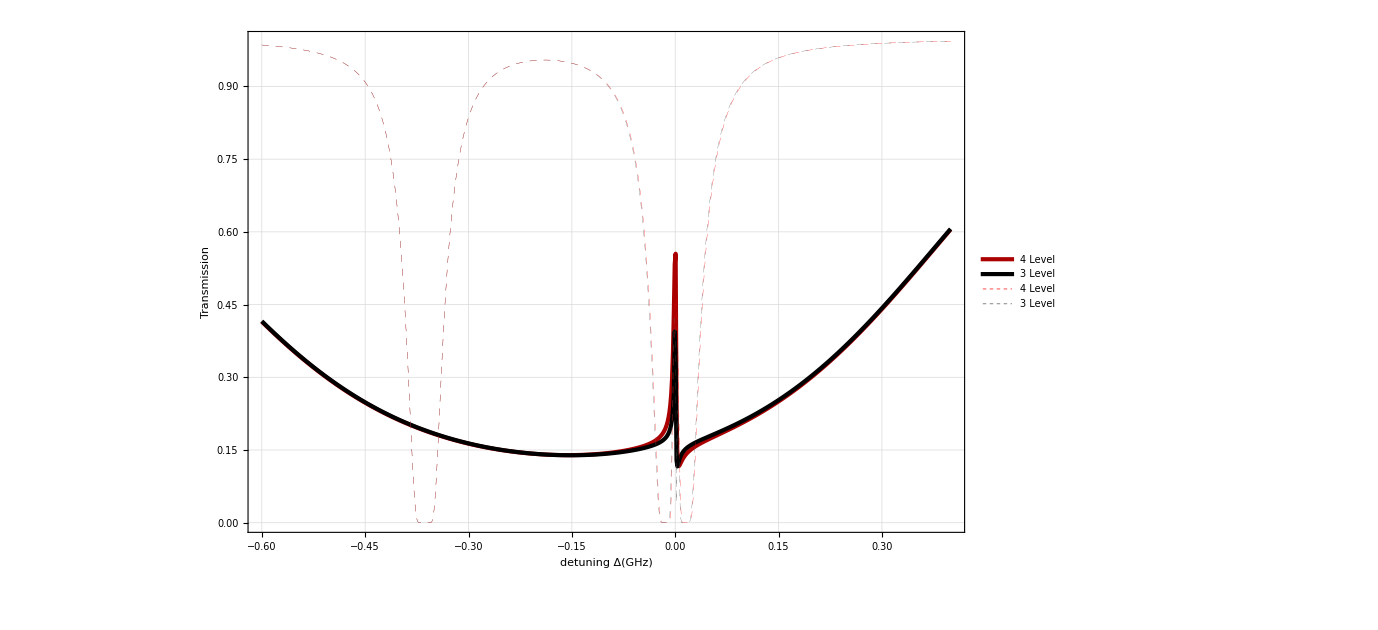

hello15.jpg

```mathematica
p=15;
δ=0;
ListPlot[{Lev4DoppTestsc[50,p/1000,1/1000,0.5*10^6,δ*10^6,0],Lev3DoppTestsc[50,p/1000,1/1000,0.5*10^6,δ*10^6,0],Lev4Testsc[50,p/1000,1/1000,0.5*10^6,δ*10^6,0],Lev3Testsc[50,p/1000,1/1000,0.5*10^6,δ*10^6,0]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[20],Frame->True,Axes->False,PlotLegends->Placed[LineLegend[{"4 Level","3 Level","4 Level","3 Level"},LegendFunction->"Frame",LabelStyle->{FontSize->25}],{Right,Center}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Darker[Black]},{AbsoluteThickness[0.2],Red,Dashed},{AbsoluteThickness[0.2],Lighter[Black],Dashed}},FrameLabel->{Style["detuning Δ(GHz)",20,Black],Style["Transmission ",20,Black]},GridLines->Automatic]
Export["hello15.jpg",%]
```

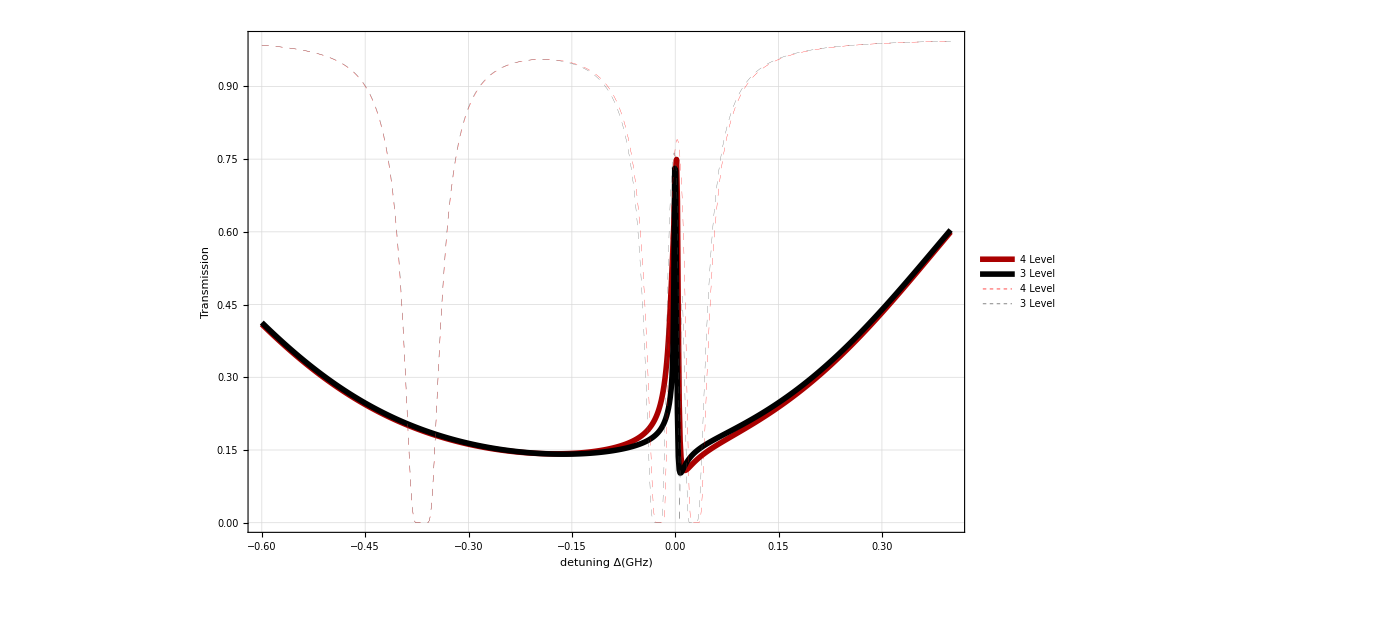

hello50.jpg

```mathematica
p=50;
δ=0;
ListPlot[{Lev4DoppTestsc[50,p/1000,1/1000,0.5*10^6,δ*10^6,0],Lev3DoppTestsc[50,p/1000,1/1000,0.5*10^6,δ*10^6,0],Lev4Testsc[50,p/1000,1/1000,0.5*10^6,δ*10^6,0],Lev3Testsc[50,p/1000,1/1000,0.5*10^6,δ*10^6,0]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[20],Frame->True,Axes->False,PlotLegends->Placed[LineLegend[{"4 Level","3 Level","4 Level","3 Level"},LegendFunction->"Frame",LabelStyle->{FontSize->25}],{Right,Center}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[4],Darker[Red]},{AbsoluteThickness[4],Darker[Black]},{AbsoluteThickness[0.2],Red,Dashed},{AbsoluteThickness[0.2],Lighter[Black],Dashed}},FrameLabel->{Style["detuning Δ(GHz)",20,Black],Style["Transmission ",20,Black]},GridLines->Automatic]
Export["hello50.jpg",%]
```

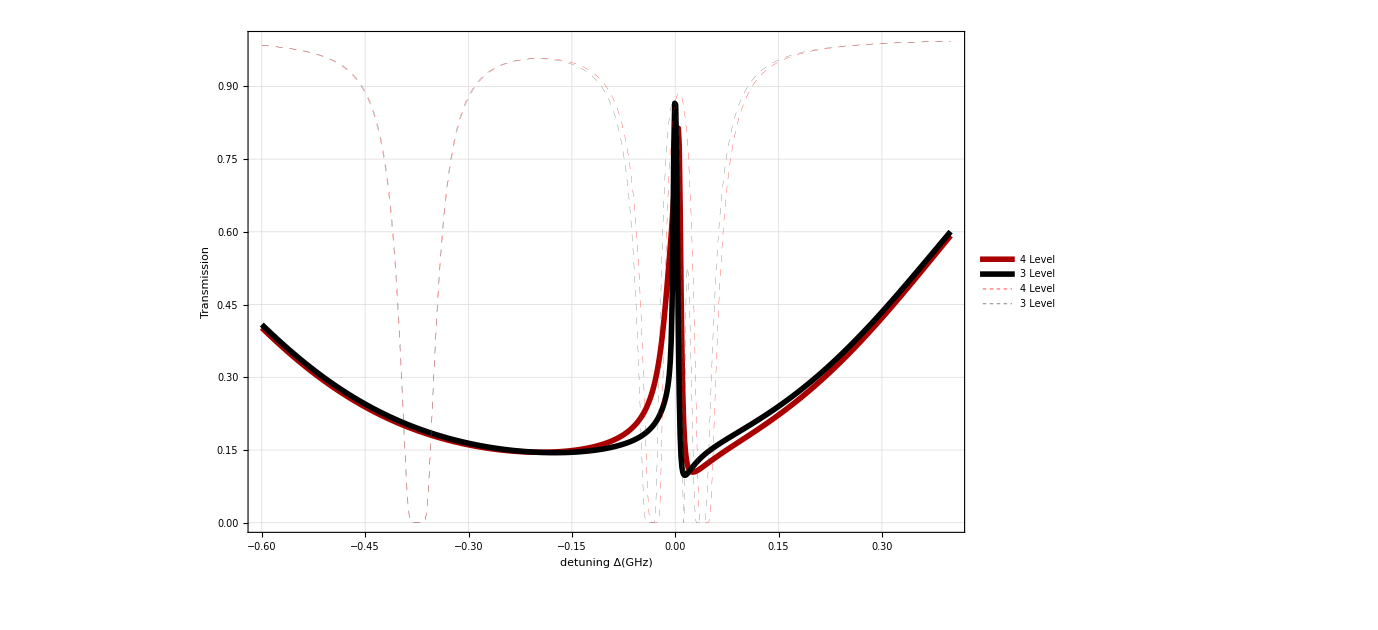

hello100.jpg

```mathematica
p=100;
δ=0;
ListPlot[{Lev4DoppTestsc[50,p/1000,1/1000,0.5*10^6,δ*10^6,0],Lev3DoppTestsc[50,p/1000,1/1000,0.5*10^6,δ*10^6,0],Lev4Testsc[50,p/1000,1/1000,0.5*10^6,δ*10^6,0],Lev3Testsc[50,p/1000,1/1000,0.5*10^6,δ*10^6,0]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[20],Frame->True,Axes->False,PlotLegends->Placed[LineLegend[{"4 Level","3 Level","4 Level","3 Level"},LegendFunction->"Frame",LabelStyle->{FontSize->25}],{Right,Center}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[4],Darker[Red]},{AbsoluteThickness[4],Darker[Black]},{AbsoluteThickness[0.2],Red,Dashed},{AbsoluteThickness[0.2],Lighter[Black],Dashed}},FrameLabel->{Style["detuning Δ(GHz)",20,Black],Style["Transmission ",20,Black]},GridLines->Automatic]
Export["hello100.jpg",%]
```

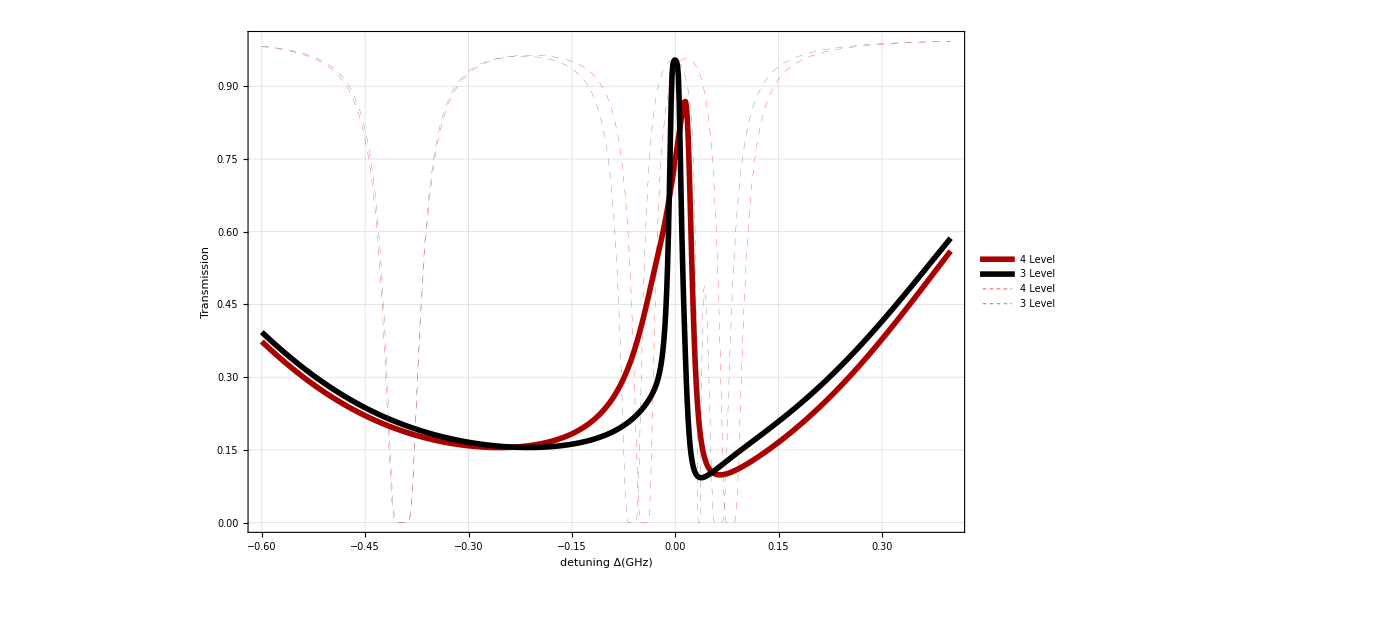

hello300.jpg

```mathematica
p=300;
δ=0;
ListPlot[{Lev4DoppTestsc[50,p/1000,1/1000,0.5*10^6,δ*10^6,0],Lev3DoppTestsc[50,p/1000,1/1000,0.5*10^6,δ*10^6,0],Lev4Testsc[50,p/1000,1/1000,0.5*10^6,δ*10^6,0],Lev3Testsc[50,p/1000,1/1000,0.5*10^6,δ*10^6,0]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[20],Frame->True,Axes->False,PlotLegends->Placed[LineLegend[{"4 Level","3 Level","4 Level","3 Level"},LegendFunction->"Frame",LabelStyle->{FontSize->25}],{Right,Center}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[4],Darker[Red]},{AbsoluteThickness[4],Darker[Black]},{AbsoluteThickness[0.2],Red,Dashed},{AbsoluteThickness[0.2],Lighter[Black],Dashed}},FrameLabel->{Style["detuning Δ(GHz)",20,Black],Style["Transmission ",20,Black]},GridLines->Automatic]
Export["hello300.jpg",%]
```

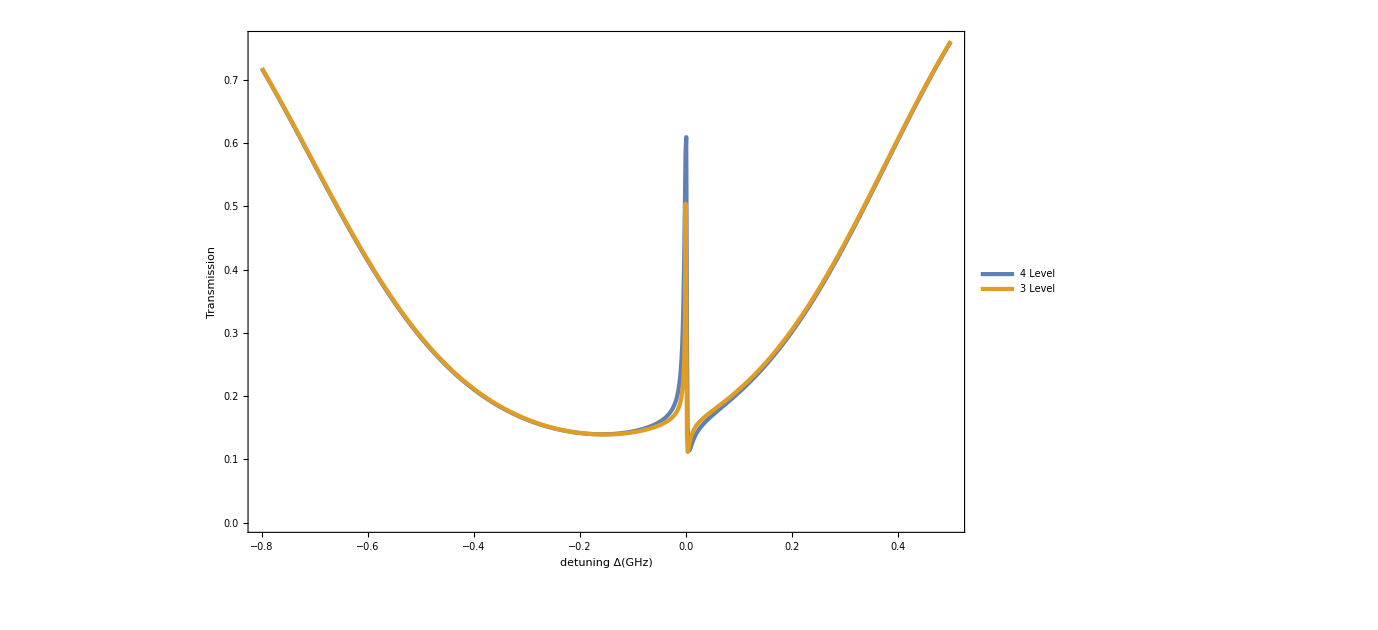

```mathematica
ListPlot[{Lev4DoppTestsc[50,20/1000,1/1000,0.5*10^6,0*10^6,0],Lev3DoppTestsc[50,20/1000,1/1000,0.5*10^6,0*10^6,0]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[20],Frame->True,Axes->False,PlotLegends->Placed[LineLegend[{"4 Level","3 Level"},LegendFunction->"Frame",LabelStyle->{FontSize->25}],{Right,Center}],ImageSize->1020,PlotStyle-> {AbsoluteThickness[3],AbsoluteThickness[3]},FrameLabel->{Style["detuning Δ(GHz)",20,Black],Style["Transmission ",20,Black]}]
```

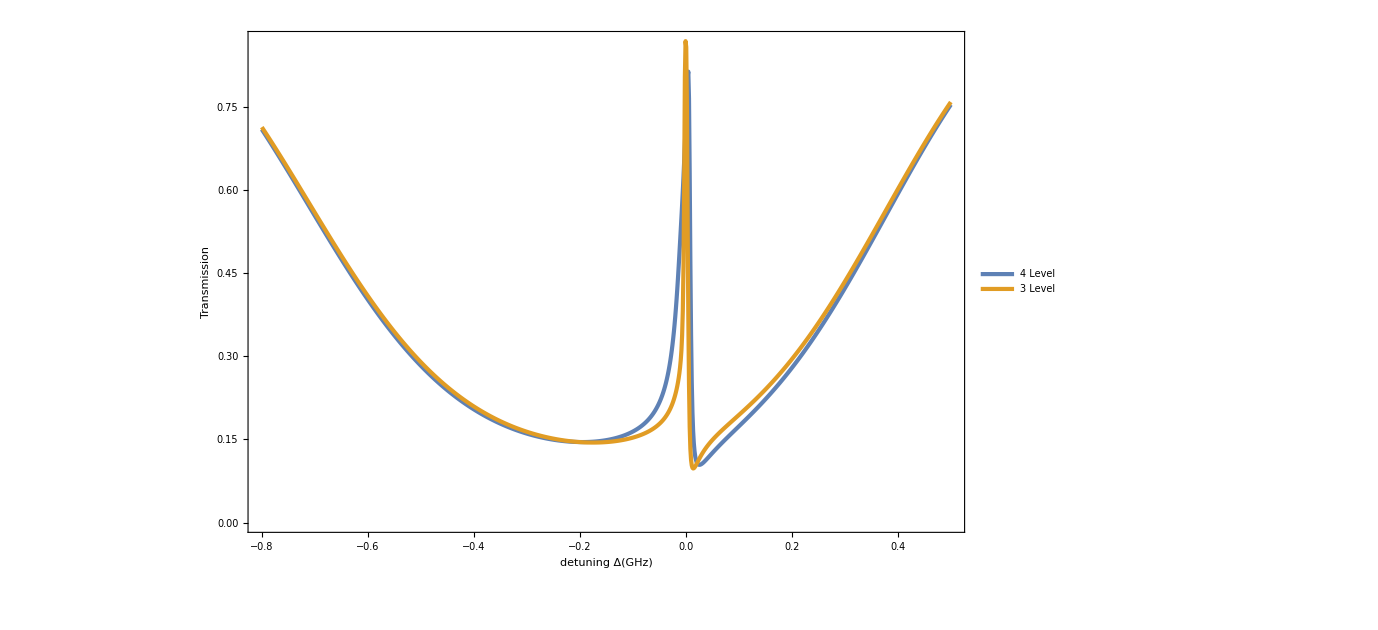

```mathematica
ListPlot[{Lev4DoppTestsc[50,100/1000,1/1000,0.5*10^6,0*10^6,0],Lev3DoppTestsc[50,100/1000,1/1000,0.5*10^6,0*10^6,0]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[20],Frame->True,Axes->False,PlotLegends->Placed[LineLegend[{"4 Level","3 Level"},LegendFunction->"Frame",LabelStyle->{FontSize->25}],{Right,Center}],ImageSize->1020,PlotStyle-> {AbsoluteThickness[3],AbsoluteThickness[3]},FrameLabel->{Style["detuning Δ(GHz)",20,Black],Style["Transmission ",20,Black]}]
```

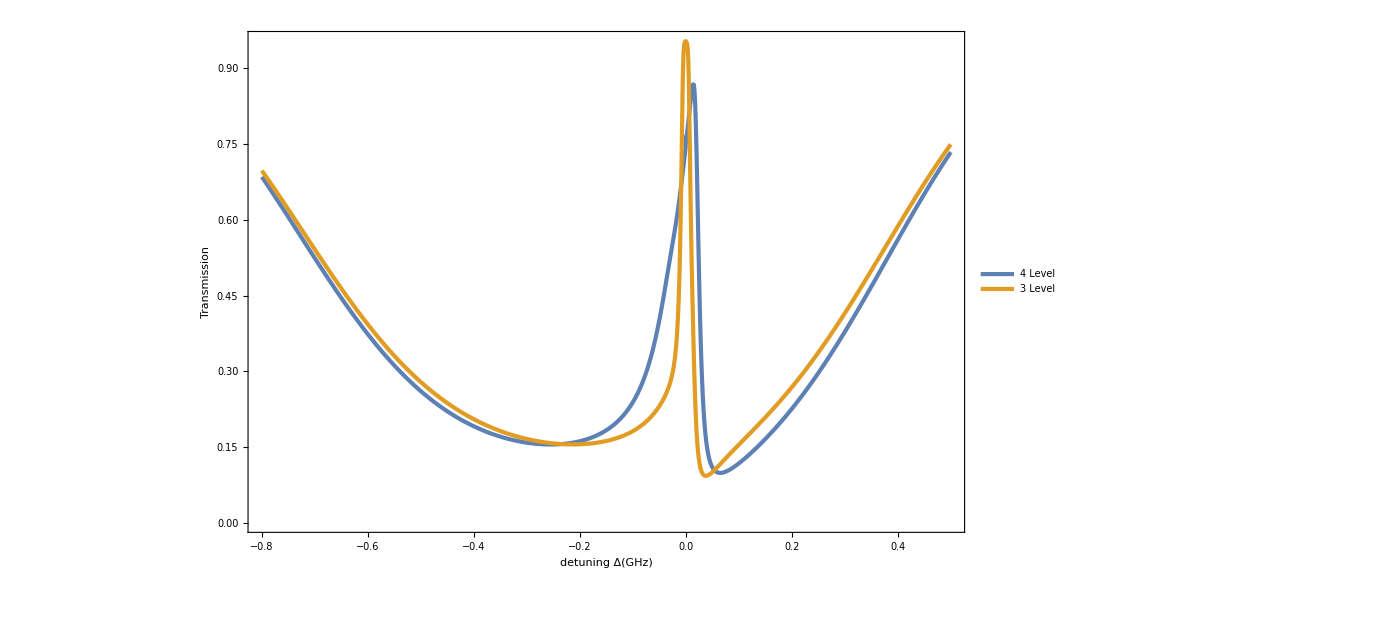

```mathematica
ListPlot[{Lev4DoppTestsc[50,300/1000,1/1000,0.5*10^6,0*10^6,0],Lev3DoppTestsc[50,300/1000,1/1000,0.5*10^6,0*10^6,0]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[20],Frame->True,Axes->False,PlotLegends->Placed[LineLegend[{"4 Level","3 Level"},LegendFunction->"Frame",LabelStyle->{FontSize->25}],{Right,Center}],ImageSize->1020,PlotStyle-> {AbsoluteThickness[3],AbsoluteThickness[3]},FrameLabel->{Style["detuning Δ(GHz)",20,Black],Style["Transmission ",20,Black]}]
```

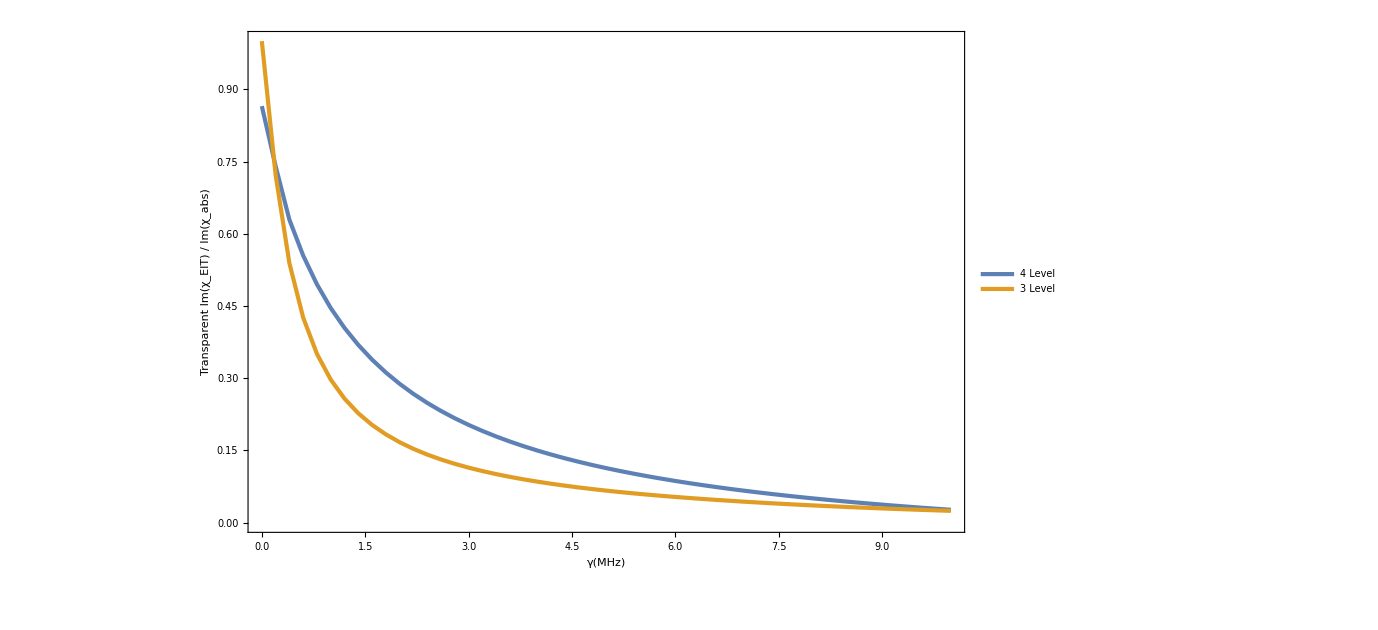

```mathematica
ListPlot[{γvT4[10],γvT3[10]},Joined->True,Frame->True,Axes->False,PlotRange->All,PlotLegends->Placed[LineLegend[{"4 Level","3 Level"},LegendFunction->"Frame",LabelStyle->{FontSize->25}],{Right,Center}],ImageSize->1020,PlotStyle-> {AbsoluteThickness[3],AbsoluteThickness[3]},FrameLabel->{Style["γ(MHz)",13,Black],Style["Transparent Im(χ_EIT) / Im(χ_abs)",13,Black]}]
```

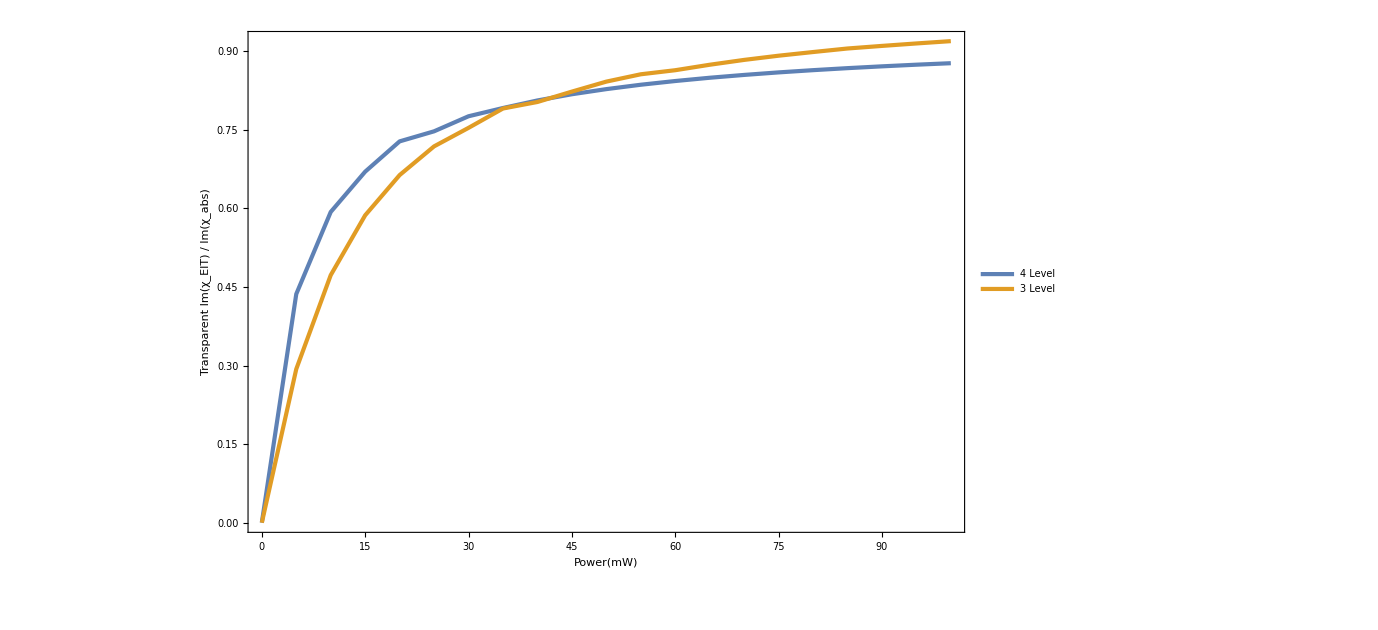

```mathematica
ListPlot[{PvT4[0.5],PvT3[0.5]},Joined->True,Frame->True,Axes->False,PlotRange->All,PlotLegends->Placed[LineLegend[{"4 Level","3 Level"},LegendFunction->"Frame",LabelStyle->{FontSize->25}],{Right,Center}],ImageSize->1020,PlotStyle-> {AbsoluteThickness[3],AbsoluteThickness[3]},FrameLabel->{Style["Power(mW)",13,Black],Style["Transparent Im(χ_EIT) / Im(χ_abs)",13,Black]}]
```

# Contour Plot of Transmission Δ vs δ

## P=50

```mathematica
p=50;
Off[General::ovfl];Off[General::unfl];
kkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTest[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,-0.01,0.01,0.001}]],3];
kkk6=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4Test[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,-0.01,0.01,0.001}]],3];
kkk7=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3DoppTest[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,-0.01,0.01,0.001}]],3];
kkk8=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3Test[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,-0.01,0.01,0.001}]],3];
```

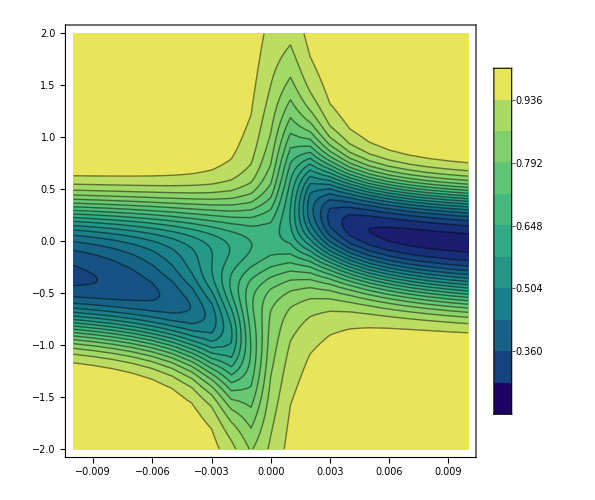
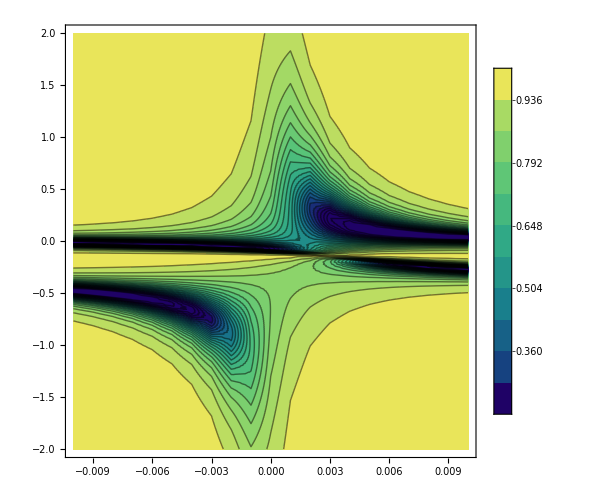
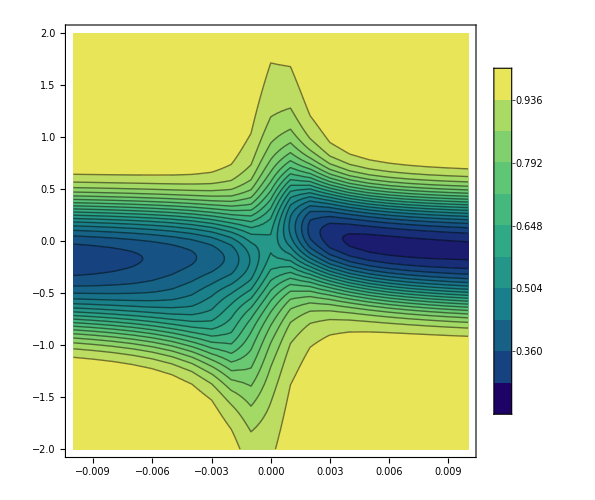
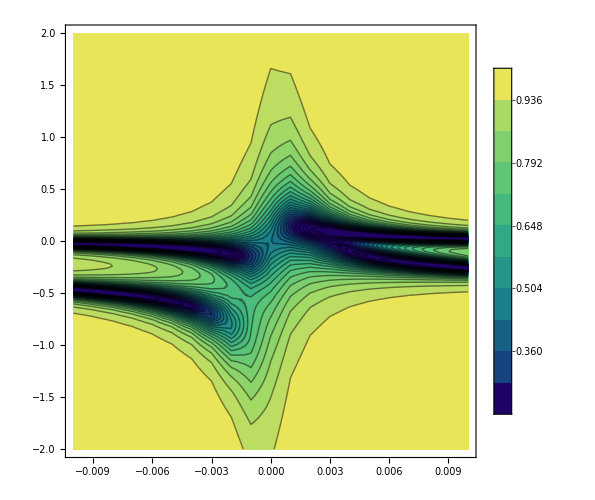
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
{{ListContourPlot[kkk5,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotLegends-> BarLegend[{Automatic,{0.2,1}},10]],
ListContourPlot[kkk6,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotLegends-> BarLegend[{Automatic,{0.2,1}},10]]},
{ListContourPlot[kkk7,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotLegends-> BarLegend[{Automatic,{0.2,1}},10]],
ListContourPlot[kkk8,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotLegends-> BarLegend[{Automatic,{0.2,1}},10]]}}//TableForm
```

```mathematica
kkk7=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTest[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,0][[2]]}],{delt,-0.1,0.1,0.002}]],3];
```

Transpose::nmtx: The first two levels of {{-2.,-1.98,-1.96,-1.94,-1.92,-1.9,-1.88,-1.86,-1.84,-1.82,-1.8,-1.78,-1.76,-1.74,-1.72,-1.7,-1.68,-1.66,-1.64,-1.62,-1.6,-1.58,-1.56,-1.54,-1.52,-1.5,-1.48,-1.46,-1.44,-1.42,-1.4,-1.38,-1.36,-1.34,-1.32,-1.3,-1.28,-1.26,-1.24,-1.22,-1.2,-1.18,-1.16,-1.14,-1.12,-1.1,-1.08,-1.06,-1.04,-1.02,«151»},Im[sd24[2.36944×10^15,7.06858×10^6,«10»,2.27189×10^9,9.76768×10^-30]]} cannot be transposed.

Transpose::nmtx: The first two levels of {{-2.,-1.98,-1.96,-1.94,-1.92,-1.9,-1.88,-1.86,-1.84,-1.82,-1.8,-1.78,-1.76,-1.74,-1.72,-1.7,-1.68,-1.66,-1.64,-1.62,-1.6,-1.58,-1.56,-1.54,-1.52,-1.5,-1.48,-1.46,-1.44,-1.42,-1.4,-1.38,-1.36,-1.34,-1.32,-1.3,-1.28,-1.26,-1.24,-1.22,-1.2,-1.18,-1.16,-1.14,-1.12,-1.1,-1.08,-1.06,-1.04,-1.02,«151»},Im[sd23[2.36944×10^15,7.06858×10^6,«10»,2.27189×10^9,1.09206×10^-29]]} cannot be transposed.

Transpose::nmtx: The first two levels of {{-2.,-1.98,-1.96,-1.94,-1.92,-1.9,-1.88,-1.86,-1.84,-1.82,-1.8,-1.78,-1.76,-1.74,-1.72,-1.7,-1.68,-1.66,-1.64,-1.62,-1.6,-1.58,-1.56,-1.54,-1.52,-1.5,-1.48,-1.46,-1.44,-1.42,-1.4,-1.38,-1.36,-1.34,-1.32,-1.3,-1.28,-1.26,-1.24,-1.22,-1.2,-1.18,-1.16,-1.14,-1.12,-1.1,-1.08,-1.06,-1.04,-1.02,«151»},Im[sd24[2.36944×10^15,7.06858×10^6,«10»,2.27189×10^9,9.76768×10^-30]]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

$Aborted

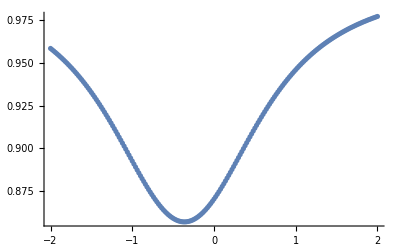

```mathematica
ListPlot[Lev3DoppTest[45,20/1000,1.4/1000,0.5*10^6,0*10^9,0][[2]]]
```

```mathematica
ListContourPlot[kkk7,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotLegends-> BarLegend[{Automatic,{0.2,1}},10]]
```

-Graphics-

```mathematica
ListContourPlot[kkk7,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotLegends-> BarLegend[{Automatic,{0.2,1}},10]]
```

-Graphics-

## P=10

```mathematica
p=10;
Off[General::ovfl];Off[General::unfl];
kkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTest[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,-0.01,0.01,0.001}]],3];
kkk6=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4Test[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,-0.01,0.01,0.001}]],3];
kkk7=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3DoppTest[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,-0.01,0.01,0.001}]],3];
kkk8=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3Test[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,-0.01,0.01,0.001}]],3];
```

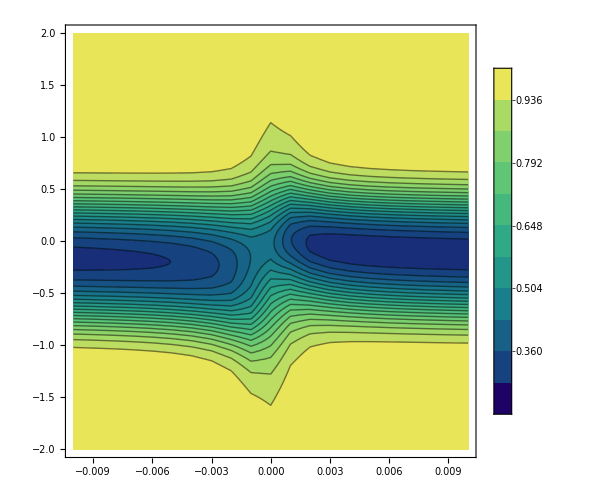
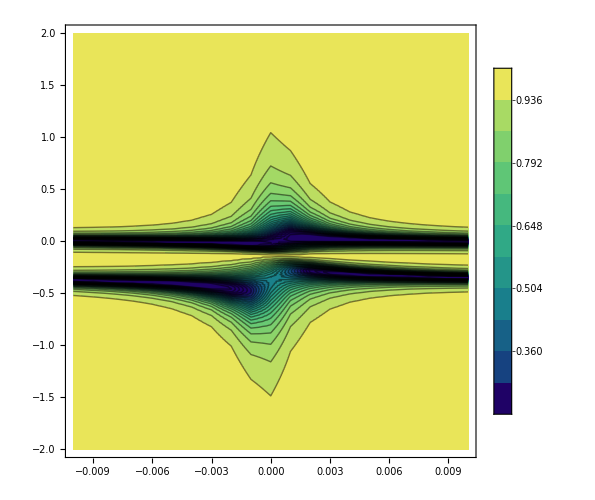
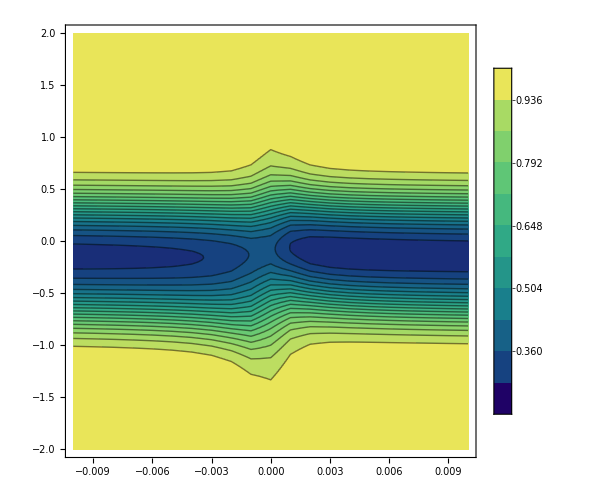
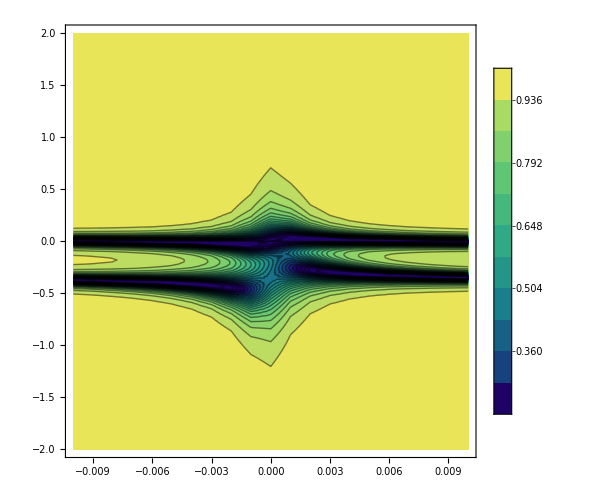
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
{{ListContourPlot[kkk5,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotLegends-> BarLegend[{Automatic,{0.2,1}},10]],
ListContourPlot[kkk6,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotLegends-> BarLegend[{Automatic,{0.2,1}},10]]},
{ListContourPlot[kkk7,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotLegends-> BarLegend[{Automatic,{0.2,1}},10]],
ListContourPlot[kkk8,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotLegends-> BarLegend[{Automatic,{0.2,1}},10]]}}//TableForm
```

## P=1

```mathematica
p=1;
Off[General::ovfl];Off[General::unfl];
kkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTest[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,-0.01,0.01,0.001}]],3];
kkk6=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4Test[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,-0.01,0.01,0.001}]],3];
kkk7=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3DoppTest[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,-0.01,0.01,0.001}]],3];
kkk8=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3Test[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,-0.01,0.01,0.001}]],3];
```

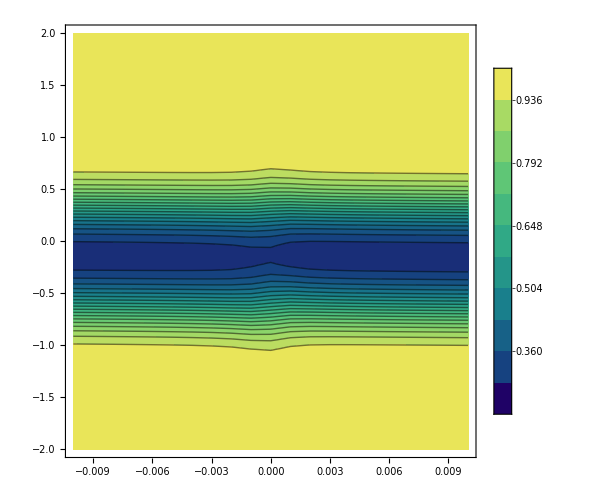
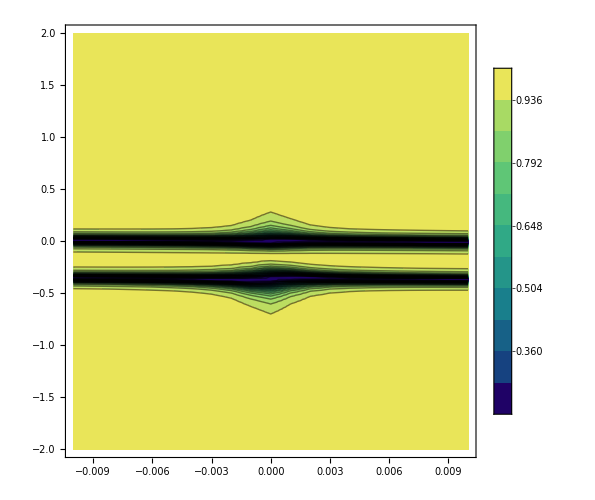
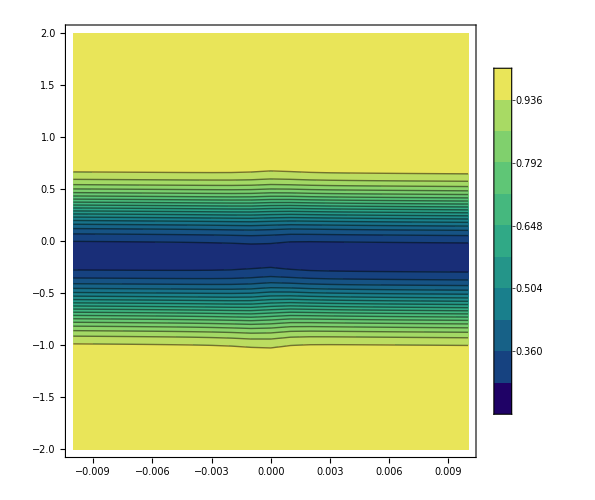
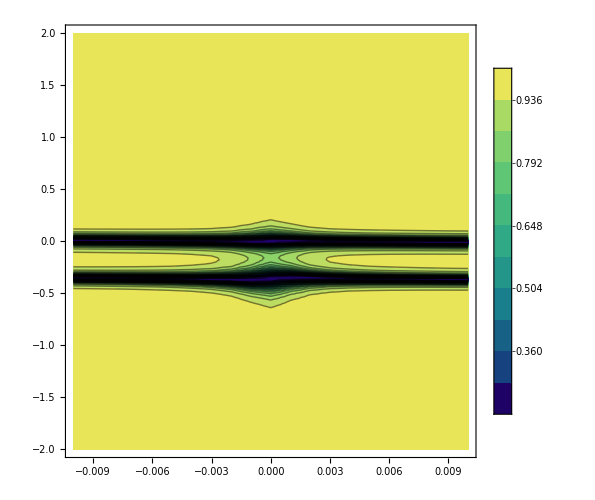
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
{{ListContourPlot[kkk5,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotLegends-> BarLegend[{Automatic,{0.2,1}},10]],
ListContourPlot[kkk6,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotLegends-> BarLegend[{Automatic,{0.2,1}},10]]},
{ListContourPlot[kkk7,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotLegends-> BarLegend[{Automatic,{0.2,1}},10]],
ListContourPlot[kkk8,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotLegends-> BarLegend[{Automatic,{0.2,1}},10]]}}//TableForm
```

## P=0

```mathematica
p=0;
Off[General::ovfl];Off[General::unfl];
kkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTest[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,-0.01,0.01,0.001}]],3];
kkk6=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4Test[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,-0.01,0.01,0.001}]],3];
kkk7=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3DoppTest[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,-0.01,0.01,0.001}]],3];
kkk8=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3Test[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,-0.01,0.01,0.001}]],3];
```

```mathematica
{{ListContourPlot[kkk5,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotLegends-> BarLegend[{Automatic,{0.2,1}},10]],
ListContourPlot[kkk6,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotLegends-> BarLegend[{Automatic,{0.2,1}},10]]},
{ListContourPlot[kkk7,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotLegends-> BarLegend[{Automatic,{0.2,1}},10]],
ListContourPlot[kkk8,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotLegends-> BarLegend[{Automatic,{0.2,1}},10]]}}//TableForm
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-

## Cross section

P=50

```mathematica
p=50;
kkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTest[45,p/1000,1.4/1000,0*10^6,delt*10^9,1]}],{delt,-0.2,0.2,0.005}]],3];
kkkk7=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3DoppTest[45,p/1000,1.4/1000,0*10^6,delt*10^9,1]}],{delt,-0.2,0.2,0.005}]],3];
resk5=Interpolation[kkkk5];
Kiak5=ListContourPlot[kkkk5,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
resk7=Interpolation[kkkk7];
Kiak7=ListContourPlot[kkkk7,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
```

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/(0.+0. ⅈ)^2 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

```mathematica
kkkk6=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4Test[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,-0.2,0.2,0.005}]],3];
kkkk8=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3Test[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,-0.2,0.2,0.005}]],3];
resk6=Interpolation[kkkk6];
Kiak6=ListContourPlot[kkkk6,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
resk8=Interpolation[kkkk8];
Kiak8=ListContourPlot[kkkk8,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
```

```mathematica
Manipulate[
GraphicsRow[{Show[Kiak6,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300],
Show[Kiak8,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300]
,Plot[{resk6[t,b],resk8[t,b]},{t,-0.2,0.2},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-1,0.5}]
```

Show::gcomb: Could not combine the graphics objects in Show[Kiak6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak8,,ImageSize→300].

```mathematica
Manipulate[
GraphicsRow[{Show[Kiak6,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300],
Show[Kiak8,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300]
,Plot[{resk6[t,b],resk8[t,b]},{t,-0.2,0.2},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-1,0.5}]
```

Show::gcomb: Could not combine the graphics objects in Show[Kiak6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak8,,ImageSize→300].

```mathematica
Manipulate[
GraphicsRow[{Show[Kiak5,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300],
Show[Kiak7,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300]
,Plot[{resk5[b,t],resk7[b,t]},{t,-2,2},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-0.2,0.2}]
```

Show::gcomb: Could not combine the graphics objects in Show[Kiak5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak7,,ImageSize→300].

```mathematica
Manipulate[
GraphicsRow[{Show[Kiak5,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300],
Show[Kiak7,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300]
,Plot[{resk5[t,b],resk7[t,b]},{t,-0.2,0.2},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-1,0.5}]
```

Show::gcomb: Could not combine the graphics objects in Show[Kiak5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiak7,,ImageSize→300].

```mathematica
p=50;
kkl5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTest[45,p/1000,1.4/1000,0*10^6,delt*10^9,1]}],{delt,-0.01,0.01,0.001}]],3];
kkl7=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3DoppTest[45,p/1000,1.4/1000,0*10^6,delt*10^9,1]}],{delt,-0.01,0.01,0.001}]],3];
rel5=Interpolation[kkl5];
Kil5=ListContourPlot[kkl5,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
rel7=Interpolation[kkl7];
Kil7=ListContourPlot[kkl7,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
kkl6=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4Test[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,-0.01,0.01,0.001}]],3];
kkl8=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3Test[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,-0.01,0.01,0.001}]],3];
rel6=Interpolation[kkl6];
Kil6=ListContourPlot[kkl6,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
rel8=Interpolation[kkl8];
Kil8=ListContourPlot[kkl8,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
```

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/(0.+0. ⅈ)^2 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

```mathematica
p=100
kkl6=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4Test[45,p/1000,1.4/1000,0*10^6,delt*10^9,1]}],{delt,-0.01,0.01,0.0001}]],3];
kkl8=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3Test[45,p/1000,1.4/1000,0*10^6,delt*10^9,1]}],{delt,-0.01,0.01,0.0001}]],3];
rel6=Interpolation[kkl6];
Kil6=ListContourPlot[kkl6,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
rel8=Interpolation[kkl8];
Kil8=ListContourPlot[kkl8,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
```

100

```mathematica
Manipulate[
GraphicsRow[{Show[Kil6,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300],
Show[Kil8,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300]
,Plot[{rel6[b,t],rel8[b,t]},{t,-2,2},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-0.01,0.01}]
```

Show::gcomb: Could not combine the graphics objects in Show[Kil6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil8,,ImageSize→300].

```mathematica
Manipulate[
GraphicsRow[{Show[Kil6,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300],
Show[Kil8,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300]
,Plot[{rel6[t,b],rel8[t,b]},{t,-0.01,0.01},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-1,0.5}]
```

Show::gcomb: Could not combine the graphics objects in Show[Kil6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil8,,ImageSize→300].

```mathematica
Manipulate[
GraphicsRow[{Show[Kil5,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300],
Show[Kil7,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300]
,Plot[{rel5[t,b],rel7[t,b]},{t,-0.01,0.01},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-1,0.5}]
```

Show::gcomb: Could not combine the graphics objects in Show[Kil5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil7,,ImageSize→300].

```mathematica
Manipulate[
GraphicsRow[{Show[Kil5,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300],
Show[Kil7,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300]
,Plot[{rel5[b,t],rel7[b,t]},{t,-2,2},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-0.01,0.01}]
```

Show::gcomb: Could not combine the graphics objects in Show[Kil5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kil7,,ImageSize→300].

P=100

```mathematica
{delt,Flatten[{Range[-0.01,-0.02,0.01],Range[-0.021,0.019,0.001],Range[0.02,0.01,0.01]}]}]],3];
```

```mathematica
p=100;
kkkkq5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTest[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,Flatten[{Range[-0.2,-0.02,0.01],Range[-0.021,0.019,0.001],Range[0.02,0.2,0.01]}]}]],3];
kkkkq7=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3DoppTest[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,Flatten[{Range[-0.2,-0.02,0.01],Range[-0.021,0.019,0.001],Range[0.02,0.2,0.01]}]}]],3];
reskq5=Interpolation[kkkkq5];
Kiakq5=ListContourPlot[kkkkq5,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
reskq7=Interpolation[kkkkq7];
Kiakq7=ListContourPlot[kkkkq7,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
```

```mathematica
kkkkq6=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4Test[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,Flatten[{Range[-0.2,-0.02,0.01],Range[-0.021,0.019,0.001],Range[0.02,0.2,0.01]}]}]],3];
kkkkq8=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3Test[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,Flatten[{Range[-0.2,-0.02,0.01],Range[-0.021,0.019,0.001],Range[0.02,0.2,0.01]}]}]],3];
reskq6=Interpolation[kkkkq6];
Kiakq6=ListContourPlot[kkkkq6,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
reskq8=Interpolation[kkkkq8];
Kiakq8=ListContourPlot[kkkkq8,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
```

```mathematica
Manipulate[
GraphicsRow[{Show[Kiakq6,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300],
Show[Kiakq8,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300]
,Plot[{reskq6[t,b],reskq8[t,b]},{t,-0.2,0.2},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-1,0.5}]
```

Show::gcomb: Could not combine the graphics objects in Show[Kiakq6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq8,,ImageSize→300].

```mathematica
Manipulate[
GraphicsRow[{Show[Kiakq6,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300],
Show[Kiakq8,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300]
,Plot[{reskq6[t,b],reskq8[t,b]},{t,-0.2,0.2},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-1,0.5}]
```

Show::gcomb: Could not combine the graphics objects in Show[Kiakq6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq8,,ImageSize→300].

```mathematica
Manipulate[
GraphicsRow[{Show[Kiakq5,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300],
Show[Kiakq7,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300]
,Plot[{reskq5[b,t],reskq7[b,t]},{t,-2,2},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-0.2,0.2}]
```

Show::gcomb: Could not combine the graphics objects in Show[Kiakq5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq7,,ImageSize→300].

```mathematica
Manipulate[
GraphicsRow[{Show[Kiakq5,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300],
Show[Kiakq7,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300]
,Plot[{reskq5[t,b],reskq7[t,b]},{t,-0.2,0.2},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-1,0.5}]
```

Show::gcomb: Could not combine the graphics objects in Show[Kiakq5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kiakq7,,ImageSize→300].

```mathematica
p=100;
kklq5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTest[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,-0.01,0.01,0.0005}]],3];
kklq7=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3DoppTest[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,-0.01,0.01,0.0005}]],3];
relq5=Interpolation[kklq5];
Kilq5=ListContourPlot[kklq5,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
relq7=Interpolation[kklq7];
Kilq7=ListContourPlot[kklq7,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
kklq6=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4Test[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,-0.01,0.01,0.0005}]],3];
kklq8=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3Test[45,p/1000,1.4/1000,1.125*10^6,delt*10^9,1]}],{delt,-0.01,0.01,0.0005}]],3];
relq6=Interpolation[kklq6];
Kilq6=ListContourPlot[kklq6,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
relq8=Interpolation[kklq8];
Kilq8=ListContourPlot[kklq8,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
```

```mathematica
Manipulate[
GraphicsRow[{Show[Kilq6,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300],
Show[Kilq8,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300]
,Plot[{relq6[b,t],relq8[b,t]},{t,-2,2},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-0.01,0.01}]
```

Show::gcomb: Could not combine the graphics objects in Show[Kilq6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq6,,ImageSize→300].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[Kilq6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq8,,ImageSize→300].

```mathematica
Manipulate[
GraphicsRow[{Show[Kilq6,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300],
Show[Kilq8,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300]
,Plot[{relq6[t,b],relq8[t,b]},{t,-0.01,0.01},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-1,0.5}]
```

Show::gcomb: Could not combine the graphics objects in Show[Kilq6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq8,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq6,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq8,,ImageSize→300].

```mathematica
Manipulate[
GraphicsRow[{Show[Kilq5,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300],
Show[Kilq7,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300]
,Plot[{relq5[t,b],relq7[t,b]},{t,-0.01,0.01},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-1,0.5}]
```

Show::gcomb: Could not combine the graphics objects in Show[Kilq5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq7,,ImageSize→300].

```mathematica
Manipulate[
GraphicsRow[{Show[Kilq5,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300],
Show[Kilq7,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300]
,Plot[{relq5[b,t],relq7[b,t]},{t,-2,2},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-0.01,0.01}]
```

Show::gcomb: Could not combine the graphics objects in Show[Kilq5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq7,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq5,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[Kilq7,,ImageSize→300].

# Experiment

## Frequency

```mathematica
xaxisD1[list_]:=Module[{points,npoints,λSF3,λSF3PF2,λSF3PF3,ans,i},
Do[points=Select[FindPeaks[list[[2]],l,0.0001,InterpolationOrder->1],#[[2]]≤2.7&];
If[Length[points]==3,Break[]];,{l,1,20,1}];
λSF3=0;λSF3PF2=λSF3;λSF3PF3=λSF3+0.360;
ans=Quiet@NSolve[{points[[1,1]]/m+a==-λSF3PF3,points[[3,1]]/m+a==-λSF3PF2},{m,a}][[1]];
Transpose[{Table[i,{i,1,Length[list[[1]]]}]/m+a,GF[list[[1]],20]}]/.ans]
```

```mathematica
xaxis1D1[list_]:=Module[{points,npoints,λSF3,λSF3PF2,λSF3PF3,ans,i},
Do[points=Select[FindPeaks[list[[2]],l,0.0001,InterpolationOrder->1],#[[2]]≤3&];
If[Length[points]==3,Break[]];,{l,1,20,1}];
λSF3=1.264;λSF3PF2=λSF3;λSF3PF3=λSF3+0.360;
ans=Quiet@NSolve[{points[[1,1]]/m+a==-λSF3PF3,points[[3,1]]/m+a==-λSF3PF2},{m,a}][[1]];
Transpose[{Table[i,{i,1,Length[list[[1]]]}]/m+a,GF[list[[1]],40]}]/.ans]
```

```mathematica
SL[list_]:=Table[{Take[list[[i,2]],{100,2300}],Take[list[[i,4]],{100,2300}]},{i,1,Length[list]}]
```

```mathematica
GF[data_,l_]:=Module[{smoothData,s,fit,f},
smoothData=GaussianFilter[data,4l];s=Flatten[DeleteCases[Reap[If[Total@Abs@Differences[smoothData[[#;;#+l]]]<0.0002,Sow[{#,smoothData[[#]]}]]&/@Range[1,Length[smoothData]-l]][[2]],Null],1];fit=LinearModelFit[s,{1},x];
f[x_]:=Evaluate[fit["BestFit"]];
Table[data[[x]]/f[x],{x,1,Length[data]}]
]
```

## Module

```mathematica
Lev4DoppTestv[T_,P_,diam_,gam_,delt_,ab_,kk_:0] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41},
d=Range[-5,5,0.05]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi ((210.923*10^6) +(150.659*10^6) );
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

If[ab==0,
{Transpose[{d/10^9,Im[sd24[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd23[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}],
Transpose[{d/10^9,Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}]
},
Transpose[{If[kk==0,d/( 10^9),(d/10^9+kk)],
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}]
]
]
```

```mathematica
Lev3DoppTestv[T_,P_,diam_,gam_,delt_,ab_,kk_:0] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,d31,d41},

d=Range[-5,5,0.05]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi ((210.923*10^6) +(150.659*10^6)) ;
u=Rbpress[T][[4]]; 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

If[ab==0,
{Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
},
Transpose[{If[kk==0,d/( 10^9),(d/10^9+kk)],
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
]
]
```

## Cell 85+87

```mathematica
SetDirectory["C:\\Users\\Admin\\Qsync\\QOLab\\Data\\degenerate FWM spectrum\\4-25-2017"]
SetDirectory["E:\\QOLab\\QOLab\\Data\\degenerate FWM spectrum\\4-25-2017"]
name=FileNames["*.csv"];
order=Ordering[StringSplit[#,"-"]&/@name];
name=name[[order]];
ProbRead=Import[#]&/@name;
```

SetDirectory::cdir: Cannot set current directory to C:\Users\Admin\Qsync\QOLab\Data\degenerate FWM spectrum\4-25-2017.

$Failed

E:\QOLab\QOLab\Data\degenerate FWM spectrum\4-25-2017

```mathematica
Manipulate[
ListPlot[{ProbRead[[i,4]],ProbRead[[i,2]]*50},PlotRange->All]
,{i,27,32,1}]
```

Part::partd: Part specification ProbRead⟦27,4⟧ is longer than depth of object.

Part::partd: Part specification ProbRead⟦27,2⟧ is longer than depth of object.

Part::partd: Part specification ProbRead⟦27,4⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification ProbRead⟦27,4⟧ is longer than depth of object.

Part::partd: Part specification ProbRead⟦27,2⟧ is longer than depth of object.

Part::partd: Part specification ProbRead⟦27,4⟧ is longer than depth of object.

Part::partd: Part specification ProbRead⟦27,2⟧ is longer than depth of object.

Part::partd: Part specification ProbRead⟦27,4⟧ is longer than depth of object.

Part::partd: Part specification ProbRead⟦27,2⟧ is longer than depth of object.

Part::partd: Part specification ProbRead⟦27,4⟧ is longer than depth of object.

Part::partd: Part specification ProbRead⟦27,2⟧ is longer than depth of object.

```mathematica
ProbReadSL=SL[ProbRead];
ProbReadFq=Table[xaxisD1[ProbReadSL[[i]]],{i,1,Length[ProbRead]}];
Manipulate[ListPlot[xaxisD1[ProbReadSL[[i]]]],{i,1,Length[ProbRead],1}]
```

Part::partd: Part specification ProbReadSL⟦1⟧ is longer than depth of object.

ListPlot::lpn: xaxisD1[ProbReadSL⟦1⟧] is not a list of numbers or pairs of numbers.

Part::partd: Part specification ProbReadSL⟦1⟧ is longer than depth of object.

ListPlot::lpn: xaxisD1[ProbReadSL⟦1⟧] is not a list of numbers or pairs of numbers.

Part::partd: Part specification ProbReadSL⟦1⟧ is longer than depth of object.

ListPlot::lpn: xaxisD1[ProbReadSL⟦1⟧] is not a list of numbers or pairs of numbers.

```mathematica
Table[2(1.507+0.0005(i-1)),{i,1,Length[ProbRead]}]-3.035
```

{-0.021,-0.02,-0.019,-0.018,-0.017,-0.016,-0.015,-0.014,-0.013,-0.012,-0.011,-0.01,-0.009,-0.008,-0.007,-0.006,-0.005,-0.004,-0.003,-0.002,-0.001,-4.44089×10^-16,0.001,0.002,0.003,0.004,0.005,0.006,0.007,0.008,0.009,0.01,0.011}

```mathematica
data=Flatten[Table[Transpose[Flatten[{{Table[-0.021+0.001(j-1),{i,1,2201}]},Transpose[ProbReadFq[[j]]]},1]],{j,1,Length[ProbRead]}],1]
```

{{-0.021,-2.59482,0.986414},{-0.021,-2.592,1.01107},{-0.021,-2.58918,0.998745},{-0.021,-2.58635,1.01107},{-0.021,-2.58353,0.998745},{-0.021,-2.58071,1.01107},{-0.021,-2.57788,0.998745},{-0.021,-2.57506,0.998745},{-0.021,-2.57224,0.998745},{-0.021,-2.56941,1.01107},{-0.021,-2.56659,0.998745},{-0.021,-2.56376,0.998745},72609,{0.011,3.85103,1.00111},{0.011,3.85379,1.00111},{0.011,3.85655,1.00111},{0.011,3.85931,0.984966},{0.011,3.86207,1.00111},{0.011,3.86483,1.00111},{0.011,3.86759,1.01726},{0.011,3.87034,0.984966},{0.011,3.8731,0.968819},{0.011,3.87586,0.984966},{0.011,3.87862,0.984966},{0.011,3.88138,0.984966}}
 |  |  |  |

```mathematica
(*

fGF[k_]:=Fit[Take[Table[{i,ProbRead[[k,2,i]]},{i,1,Length[ProbRead[[1,2]]]}],-700],{1},x]
data=Flatten[Table[Transpose[{
Table[
-0.023+0.001(j-1),
Length[ProbRead[[1,2]]]],
Range[-2.5,4.0999,6.6/Length[ProbRead[[1,2]]]],
ProbRead[[j,2]]/fGF[j]
}],
{j,1,33}],1]*)
```

```mathematica
datra8=Interpolation[data,InterpolationOrder->3, Method->"Spline"]
datra88=ListContourPlot[data,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
```

Interpolation::innd: First argument in Lev3DoppTestsc4[] does not contain a list of data and coordinates.

Interpolation[Lev3DoppTestsc4[],InterpolationOrder→3,Method→Spline]

ListContourPlot::arrayerr: Lev3DoppTestsc4[] must be a valid array.

```mathematica
ContourPlot[Cos[x y],{x,0,π},{y,0,π},PlotLegends->Placed[Automatic,Below]]
```

```mathematica
Export["dataaksdhfkjas.jpg",datra88]
```

dataaksdhfkjas.jpg

```mathematica
hhh1i=Interpolation[data]
datra88=ContourPlot[hhh1i[x,y],{x,-0.02,0.004},{y,-2.5,3},WorkingPrecision->20,PerformanceGoal->"Quality",ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.015,-0.01,-0.005,0,0.005,0.01},None}},FrameTicksStyle->Directive[40],Contours->20,ImageSize->1000,FrameLabel->{Style["Two photon detuning δ (GHz)",50,Black],Style["One photon detuning Δ (GHz)",50,Black]},PlotLegends->Placed[Automatic,Below]]
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

InterpolatingFunction[{{-0.021, 0.011}, {-2.59482, 3.88138}}, <>]

-Graphics-

```mathematica
ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&
```

ColorData[BlueGreenYellow][Rescale[#1,{0.2,1}]]&

```mathematica
Table[BarLegend[{"SunsetColors",{0,1}},20,LegendLayout->ly,LegendLabel->ly],{ly,{"Row","Column"}}]
```

{,}

```mathematica
Placed[BarLegend[{"BlueGreenYellow",{0.2,1}},20],Below]
```

Placed[,Below]

```mathematica
BarLegend["BlueGreenYellow",20]
```

```mathematica
SetDirectory["C:\\Users\\Admin\\Qsync\\PersonalFolders\\Saesun\\Poster"]
Export["data000000001.jpg",datra88,ImageSize->3000]
```

C:\Users\Admin\Qsync\PersonalFolders\Saesun\Poster

data000000001.jpg

```mathematica
SetDirectory["C:\\Users\\Admin\\Qsync\\PersonalFolders\\Saesun\\Poster"]
Export["data00000a1.jpg",Kiakkk5,ImageSize->1000]
Export["data00000a2.jpg",Kiakkk7,ImageSize->1000]
```

C:\Users\Admin\Qsync\PersonalFolders\Saesun\Poster

data00000a1.jpg

data00000a2.jpg

```mathematica
Export["data00002.jpg",Kiakkk7,ImageSize->3000]
```

data00002.jpg

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestv[47,33/1000,1.4/1000,1*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.015,-0.005,0.0007],Range[-0.005,0.005,0.0002],Range[0.005,0.013,0.0007]}]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.015,-0.01,-0.005,0,0.005,0.01},None}},FrameTicksStyle->Directive[50]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.015,0.009},{-2.5,3},{0,1}}]
kkkkkk6=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3DoppTestv[47,33/1000,1.4/1000,1*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.015,-0.005,0.0007],Range[-0.005,0.005,0.0002],Range[0.005,0.013,0.0007]}]}]],3];
Kiakkk6=ListContourPlot[kkkkkk6,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.015,-0.01,-0.005,0,0.005,0.01},None}},FrameTicksStyle->Directive[50]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.015,0.009},{-2.5,3},{0,1}}]
```

-Graphics-

```mathematica
-Graphics--Graphics-
```

```mathematica
1.507-1.52
```

-0.013

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestv[47,35/1000,1.2/1000,1.5*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.020,-0.005,0.001],Range[-0.005,0.005,0.0005],Range[0.005,0.013,0.001]}]}]],3];
kkkkkk7=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3DoppTestv[47,35/1000,1.2/1000,1.5*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.020,-0.005,0.001],Range[-0.005,0.005,0.0005],Range[0.005,0.013,0.001]}]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.015,-0.01,-0.005,0,0.005,0.01},None}},FrameTicksStyle->Directive[50]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.015,0.008},{-2.5,3},{0,1}}]
Kiakkk7=ListContourPlot[kkkkkk7,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.015,-0.01,-0.005,0,0.005,0.01},None}},FrameTicksStyle->Directive[50]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.015,0.008},{-2.5,3},{0,1}}]
```

-Graphics-

-Graphics-

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestv[47,35/1000,1.2/1000,1*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.020,-0.005,0.001],Range[-0.005,0.005,0.0005],Range[0.005,0.013,0.001]}]}]],3];
kkkkkk7=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3DoppTestv[47,35/1000,1.2/1000,1*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.020,-0.005,0.001],Range[-0.005,0.005,0.0005],Range[0.005,0.013,0.001]}]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.015,-0.01,-0.005,0,0.005,0.01},None}},FrameTicksStyle->Directive[50]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.015,0.008},{-2.5,3},{0,1}}]
Kiakkk7=ListContourPlot[kkkkkk7,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.015,-0.01,-0.005,0,0.005,0.01},None}},FrameTicksStyle->Directive[50]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.015,0.008},{-2.5,3},{0,1}}]
```

-Graphics-

-Graphics-

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestv[47,35/1000,1.2/1000,1.2*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.020,-0.005,0.001],Range[-0.005,0.005,0.0005],Range[0.005,0.013,0.001]}]}]],3];
kkkkkk7=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3DoppTestv[47,35/1000,1.2/1000,1.2*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.020,-0.005,0.001],Range[-0.005,0.005,0.0005],Range[0.005,0.013,0.001]}]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.015,-0.01,-0.005,0,0.005,0.01},None}},FrameTicksStyle->Directive[50]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.015,0.008},{-2.5,3},{0,1}}]
Kiakkk7=ListContourPlot[kkkkkk7,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.015,-0.01,-0.005,0,0.005,0.01},None}},FrameTicksStyle->Directive[50]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.015,0.008},{-2.5,3},{0,1}}]
```

-Graphics-

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestv[47,35/1000,1.2/1000,0.8*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.020,-0.005,0.001],Range[-0.005,0.005,0.0005],Range[0.005,0.013,0.001]}]}]],3];
kkkkkk7=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3DoppTestv[47,35/1000,1.2/1000,0.8*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.020,-0.005,0.001],Range[-0.005,0.005,0.0005],Range[0.005,0.013,0.001]}]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.015,-0.01,-0.005,0,0.005,0.01},None}},FrameTicksStyle->Directive[50]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.015,0.008},{-2.5,3},{0,1}}]
Kiakkk7=ListContourPlot[kkkkkk7,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.015,-0.01,-0.005,0,0.005,0.01},None}},FrameTicksStyle->Directive[50]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.015,0.008},{-2.5,3},{0,1}}]
```

-Graphics-

-Graphics-

```mathematica
SetDirectory["E:\\QOLab\\PersonalFolders\\Saesun\\Poster"]
Export["WowOw0.jpg",Out[66],ImageSize->1000]
Export["WowOw01.jpg",Out[67],ImageSize->1000]
```

E:\QOLab\PersonalFolders\Saesun\Poster

WowOw0.jpg

WowOw01.jpg

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestv[47,35/1000,1.2/1000,1.7*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.020,-0.005,0.001],Range[-0.005,0.005,0.0005],Range[0.005,0.013,0.001]}]}]],3];
kkkkkk7=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3DoppTestv[47,35/1000,1.2/1000,1.7*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.020,-0.005,0.001],Range[-0.005,0.005,0.0005],Range[0.005,0.013,0.001]}]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.015,-0.01,-0.005,0,0.005,0.01},None}},FrameTicksStyle->Directive[50]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.015,0.008},{-2.5,3},{0,1}}]
Kiakkk7=ListContourPlot[kkkkkk7,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.015,-0.01,-0.005,0,0.005,0.01},None}},FrameTicksStyle->Directive[50]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.015,0.008},{-2.5,3},{0,1}}]
```

-Graphics-

-Graphics-

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestv[47,35/1000,1.2/1000,2*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.020,-0.005,0.001],Range[-0.005,0.005,0.0005],Range[0.005,0.013,0.001]}]}]],3];
kkkkkk7=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3DoppTestv[47,35/1000,1.2/1000,2*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.020,-0.005,0.001],Range[-0.005,0.005,0.0005],Range[0.005,0.013,0.001]}]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.015,-0.01,-0.005,0,0.005,0.01},None}},FrameTicksStyle->Directive[50]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.015,0.008},{-2.5,3},{0,1}}]
Kiakkk7=ListContourPlot[kkkkkk7,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.015,-0.01,-0.005,0,0.005,0.01},None}},FrameTicksStyle->Directive[50]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.015,0.008},{-2.5,3},{0,1}}]
```

-Graphics-

-Graphics-

```mathematica
Kiakkk5
```

-Graphics-

```mathematica
Kiakkk7
```

-Graphics-

Test

### P=10

```mathematica
p=10;
```

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestv[47,p/1000,1.4/1000,0.5*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.015,-0.005,0.001],Range[-0.005,0.005,0.0005],Range[0.005,0.013,0.001]}]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.015,-0.01,-0.005,0,0.005,0.01},None}},FrameTicksStyle->Directive[50]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.015,0.009},{-2.5,3},{0,1}}]
```

-Graphics-

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestv[47,p/1000,1.4/1000,1*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.015,-0.005,0.001],Range[-0.005,0.005,0.0005],Range[0.005,0.013,0.001]}]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.015,-0.01,-0.005,0,0.005,0.01},None}},FrameTicksStyle->Directive[50]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.015,0.009},{-2.5,3},{0,1}}]
```

-Graphics-

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestv[47,p/1000,1.4/1000,1.5*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.015,-0.005,0.001],Range[-0.005,0.005,0.0005],Range[0.005,0.013,0.001]}]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.015,-0.01,-0.005,0,0.005,0.01},None}},FrameTicksStyle->Directive[50]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.015,0.009},{-2.5,3},{0,1}}]
```

-Graphics-

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestv[47,p/1000,1.4/1000,2*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.015,-0.005,0.001],Range[-0.005,0.005,0.0005],Range[0.005,0.013,0.001]}]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.015,-0.01,-0.005,0,0.005,0.01},None}},FrameTicksStyle->Directive[50]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.015,0.009},{-2.5,3},{0,1}}]
```

-Graphics-

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestv[47,p/1000,1.4/1000,2.5*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.015,-0.005,0.001],Range[-0.005,0.005,0.0005],Range[0.005,0.013,0.001]}]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.015,-0.01,-0.005,0,0.005,0.01},None}},FrameTicksStyle->Directive[50]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.015,0.009},{-2.5,3},{0,1}}]
```

-Graphics-

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestv[47,p/1000,1.4/1000,3*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.015,-0.005,0.001],Range[-0.005,0.005,0.0005],Range[0.005,0.013,0.001]}]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.015,-0.01,-0.005,0,0.005,0.01},None}},FrameTicksStyle->Directive[50]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.015,0.009},{-2.5,3},{0,1}}]
```

-Graphics-

### P=20

```mathematica
p=20;
```

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestv[47,p/1000,1.4/1000,0.5*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.015,-0.005,0.001],Range[-0.005,0.005,0.0005],Range[0.005,0.013,0.001]}]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.015,-0.01,-0.005,0,0.005,0.01},None}},FrameTicksStyle->Directive[50]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.015,0.009},{-2.5,3},{0,1}}]
```

-Graphics-

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestv[47,p/1000,1.4/1000,1*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.015,-0.005,0.001],Range[-0.005,0.005,0.0005],Range[0.005,0.013,0.001]}]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.015,-0.01,-0.005,0,0.005,0.01},None}},FrameTicksStyle->Directive[50]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.015,0.009},{-2.5,3},{0,1}}]
```

-Graphics-

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestv[47,p/1000,1.4/1000,1.5*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.015,-0.005,0.001],Range[-0.005,0.005,0.0005],Range[0.005,0.013,0.001]}]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.015,-0.01,-0.005,0,0.005,0.01},None}},FrameTicksStyle->Directive[50]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.015,0.009},{-2.5,3},{0,1}}]
```

-Graphics-

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestv[47,p/1000,1.4/1000,2*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.015,-0.005,0.001],Range[-0.005,0.005,0.0005],Range[0.005,0.013,0.001]}]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.015,-0.01,-0.005,0,0.005,0.01},None}},FrameTicksStyle->Directive[50]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.015,0.009},{-2.5,3},{0,1}}]
```

-Graphics-

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestv[47,p/1000,1.4/1000,2.5*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.015,-0.005,0.001],Range[-0.005,0.005,0.0005],Range[0.005,0.013,0.001]}]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.015,-0.01,-0.005,0,0.005,0.01},None}},FrameTicksStyle->Directive[50]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.015,0.009},{-2.5,3},{0,1}}]
```

-Graphics-

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestv[47,p/1000,1.4/1000,3*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.015,-0.005,0.001],Range[-0.005,0.005,0.0005],Range[0.005,0.013,0.001]}]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.015,-0.01,-0.005,0,0.005,0.01},None}},FrameTicksStyle->Directive[50]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.015,0.009},{-2.5,3},{0,1}}]
```

-Graphics-

### P=30

```mathematica
p=30;
```

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestv[47,p/1000,1.4/1000,0.5*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.015,-0.005,0.001],Range[-0.005,0.005,0.0005],Range[0.005,0.013,0.001]}]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.015,-0.01,-0.005,0,0.005,0.01},None}},FrameTicksStyle->Directive[50]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.015,0.009},{-2.5,3},{0,1}}]
```

-Graphics-

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestv[47,p/1000,1.4/1000,1*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.015,-0.005,0.001],Range[-0.005,0.005,0.0005],Range[0.005,0.013,0.001]}]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.015,-0.01,-0.005,0,0.005,0.01},None}},FrameTicksStyle->Directive[50]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.015,0.009},{-2.5,3},{0,1}}]
```

-Graphics-

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestv[47,p/1000,1.4/1000,1.5*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.015,-0.005,0.001],Range[-0.005,0.005,0.0005],Range[0.005,0.013,0.001]}]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.015,-0.01,-0.005,0,0.005,0.01},None}},FrameTicksStyle->Directive[50]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.015,0.009},{-2.5,3},{0,1}}]
```

-Graphics-

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestv[47,p/1000,1.4/1000,2*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.015,-0.005,0.001],Range[-0.005,0.005,0.0005],Range[0.005,0.013,0.001]}]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.015,-0.01,-0.005,0,0.005,0.01},None}},FrameTicksStyle->Directive[50]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.015,0.009},{-2.5,3},{0,1}}]
```

-Graphics-

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestv[47,p/1000,1.4/1000,2.5*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.015,-0.005,0.001],Range[-0.005,0.005,0.0005],Range[0.005,0.013,0.001]}]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.015,-0.01,-0.005,0,0.005,0.01},None}},FrameTicksStyle->Directive[50]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.015,0.009},{-2.5,3},{0,1}}]
```

-Graphics-

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestv[47,p/1000,1.4/1000,3*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.015,-0.005,0.001],Range[-0.005,0.005,0.0005],Range[0.005,0.013,0.001]}]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.015,-0.01,-0.005,0,0.005,0.01},None}},FrameTicksStyle->Directive[50]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.015,0.009},{-2.5,3},{0,1}}]
```

-Graphics-

### P=40

```mathematica
p=40;
```

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestv[47,p/1000,1.4/1000,0.5*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.015,-0.005,0.001],Range[-0.005,0.005,0.0005],Range[0.005,0.013,0.001]}]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.015,-0.01,-0.005,0,0.005,0.01},None}},FrameTicksStyle->Directive[50]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.015,0.009},{-2.5,3},{0,1}}]
```

-Graphics-

$Aborted

$Aborted

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestv[47,p/1000,1.2/1000,1.5*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.015,-0.005,0.001],Range[-0.005,0.005,0.0005],Range[0.005,0.013,0.001]}]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.015,-0.01,-0.005,0,0.005,0.01},None}},FrameTicksStyle->Directive[50]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.015,0.009},{-2.5,3},{0,1}}]
```

-Graphics-

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestv[47,p/1000,1.2/1000,2*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.015,-0.005,0.001],Range[-0.005,0.005,0.0005],Range[0.005,0.013,0.001]}]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.015,-0.01,-0.005,0,0.005,0.01},None}},FrameTicksStyle->Directive[50]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.015,0.009},{-2.5,3},{0,1}}]
```

-Graphics-

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestv[47,p/1000,1.4/1000,2.5*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.015,-0.005,0.001],Range[-0.005,0.005,0.0005],Range[0.005,0.013,0.001]}]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.015,-0.01,-0.005,0,0.005,0.01},None}},FrameTicksStyle->Directive[50]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.015,0.009},{-2.5,3},{0,1}}]
```

-Graphics-

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestv[47,p/1000,1.4/1000,3*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.015,-0.005,0.001],Range[-0.005,0.005,0.0005],Range[0.005,0.013,0.001]}]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.015,-0.01,-0.005,0,0.005,0.01},None}},FrameTicksStyle->Directive[50]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.015,0.009},{-2.5,3},{0,1}}]
```

-Graphics-

### P=50

```mathematica
p=50;
```

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestv[47,p/1000,1.4/1000,0.5*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.015,-0.005,0.001],Range[-0.005,0.005,0.0005],Range[0.005,0.013,0.001]}]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.015,-0.01,-0.005,0,0.005,0.01},None}},FrameTicksStyle->Directive[50]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.015,0.009},{-2.5,3},{0,1}}]
```

-Graphics-

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestv[47,p/1000,1.4/1000,1*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.015,-0.005,0.001],Range[-0.005,0.005,0.0005],Range[0.005,0.013,0.001]}]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.015,-0.01,-0.005,0,0.005,0.01},None}},FrameTicksStyle->Directive[50]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.015,0.009},{-2.5,3},{0,1}}]
```

-Graphics-

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestv[47,p/1000,1.4/1000,1.5*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.015,-0.005,0.001],Range[-0.005,0.005,0.0005],Range[0.005,0.013,0.001]}]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.015,-0.01,-0.005,0,0.005,0.01},None}},FrameTicksStyle->Directive[50]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.015,0.009},{-2.5,3},{0,1}}]
```

-Graphics-

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestv[47,p/1000,1.4/1000,2*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.015,-0.005,0.001],Range[-0.005,0.005,0.0005],Range[0.005,0.013,0.001]}]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.015,-0.01,-0.005,0,0.005,0.01},None}},FrameTicksStyle->Directive[50]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.015,0.009},{-2.5,3},{0,1}}]
```

-Graphics-

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestv[47,p/1000,1.4/1000,2.5*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.015,-0.005,0.001],Range[-0.005,0.005,0.0005],Range[0.005,0.013,0.001]}]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.015,-0.01,-0.005,0,0.005,0.01},None}},FrameTicksStyle->Directive[50]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.015,0.009},{-2.5,3},{0,1}}]
```

-Graphics-

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestv[47,p/1000,1.4/1000,3*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.015,-0.005,0.001],Range[-0.005,0.005,0.0005],Range[0.005,0.013,0.001]}]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.015,-0.01,-0.005,0,0.005,0.01},None}},FrameTicksStyle->Directive[50]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.015,0.009},{-2.5,3},{0,1}}]
```

-Graphics-

### P=60

```mathematica
p=60;
```

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestv[47,p/1000,1.4/1000,0.5*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.015,-0.005,0.001],Range[-0.005,0.005,0.0005],Range[0.005,0.013,0.001]}]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.015,-0.01,-0.005,0,0.005,0.01},None}},FrameTicksStyle->Directive[50]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.015,0.009},{-2.5,3},{0,1}}]
```

General::ovfl: Overflow occurred in computation.

General::unfl: Underflow occurred in computation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

-Graphics-

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestv[47,p/1000,1.4/1000,1*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.015,-0.005,0.001],Range[-0.005,0.005,0.0005],Range[0.005,0.013,0.001]}]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.015,-0.01,-0.005,0,0.005,0.01},None}},FrameTicksStyle->Directive[50]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.015,0.009},{-2.5,3},{0,1}}]
```

-Graphics-

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestv[47,p/1000,1.4/1000,1.5*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.015,-0.005,0.001],Range[-0.005,0.005,0.0005],Range[0.005,0.013,0.001]}]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.015,-0.01,-0.005,0,0.005,0.01},None}},FrameTicksStyle->Directive[50]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.015,0.009},{-2.5,3},{0,1}}]
```

-Graphics-

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestv[47,p/1000,1.4/1000,2*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.015,-0.005,0.001],Range[-0.005,0.005,0.0005],Range[0.005,0.013,0.001]}]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.015,-0.01,-0.005,0,0.005,0.01},None}},FrameTicksStyle->Directive[50]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.015,0.009},{-2.5,3},{0,1}}]
```

-Graphics-

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestv[47,p/1000,1.4/1000,2.5*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.015,-0.005,0.001],Range[-0.005,0.005,0.0005],Range[0.005,0.013,0.001]}]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.015,-0.01,-0.005,0,0.005,0.01},None}},FrameTicksStyle->Directive[50]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.015,0.009},{-2.5,3},{0,1}}]
```

-Graphics-

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestv[47,p/1000,1.4/1000,3*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.015,-0.005,0.001],Range[-0.005,0.005,0.0005],Range[0.005,0.013,0.001]}]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.015,-0.01,-0.005,0,0.005,0.01},None}},FrameTicksStyle->Directive[50]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.015,0.009},{-2.5,3},{0,1}}]
```

-Graphics-

### P=60

```mathematica
p=60;
```

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestv[47,p/1000,1.4/1000,0.5*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.015,-0.005,0.001],Range[-0.005,0.005,0.0005],Range[0.005,0.013,0.001]}]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.015,-0.01,-0.005,0,0.005,0.01},None}},FrameTicksStyle->Directive[50]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.015,0.009},{-2.5,3},{0,1}}]
```

General::ovfl: Overflow occurred in computation.

General::unfl: Underflow occurred in computation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

-Graphics-

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestv[47,p/1000,1.4/1000,1*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.015,-0.005,0.001],Range[-0.005,0.005,0.0005],Range[0.005,0.013,0.001]}]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.015,-0.01,-0.005,0,0.005,0.01},None}},FrameTicksStyle->Directive[50]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.015,0.009},{-2.5,3},{0,1}}]
```

-Graphics-

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestv[47,p/1000,1.4/1000,1.5*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.015,-0.005,0.001],Range[-0.005,0.005,0.0005],Range[0.005,0.013,0.001]}]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.015,-0.01,-0.005,0,0.005,0.01},None}},FrameTicksStyle->Directive[50]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.015,0.009},{-2.5,3},{0,1}}]
```

-Graphics-

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestv[47,p/1000,1.4/1000,2*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.015,-0.005,0.001],Range[-0.005,0.005,0.0005],Range[0.005,0.013,0.001]}]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.015,-0.01,-0.005,0,0.005,0.01},None}},FrameTicksStyle->Directive[50]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.015,0.009},{-2.5,3},{0,1}}]
```

-Graphics-

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestv[47,p/1000,1.4/1000,2.5*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.015,-0.005,0.001],Range[-0.005,0.005,0.0005],Range[0.005,0.013,0.001]}]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.015,-0.01,-0.005,0,0.005,0.01},None}},FrameTicksStyle->Directive[50]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.015,0.009},{-2.5,3},{0,1}}]
```

-Graphics-

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestv[47,p/1000,1.4/1000,3*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.015,-0.005,0.001],Range[-0.005,0.005,0.0005],Range[0.005,0.013,0.001]}]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.02,-0.015,-0.01,-0.005,0,0.005,0.01},None}},FrameTicksStyle->Directive[50]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.015,0.009},{-2.5,3},{0,1}}]
```

-Graphics-

```mathematica
GraphicsColumn[{Kiakkk5,Kiakkk7}]
```

-Graphics-

```mathematica
Manipulate[

Show[
ListPlot[Take[data[[All,{2,3}]],{2201(i-1)+1,2201+2201(i-1)}],Joined->True,PlotRange->{{-4,2.5},{0,1.1}},Frame->True,Axes->False],
ListPlot[

{Lev4DoppTest[50,30/1000,1.4/1000,0.7*10^6,((-0.022+0.001*(i-1))/(2Pi))*10^9,1,-1.26],
Lev3DoppTest[50,30/1000,1.4/1000,0.7*10^6,((-0.022+0.001*(i-1))/(2Pi))*10^9,1,-1.26]}
,Joined->True,PlotStyle->{Red,Blue},PlotLegends->{"4L","3L"}]
]


,{i,1,Length[ProbRead],1}]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Take::take: Cannot take positions 70433 through 72633 in Symbol[].

ListPlot::lpn: Take[Symbol[],{70433,72633}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[Take[Symbol[],{70433,72633}],Joined→True,PlotRange→{{-4,2.5},{0,1.1}},Frame→True,Axes→False],].

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Take::take: Cannot take positions 70433 through 72633 in Symbol[].

ListPlot::lpn: Take[Symbol[],{70433,72633}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[Take[Symbol[],{70433,72633}],Joined→True,PlotRange→{{-4,2.5},{0,1.1}},Frame→True,Axes→False],].

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Take::take: Cannot take positions 70433 through 72633 in Symbol[].

ListPlot::lpn: Take[Symbol[],{70433,72633}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[Take[Symbol[],{70433,72633}],Joined→True,PlotRange→{{-4,2.5},{0,1.1}},Frame→True,Axes→False],].

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Take::take: Cannot take positions 70433 through 72633 in Symbol[].

ListPlot::lpn: Take[Symbol[],{70433,72633}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[Take[Symbol[],{70433,72633}],Joined→True,PlotRange→{{-4,2.5},{0,1.1}},Frame→True,Axes→False],].

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Take::take: Cannot take positions 70433 through 72633 in Symbol[].

ListPlot::lpn: Take[Symbol[],{70433,72633}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[Take[Symbol[],{70433,72633}],Joined→True,PlotRange→{{-4,2.5},{0,1.1}},Frame→True,Axes→False],].

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Take::take: Cannot take positions 70433 through 72633 in Symbol[].

ListPlot::lpn: Take[Symbol[],{70433,72633}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[Take[Symbol[],{70433,72633}],Joined→True,PlotRange→{{-4,2.5},{0,1.1}},Frame→True,Axes→False],].

Part::partd: Part specification «1» is longer than depth of object.

Take::take: Cannot take positions 70433 through 72633 in «1».

ListPlot::lpn: Take[{1.12527×10^-6,1.12205×10^-6,1.11896×10^-6,1.116×10^-6,1.11317×10^-6,1.11047×10^-6,1.10788×10^-6,1.10541×10^-6,1.10306×10^-6,1.10082×10^-6,1.10643×10^-6,1.13404×10^-6,1.17293×10^-6,1.22692×10^-6,1.30382×10^-6,1.4205×10^-6,1.60826×10^-6,«15»,0.0000175876,0.0000187751,0.0000199906,0.0000212389,0.000022522,0.0000238382,0.0000251833,0.0000265508,0.0000279329,0.0000293206,0.0000307047,0.0000320764,0.0000334272,0.0000347495,0.0000360366,0.0000372828}⟦All,{2,3}⟧,{«1»}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[«1»],].

Transpose::nmtx: The first two levels of {{-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,«2151»},{{-3.85882,-3.856,-3.85318,-3.85035,-3.84753,-3.84471,-3.84188,-3.83906,-3.83624,-3.83341,«31»,-3.74306,-3.74024,-3.73741,-3.73459,-3.73176,-3.72894,-3.72612,-3.72329,-3.72047,«2151»},{«19»,«49»,«2151»}}} cannot be transposed.

Transpose::nmtx: The first two levels of {{-0.022,-0.022,-0.022,-0.022,-0.022,-0.022,-0.022,-0.022,-0.022,-0.022,-0.022,-0.022,-0.022,-0.022,-0.022,-0.022,-0.022,-0.022,-0.022,-0.022,-0.022,-0.022,-0.022,-0.022,-0.022,-0.022,-0.022,-0.022,-0.022,-0.022,-0.022,-0.022,-0.022,-0.022,-0.022,-0.022,-0.022,-0.022,-0.022,-0.022,-0.022,-0.022,-0.022,-0.022,-0.022,-0.022,-0.022,-0.022,-0.022,-0.022,«2151»},{{-3.81902,-3.81622,-3.81342,-3.81061,-3.80781,-3.80501,-3.80221,-3.79941,-3.79661,-3.79381,«31»,-3.70416,-3.70135,-3.69855,-3.69575,-3.69295,-3.69015,-3.68735,-3.68454,-3.68174,«2151»},{«1»}}} cannot be transposed.

Transpose::nmtx: The first two levels of {{-0.021,-0.021,-0.021,-0.021,-0.021,-0.021,-0.021,-0.021,-0.021,-0.021,-0.021,-0.021,-0.021,-0.021,-0.021,-0.021,-0.021,-0.021,«15»,-0.021,-0.021,-0.021,-0.021,-0.021,-0.021,-0.021,-0.021,-0.021,-0.021,-0.021,-0.021,-0.021,-0.021,-0.021,-0.021,-0.021,«2151»},{«1»}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partw: Part {2,3} of Transpose[{{-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,«2151»},{{-3.85882,-3.856,-3.85318,-3.85035,-3.84753,-3.84471,-3.84188,-3.83906,-3.83624,-3.83341,«31»,-3.74306,-3.74024,-3.73741,-3.73459,-3.73176,-3.72894,-3.72612,-3.72329,-3.72047,«2151»},{«1»}}}] does not exist.

Take::take: Cannot take positions 70433 through 72633 in {Transpose[{{-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,-0.023,«2151»},{{-3.85882,-3.856,-3.85318,-3.85035,-3.84753,-3.84471,-3.84188,-3.83906,-3.83624,«33»,-3.74024,-3.73741,-3.73459,-3.73176,-3.72894,-3.72612,-3.72329,-3.72047,«2151»},{0.986414,«49»,«2151»}}}],«32»}⟦All,{«1»}⟧.

ListPlot::lpn: Take[{«1»}⟦All,{2,3}⟧,{70433,72633}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[Take[«1»,{70433,72633}],Joined→True,PlotRange→{{-4,2.5},{0,1.1}},Frame→True,Axes→False],].

Take::take: Cannot take positions 70433 through 72633 in Lev3DoppTestsc4[].

ListPlot::lpn: Take[Lev3DoppTestsc4[],{70433,72633}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[Take[Lev3DoppTestsc4[],{70433,72633}],Joined→True,PlotRange→{{-4,2.5},{0,1.1}},Frame→True,Axes→False],].

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Take::take: Cannot take positions 70433 through 72633 in Symbol[].

ListPlot::lpn: Take[Symbol[],{70433,72633}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[Take[Symbol[],{70433,72633}],Joined→True,PlotRange→{{-4,2.5},{0,1.1}},Frame→True,Axes→False],].

Take::take: Cannot take positions 70433 through 72633 in Lev3DoppTestsc4[].

ListPlot::lpn: Take[Lev3DoppTestsc4[],{70433,72633}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[Take[Lev3DoppTestsc4[],{70433,72633}],Joined→True,PlotRange→{{-4,2.5},{0,1.1}},Frame→True,Axes→False],].

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Take::take: Cannot take positions 70433 through 72633 in Symbol[].

ListPlot::lpn: Take[Symbol[],{70433,72633}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[Take[Symbol[],{70433,72633}],Joined→True,PlotRange→{{-4,2.5},{0,1.1}},Frame→True,Axes→False],].

Take::take: Cannot take positions 70433 through 72633 in Lev3DoppTestsc4[].

ListPlot::lpn: Take[Lev3DoppTestsc4[],{70433,72633}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[Take[Lev3DoppTestsc4[],{70433,72633}],Joined→True,PlotRange→{{-4,2.5},{0,1.1}},Frame→True,Axes→False],].

Take::take: Cannot take positions 70433 through 72633 in Lev3DoppTestsc4[].

ListPlot::lpn: Take[Lev3DoppTestsc4[],{70433,72633}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[Take[Lev3DoppTestsc4[],{70433,72633}],Joined→True,PlotRange→{{-4,2.5},{0,1.1}},Frame→True,Axes→False],].

Take::take: Cannot take positions 70433 through 72633 in Lev3DoppTestsc4[].

ListPlot::lpn: Take[Lev3DoppTestsc4[],{70433,72633}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[Take[Lev3DoppTestsc4[],{70433,72633}],Joined→True,PlotRange→{{-4,2.5},{0,1.1}},Frame→True,Axes→False],].

Take::take: Cannot take positions 70433 through 72633 in Lev3DoppTestsc4[].

ListPlot::lpn: Take[Lev3DoppTestsc4[],{70433,72633}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[Take[Lev3DoppTestsc4[],{70433,72633}],Joined→True,PlotRange→{{-4,2.5},{0,1.1}},Frame→True,Axes→False],].

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Take::take: Cannot take positions 70433 through 72633 in Symbol[].

ListPlot::lpn: Take[Symbol[],{70433,72633}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[Take[Symbol[],{70433,72633}],Joined→True,PlotRange→{{-4,2.5},{0,1.1}},Frame→True,Axes→False],].

## Cell 85

```mathematica
SetDirectory["C:\\Users\\Admin\\Qsync\\QOLab\\Data\\degenerate FWM spectrum\\5-01-2017\\EIT measurement"]
```

C:\Users\Admin\Qsync\QOLab\Data\degenerate FWM spectrum\5-01-2017\EIT measurement

```mathematica
ProbRead1=Module[{files,order,data},
files=FileNames["*.csv"];
order=Ordering@ToExpression[StringSplit[#,"-"][[4]]&/@files];
data=Import[#]&/@files[[order]];
Table[data[[i]],{i,1,Length[files]}]
];
```

```mathematica
ProbRead1SL=SL[ProbRead1];
ProbRead1Fq=Table[xaxis1D1[ProbRead1SL[[i]]],{i,1,Length[ProbRead1]}];
Manipulate[ListPlot[xaxis1D1[ProbRead1SL[[i]]],Joined->True,PlotRange->{0,1.1}],{i,1,Length[ProbRead1],1}]
```

Part::partd: Part specification ProbRead1SL⟦1⟧ is longer than depth of object.

ListPlot::lpn: xaxis1D1[ProbRead1SL⟦1⟧] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Part::partd: Part specification ProbRead1SL⟦1⟧ is longer than depth of object.

ListPlot::lpn: xaxis1D1[ProbRead1SL⟦1⟧] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Part::partd: Part specification ProbRead1SL⟦1⟧ is longer than depth of object.

ListPlot::lpn: xaxis1D1[ProbRead1SL⟦1⟧] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Part::partd: Part specification ProbRead1SL⟦1⟧ is longer than depth of object.

ListPlot::lpn: xaxis1D1[ProbRead1SL⟦1⟧] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Part::partd: Part specification ProbRead1SL⟦1⟧ is longer than depth of object.

ListPlot::lpn: xaxis1D1[ProbRead1SL⟦1⟧] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Part::partd: Part specification ProbRead1SL⟦1⟧ is longer than depth of object.

ListPlot::lpn: xaxis1D1[ProbRead1SL⟦1⟧] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Part::partd: Part specification ProbRead1SL⟦1⟧ is longer than depth of object.

FindPeaks::arg: The argument 1 at position 1 is not a consistent list of real values.

Part::partd: Part specification 1⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

FindPeaks::arg: The argument InterpolationOrder→1 at position 1 is not a consistent list of real values.

FindPeaks::arg: The argument 1 at position 1 is not a consistent list of real values.

General::stop: Further output of FindPeaks::arg will be suppressed during this calculation.

GaussianFilter::arg1: The first argument ProbRead1SL is neither a rectangular array nor an image.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

Part::partd: Part specification ProbRead1SL⟦1⟧ is longer than depth of object.

FindPeaks::arg: The argument 1 at position 1 is not a consistent list of real values.

Part::partd: Part specification 1⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

FindPeaks::arg: The argument InterpolationOrder→1 at position 1 is not a consistent list of real values.

FindPeaks::arg: The argument 1 at position 1 is not a consistent list of real values.

General::stop: Further output of FindPeaks::arg will be suppressed during this calculation.

GaussianFilter::arg1: The first argument ProbRead1SL is neither a rectangular array nor an image.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

Part::partd: Part specification ProbRead1SL⟦1⟧ is longer than depth of object.

FindPeaks::arg: The argument 1 at position 1 is not a consistent list of real values.

Part::partd: Part specification 1⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

FindPeaks::arg: The argument InterpolationOrder→1 at position 1 is not a consistent list of real values.

FindPeaks::arg: The argument 1 at position 1 is not a consistent list of real values.

General::stop: Further output of FindPeaks::arg will be suppressed during this calculation.

GaussianFilter::arg1: The first argument ProbRead1SL is neither a rectangular array nor an image.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

Part::partd: Part specification ProbRead1SL⟦1⟧ is longer than depth of object.

ListPlot::lpn: xaxis1D1[ProbRead1SL⟦1⟧] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Part::partd: Part specification ProbRead1SL⟦1⟧ is longer than depth of object.

ListPlot::lpn: xaxis1D1[ProbRead1SL⟦1⟧] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Part::partd: Part specification ProbRead1SL⟦1⟧ is longer than depth of object.

ListPlot::lpn: xaxis1D1[ProbRead1SL⟦1⟧] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

```mathematica
data1=Flatten[Table[Transpose[Flatten[{{Table[-0.023+0.001(j-1),{i,1,2201}]},Transpose[ProbRead1Fq[[j]]]},1]],{j,1,Length[ProbRead1]}],1]
```

{{-0.023,-3.15024,1.01408},{-0.023,-3.14866,1.01408},{-0.023,-3.14708,1.00423},{-0.023,-3.14549,0.984541},{-0.023,-3.14391,1.02392},{-0.023,-3.14233,1.01408},{-0.023,-3.14075,1.00423},{-0.023,-3.13916,1.00423},90225,{0.017,0.336263,1.01086},{0.017,0.337842,1.05723},{0.017,0.339421,1.00159},{0.017,0.341,1.01086},{0.017,0.342579,1.02014},{0.017,0.344158,1.00159},{0.017,0.345737,1.01086},{0.017,0.347316,1.02014}}
 |  |  |  |

```mathematica
(*

fGF1[k_]:=Fit[
Flatten[{Take[Table[{i,ProbRead1[[k,2,i]]},{i,1,Length[ProbRead1[[1,2]]]}],-700],
Take[Table[{i,ProbRead1[[k,2,i]]},{i,1,Length[ProbRead1[[1,2]]]}],300]},1]

,{1},x]

data1=Flatten[Table[Transpose[{
Table[
-0.023+0.001(j-1),
Length[ProbRead1[[1,2]]]],
Range[-3.0,2.9999,6.0/Length[ProbRead1[[1,2]]]],
ProbRead1[[j,2]]/fGF1[j]
}],
{j,1,Length[ProbRead1]}],1]*)
```

```mathematica
dat1ra8=Interpolation[data1,InterpolationOrder->3, Method->"Spline"]
dat1ra88=ListContourPlot[data1,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

Interpolation::mspl: The Spline method could not be used because the data could not be coerced to machine real numbers.

InterpolatingFunction[{{-0.023, 0.017}, {-3.19701, 0.37222}}, <>]

```mathematica
kkk1kkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTest[35,3/1000,1.4/1000,0.9*10^6,delt*10^9,1]}],{delt,Flatten[{Range[-0.003,-0.004,0.005],Range[-0.004,0.002,0.0002],Range[0.002,0.002,0.002]}]}]],3];
kkk1kkk7=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3DoppTest[35,3/1000,1.4/1000,0.9*10^6,delt*10^9,1]}],{delt,Flatten[{Range[-0.003,-0.004,0.005],Range[-0.004,0.002,0.0002],Range[0.002,0.002,0.002]}]}]],3];
Kia1kkk5=ListContourPlot[kkk1kkk5,Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{Automatic,{-2,3.},{0,1}}];
Kia1kkk7=ListContourPlot[kkk1kkk7,Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{Automatic,{-2,3.},{0,1}}];
```

```mathematica
GraphicsRow[{Kia1kkk5,Kia1kkk7,dat1ra88}]
```

-Graphics-

```mathematica
Manipulate[

Show[
ListPlot[Take[data1[[All,{2,3}]],{2201(i-1)+1,2201+2201(i-1)}],Joined->True,PlotRange->{{-3,0},{0,1.1}},Frame->True,Axes->False],
ListPlot[{
Lev4DoppTest[38,5/1000,1.4/1000,0.5*10^6,(-0.005/(2Pi)+0.0002/(2Pi)*(i-1))*10^9,1,-1.26],
Lev3DoppTest[38,5/1000,1.4/1000,0.5*10^6,(-0.005/(2Pi)+0.0002/(2Pi)*(i-1))*10^9,1,-1.26]}
,Joined->True,PlotStyle->{Red,Blue}]
]


,{i,1,Length[ProbRead1],1}]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Take::take: Cannot take positions 88041 through 90241 in Symbol[].

ListPlot::lpn: Take[Symbol[],{88041,90241}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[Take[Symbol[],{88041,90241}],Joined→True,PlotRange→{{-3,0},{0,1.1}},Frame→True,Axes→False],].

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Take::take: Cannot take positions 88041 through 90241 in Symbol[].

ListPlot::lpn: Take[Symbol[],{88041,90241}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[Take[Symbol[],{88041,90241}],Joined→True,PlotRange→{{-3,0},{0,1.1}},Frame→True,Axes→False],].

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Take::take: Cannot take positions 88041 through 90241 in Symbol[].

ListPlot::lpn: Take[Symbol[],{88041,90241}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[Take[Symbol[],{88041,90241}],Joined→True,PlotRange→{{-3,0},{0,1.1}},Frame→True,Axes→False],].

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Take::take: Cannot take positions 88041 through 90241 in Symbol[].

ListPlot::lpn: Take[Symbol[],{88041,90241}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[Take[Symbol[],{88041,90241}],Joined→True,PlotRange→{{-3,0},{0,1.1}},Frame→True,Axes→False],].

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Take::take: Cannot take positions 88041 through 90241 in Symbol[].

ListPlot::lpn: Take[Symbol[],{88041,90241}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[Take[Symbol[],{88041,90241}],Joined→True,PlotRange→{{-3,0},{0,1.1}},Frame→True,Axes→False],].

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Take::take: Cannot take positions 88041 through 90241 in Symbol[].

ListPlot::lpn: Take[Symbol[],{88041,90241}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[Take[Symbol[],{88041,90241}],Joined→True,PlotRange→{{-3,0},{0,1.1}},Frame→True,Axes→False],].

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Take::take: Cannot take positions 88041 through 90241 in Symbol[].

ListPlot::lpn: Take[Symbol[],{88041,90241}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[Take[Symbol[],{88041,90241}],Joined→True,PlotRange→{{-3,0},{0,1.1}},Frame→True,Axes→False],].

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Take::take: Cannot take positions 88041 through 90241 in Symbol[].

ListPlot::lpn: Take[Symbol[],{88041,90241}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[Take[Symbol[],{88041,90241}],Joined→True,PlotRange→{{-3,0},{0,1.1}},Frame→True,Axes→False],].

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Take::take: Cannot take positions 88041 through 90241 in Symbol[].

ListPlot::lpn: Take[Symbol[],{88041,90241}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[Take[Symbol[],{88041,90241}],Joined→True,PlotRange→{{-3,0},{0,1.1}},Frame→True,Axes→False],].

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Take::take: Cannot take positions 88041 through 90241 in Symbol[].

ListPlot::lpn: Take[Symbol[],{88041,90241}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[Take[Symbol[],{88041,90241}],Joined→True,PlotRange→{{-3,0},{0,1.1}},Frame→True,Axes→False],].

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Take::take: Cannot take positions 88041 through 90241 in Symbol[].

ListPlot::lpn: Take[Symbol[],{88041,90241}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[Take[Symbol[],{88041,90241}],Joined→True,PlotRange→{{-3,0},{0,1.1}},Frame→True,Axes→False],].

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Take::take: Cannot take positions 88041 through 90241 in Symbol[].

ListPlot::lpn: Take[Symbol[],{88041,90241}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[Take[Symbol[],{88041,90241}],Joined→True,PlotRange→{{-3,0},{0,1.1}},Frame→True,Axes→False],].

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Take::take: Cannot take positions 88041 through 90241 in Symbol[].

ListPlot::lpn: Take[Symbol[],{88041,90241}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[Take[Symbol[],{88041,90241}],Joined→True,PlotRange→{{-3,0},{0,1.1}},Frame→True,Axes→False],].

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Take::take: Cannot take positions 88041 through 90241 in Symbol[].

ListPlot::lpn: Take[Symbol[],{88041,90241}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[Take[Symbol[],{88041,90241}],Joined→True,PlotRange→{{-3,0},{0,1.1}},Frame→True,Axes→False],].

# Vary the Energy Level

## Code

```mathematica
Lev3Testw43[T_,P_,diam_,gam_,delt_,ab_,w43_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41},
d=Range[-2,2,0.02]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
u=Rbpress[T][[4]]; 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(4 d42^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ+w43)-ⅈ omegac2^2) ℏ);   
χ24=(4 d42^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ+w43)+ⅈ omegac2^2) ℏ);   
χ32=(4 d32^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ)-ⅈ omegac1^2) ℏ);   
χ23=(4 d32^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)+ⅈ omegac1^2) ℏ); 

If[ab==0,
{Transpose[{d/10^9,Im[χ24]}],
Transpose[{d/10^9,Im[χ42]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
},
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]
]
]
```

```mathematica
Lev4Testw43[T_,P_,diam_,gam_,delt_,ab_,w43_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41},
d=Range[-2,2,0.02]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
u=Rbpress[T][[4]]; 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(d42^2 Nat ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(2 √5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ32=-((d32^2 Nat ((-35+2 √70) omegac1^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)) )/(5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ));
χ24=(d42^2 Nat (ⅈ (4 √5-5 √14) omegac1^2+16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)))/(2 √5 e0 (8 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ) (w43+ⅈ γ42+δ+Δ)+ⅈ omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)) ℏ);
χ23=(d32^2 Nat ((35 √2-4 √35) omegac1^2-40 ⅈ √2 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ)))/(5 √2 e0 (omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))) ℏ);

If[ab==0,
{Transpose[{d/10^9,Im[χ24]}],
Transpose[{d/10^9,Im[χ42]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
},
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]
]
]
```

```mathematica
Lev4DoppTestw43[T_,P_,diam_,gam_,delt_,ab_,w43_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41},
d=Range[-2,2,0.02]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

If[ab==0,
{Transpose[{d/10^9,Im[sd24[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd23[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}],
Transpose[{d/10^9,Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}]
},
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}]
]
]
```

```mathematica
Lev3DoppTestw43[T_,P_,diam_,gam_,delt_,ab_,w43_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,d31,d41},

d=Range[-2,2,0.02]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
u=Rbpress[T][[4]]; 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

If[ab==0,
{Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
},
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
]
]
```

## Plot

```mathematica
ww43=2Pi(814*10^6);
a11=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestw43[45,50/1000,1.4/1000,1.125*10^6,delt*10^9,1,ww43]}],{delt,Flatten[{Range[-0.01,-0.02,0.01],Range[-0.021,0.019,0.001],Range[0.02,0.01,0.01]}]}]],3];
a12=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3DoppTestw43[45,50/1000,1.4/1000,1.125*10^6,delt*10^9,1,ww43]}],{delt,Flatten[{Range[-0.01,-0.02,0.01],Range[-0.021,0.019,0.001],Range[0.02,0.01,0.01]}]}]],3];
a13=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4Testw43[45,50/1000,1.4/1000,1.125*10^6,delt*10^9,1,ww43]}],{delt,Flatten[{Range[-0.01,-0.02,0.01],Range[-0.021,0.019,0.001],Range[0.02,0.01,0.01]}]}]],3];
a14=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3Testw43[45,50/1000,1.4/1000,1.125*10^6,delt*10^9,1,ww43]}],{delt,Flatten[{Range[-0.01,-0.02,0.01],Range[-0.021,0.019,0.001],Range[0.02,0.01,0.01]}]}]],3];


b11=Interpolation[a11];
b12=Interpolation[a12];
b13=Interpolation[a13];
b14=Interpolation[a14];

c11=ListContourPlot[a11,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
c12=ListContourPlot[a12,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
c13=ListContourPlot[a13,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
c14=ListContourPlot[a14,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
```

```mathematica
ww43=2Pi(2000*10^6);
a21=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestw43[45,50/1000,1.4/1000,1.125*10^6,delt*10^9,1,ww43]}],{delt,Flatten[{Range[-0.01,-0.02,0.01],Range[-0.021,0.019,0.001],Range[0.02,0.01,0.01]}]}]],3];
a22=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3DoppTestw43[45,50/1000,1.4/1000,1.125*10^6,delt*10^9,1,ww43]}],{delt,Flatten[{Range[-0.01,-0.02,0.01],Range[-0.021,0.019,0.001],Range[0.02,0.01,0.01]}]}]],3];
a23=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4Testw43[45,50/1000,1.4/1000,1.125*10^6,delt*10^9,1,ww43]}],{delt,Flatten[{Range[-0.01,-0.02,0.01],Range[-0.021,0.019,0.001],Range[0.02,0.01,0.01]}]}]],3];
a24=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3Testw43[45,50/1000,1.4/1000,1.125*10^6,delt*10^9,1,ww43]}],{delt,Flatten[{Range[-0.01,-0.02,0.01],Range[-0.021,0.019,0.001],Range[0.02,0.01,0.01]}]}]],3];


b21=Interpolation[a21];
b22=Interpolation[a22];
b23=Interpolation[a23];
b24=Interpolation[a24];

c21=ListContourPlot[a21,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
c22=ListContourPlot[a22,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
c23=ListContourPlot[a23,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
c24=ListContourPlot[a24,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
```

```mathematica
ww43=2Pi(361*10^6);
a31=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestw43[45,50/1000,1.4/1000,1.125*10^6,delt*10^9,1,ww43]}],{delt,Flatten[{Range[-0.01,-0.02,0.01],Range[-0.021,0.019,0.001],Range[0.02,0.01,0.01]}]}]],3];
a32=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3DoppTestw43[45,50/1000,1.4/1000,1.125*10^6,delt*10^9,1,ww43]}],{delt,Flatten[{Range[-0.01,-0.02,0.01],Range[-0.021,0.019,0.001],Range[0.02,0.01,0.01]}]}]],3];
a33=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4Testw43[45,50/1000,1.4/1000,1.125*10^6,delt*10^9,1,ww43]}],{delt,Flatten[{Range[-0.01,-0.02,0.01],Range[-0.021,0.019,0.001],Range[0.02,0.01,0.01]}]}]],3];
a34=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3Testw43[45,50/1000,1.4/1000,1.125*10^6,delt*10^9,1,ww43]}],{delt,Flatten[{Range[-0.01,-0.02,0.01],Range[-0.021,0.019,0.001],Range[0.02,0.01,0.01]}]}]],3];


b31=Interpolation[a31];
b32=Interpolation[a32];
b33=Interpolation[a33];
b34=Interpolation[a34];

c31=ListContourPlot[a31,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
c32=ListContourPlot[a32,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
c33=ListContourPlot[a33,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
c34=ListContourPlot[a34,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
```

$Aborted

Interpolation::innd: First argument in a32 does not contain a list of data and coordinates.

$Aborted

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[a32].

ListContourPlot::arrayerr: a32 must be a valid array.

$Aborted

$Aborted

```mathematica
ww43=2Pi(0*10^6);
a41=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestw43[60,50/1000,1.4/1000,1.125*10^6,delt*10^9,1,ww43]}],{delt,Flatten[{Range[-0.01,-0.02,0.01],Range[-0.021,0.019,0.001],Range[0.02,0.01,0.01]}]}]],3];
a42=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3DoppTestw43[60,50/1000,1.4/1000,1.125*10^6,delt*10^9,1,ww43]}],{delt,Flatten[{Range[-0.01,-0.02,0.01],Range[-0.021,0.019,0.001],Range[0.02,0.01,0.01]}]}]],3];
a43=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4Testw43[60,50/1000,1.4/1000,1.125*10^6,delt*10^9,1,ww43]}],{delt,Flatten[{Range[-0.01,-0.02,0.01],Range[-0.021,0.019,0.001],Range[0.02,0.01,0.01]}]}]],3];
a44=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3Testw43[60,50/1000,1.4/1000,1.125*10^6,delt*10^9,1,ww43]}],{delt,Flatten[{Range[-0.01,-0.02,0.01],Range[-0.021,0.019,0.001],Range[0.02,0.01,0.01]}]}]],3];


b41=Interpolation[a41];
b42=Interpolation[a42];
b43=Interpolation[a43];
b44=Interpolation[a44];

c41=ListContourPlot[a41,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
c42=ListContourPlot[a42,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
c43=ListContourPlot[a43,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
c44=ListContourPlot[a44,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
```

## Show(814 2000 361 0)

Testing power

```mathematica
ww43=2Pi(814*10^6);
a51=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestw43[45,70/1000,1.4/1000,0.8*10^6,delt*10^9,1,ww43]}],{delt,Flatten[{Range[-0.01,-0.02,0.01],Range[-0.021,0.019,0.001],Range[0.02,0.01,0.01]}]}]],3];
a52=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3DoppTestw43[45,70/1000,1.4/1000,0.8*10^6,delt*10^9,1,ww43]}],{delt,Flatten[{Range[-0.01,-0.02,0.01],Range[-0.021,0.019,0.001],Range[0.02,0.01,0.01]}]}]],3];
a53=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4Testw43[45,70/1000,1.4/1000,0.8*10^6,delt*10^9,1,ww43]}],{delt,Flatten[{Range[-0.01,-0.02,0.01],Range[-0.021,0.019,0.001],Range[0.02,0.01,0.01]}]}]],3];
a54=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3Testw43[45,70/1000,1.4/1000,0.8*10^6,delt*10^9,1,ww43]}],{delt,Flatten[{Range[-0.01,-0.02,0.01],Range[-0.021,0.019,0.001],Range[0.02,0.01,0.01]}]}]],3];


b51=Interpolation[a51];
b52=Interpolation[a52];
b53=Interpolation[a53];
b54=Interpolation[a54];

c51=ListContourPlot[a51,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
c52=ListContourPlot[a52,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
c53=ListContourPlot[a53,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
c54=ListContourPlot[a54,PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic];
```

```mathematica
Manipulate[
GraphicsRow[{Show[c51,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300],
Show[c52,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300]
,Plot[{b51[b,t],b52[b,t]},{t,-2,2},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-0.02,0.02}]
```

Show::gcomb: Could not combine the graphics objects in Show[c51,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c52,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c51,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c52,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c51,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c52,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c51,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c52,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c51,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c52,,ImageSize→300].

4level vs 3 level Doppler Prob scan (814 2000 361 0)

```mathematica
Manipulate[
GraphicsRow[{Show[c11,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300],
Show[c12,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300]
,Plot[{b11[t,b],b12[t,b]},{t,-0.02,0.02},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-1,0.5}]
```

Show::gcomb: Could not combine the graphics objects in Show[c11,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c12,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c11,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c12,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c11,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c12,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c11,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c12,,ImageSize→300].

```mathematica
Manipulate[
GraphicsRow[{Show[c21,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300],
Show[c22,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300]
,Plot[{b21[t,b],b22[t,b]},{t,-0.01,0.01},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-1,0.5}]
```

Show::gcomb: Could not combine the graphics objects in Show[c21,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c22,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c21,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c22,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c21,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c22,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c21,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c22,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c21,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c22,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c21,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c22,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c21,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c22,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c21,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c22,,ImageSize→300].

```mathematica
Manipulate[
GraphicsRow[{Show[c31,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300],
Show[c32,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300]
,Plot[{b31[t,b],b32[t,b]},{t,-0.01,0.01},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-1,0.5}]
```

Show::gcomb: Could not combine the graphics objects in Show[c31,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c32,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c31,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c32,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c31,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c32,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c31,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c32,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c31,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c32,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c31,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c32,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c31,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c32,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c31,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c32,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c31,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c32,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c31,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c32,,ImageSize→300].

```mathematica
Manipulate[
GraphicsRow[{Show[c41,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300],
Show[c42,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300]
,Plot[{b41[t,b],b42[t,b]},{t,-0.01,0.01},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-1,0.5}]
```

Show::gcomb: Could not combine the graphics objects in Show[c41,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c42,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c41,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c42,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c41,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c42,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c41,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c42,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c41,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c42,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c41,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c42,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c41,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c42,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c41,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c42,,ImageSize→300].

4level vs 3 level Doppler Lab (814 2000 361 0)

```mathematica
Manipulate[
GraphicsRow[{Show[c11,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300],
Show[c12,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300]
,Plot[{b11[b,t],b12[b,t]},{t,-2,2},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-0.01,0.01}]
```

Show::gcomb: Could not combine the graphics objects in Show[c11,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c12,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c11,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c12,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c11,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c12,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c11,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c12,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c11,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c12,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c11,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c12,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c11,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c12,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c11,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c12,,ImageSize→300].

```mathematica
Manipulate[
GraphicsRow[{Show[c21,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300],
Show[c22,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300]
,Plot[{b21[b,t],b22[b,t]},{t,-2,2},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-0.01,0.01}]
```

Show::gcomb: Could not combine the graphics objects in Show[c21,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c22,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c21,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c22,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c21,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c22,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c21,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c22,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c21,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c22,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c21,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c22,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c21,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c22,,ImageSize→300].

```mathematica
Manipulate[
GraphicsRow[{Show[c31,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300],
Show[c32,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300]
,Plot[{b31[b,t],b32[b,t]},{t,-2,2},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-0.01,0.01}]
```

Show::gcomb: Could not combine the graphics objects in Show[c31,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c32,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c31,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c32,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c31,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c32,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c31,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c32,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c31,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c32,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c31,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c32,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c31,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c32,,ImageSize→300].

```mathematica
Show[ListPlot[Lev2DoppTest[30,50/1000,1.4/1000] ,Joined->True,PlotStyle->Gray,PlotLegends->{"2Level"},PlotRange->{-0.1,1}],ListPlot[{Lev3DoppTest[30,50/1000,1.4/1000,0.8*10^6,0*10^9,1],Lev4DoppTest[30,50/1000,1.4/1000,0.8*10^6,0*10^9,1]},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"},Joined->True]]
```

-Graphics-

```mathematica
Manipulate[
GraphicsRow[{Show[c41,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300],
Show[c42,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300]
,Plot[{b41[b,t],b42[b,t]},{t,-2,2},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-0.01,0.01}]
```

Show::gcomb: Could not combine the graphics objects in Show[c41,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c42,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c41,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c42,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c41,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c42,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c41,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c42,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c41,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c42,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c41,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c42,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c41,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c42,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c41,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c42,,ImageSize→300].

4level vs 3 level Prob scan (814 2000 361 0)

```mathematica
Manipulate[
GraphicsRow[{Show[c13,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300],
Show[c14,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300]
,Plot[{b13[t,b],b14[t,b]},{t,-0.01,0.01},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-2,2}]
```

Show::gcomb: Could not combine the graphics objects in Show[c13,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c14,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c13,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c14,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c13,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c14,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c13,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c14,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c13,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c14,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c13,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c14,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c13,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c14,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c13,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c14,,ImageSize→300].

```mathematica
Manipulate[
GraphicsRow[{Show[c23,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300],
Show[c24,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300]
,Plot[{b23[t,b],b24[t,b]},{t,-0.01,0.01},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-2,2}]
```

Show::gcomb: Could not combine the graphics objects in Show[c23,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c24,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c23,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c24,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c23,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c24,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c23,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c24,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c23,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c24,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c23,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c24,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c23,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c24,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c23,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c24,,ImageSize→300].

```mathematica
Manipulate[
GraphicsRow[{Show[c33,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300],
Show[c34,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300]
,Plot[{b33[t,b],b34[t,b]},{t,-0.01,0.01},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-2,2}]
```

Show::gcomb: Could not combine the graphics objects in Show[c33,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c34,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c33,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c34,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c33,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c34,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c33,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c34,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c33,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c34,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c33,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c34,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c33,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c34,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c33,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c34,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c33,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c34,,ImageSize→300].

```mathematica
Manipulate[
GraphicsRow[{Show[c43,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300],
Show[c44,
ParametricPlot[{t,b},{t,-2,2}],ImageSize->300]
,Plot[{b43[t,b],b44[t,b]},{t,-0.01,0.01},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-2,2}]
```

Show::gcomb: Could not combine the graphics objects in Show[c43,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c44,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c43,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c44,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c43,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c44,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c43,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c44,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c43,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c44,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c43,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c44,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c43,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c44,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c43,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c44,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c43,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c44,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c43,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c44,,ImageSize→300].

4level vs 3 level Prob Lab (814 2000 361 0)

```mathematica
Manipulate[
GraphicsRow[{Show[c13,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300],
Show[c14,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300]
,Plot[{b13[b,t],b14[b,t]},{t,-2,2},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-0.01,0.01}]
```

Show::gcomb: Could not combine the graphics objects in Show[c13,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c14,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c13,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c14,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c13,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c14,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c13,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c14,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c13,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c14,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c13,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c14,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c13,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c14,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c13,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c14,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c13,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c14,,ImageSize→300].

```mathematica
Manipulate[
GraphicsRow[{Show[c23,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300],
Show[c24,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300]
,Plot[{b23[b,t],b24[b,t]},{t,-2,2},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-0.01,0.01}]
```

Show::gcomb: Could not combine the graphics objects in Show[c23,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c24,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c23,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c24,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c23,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c24,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c23,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c24,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c23,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c24,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c23,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c24,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c23,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c24,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c23,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c24,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c23,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c24,,ImageSize→300].

```mathematica
Manipulate[
GraphicsRow[{Show[c33,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300],
Show[c34,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300]
,Plot[{b33[b,t],b34[b,t]},{t,-2,2},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-0.01,0.01}]
```

Show::gcomb: Could not combine the graphics objects in Show[c33,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c34,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c33,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c34,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c33,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c34,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c33,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c34,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c33,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c34,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c33,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c34,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c33,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c34,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c33,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c34,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c33,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c34,,ImageSize→300].

```mathematica
Manipulate[
GraphicsRow[{Show[c43,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300],
Show[c44,
ParametricPlot[{b,t},{t,-2,2}],ImageSize->300]
,Plot[{b43[b,t],b44[b,t]},{t,-2,2},PlotRange->{-0.1,1},ImageSize->400,Frame->True,Axes->False,PlotLegends->{"4 Level","3Level"}]},ImageSize->1500,AspectRatio->1/2]
,{{b,0},-0.01,0.01}]
```

Show::gcomb: Could not combine the graphics objects in Show[c43,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c44,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c43,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c44,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c43,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c44,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c43,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c44,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c43,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c44,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c43,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c44,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c43,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c44,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c43,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c44,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c43,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c44,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c43,,ImageSize→300].

Show::gcomb: Could not combine the graphics objects in Show[c44,,ImageSize→300].

## Continuous

code

```mathematica
Lev3Testw43a[T_,P_,diam_,gam_,delt_,ab_,w43_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41},
d=Range[-0.8,0.2,0.01]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
u=Rbpress[T][[4]]; 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(4 d42^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ+w43)-ⅈ omegac2^2) ℏ);   
χ24=(4 d42^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ+w43)+ⅈ omegac2^2) ℏ);   
χ32=(4 d32^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ)-ⅈ omegac1^2) ℏ);   
χ23=(4 d32^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)+ⅈ omegac1^2) ℏ); 

If[ab==0,
{Transpose[{d/10^9,Im[χ24]}],
Transpose[{d/10^9,Im[χ42]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
},
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]
]
]
```

```mathematica
Lev4Testw43a[T_,P_,diam_,gam_,delt_,ab_,w43_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41},
d=Range[-0.8,0.2,0.01]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
u=Rbpress[T][[4]]; 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(d42^2 Nat ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(2 √5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ32=-((d32^2 Nat ((-35+2 √70) omegac1^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)) )/(5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ));
χ24=(d42^2 Nat (ⅈ (4 √5-5 √14) omegac1^2+16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)))/(2 √5 e0 (8 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ) (w43+ⅈ γ42+δ+Δ)+ⅈ omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)) ℏ);
χ23=(d32^2 Nat ((35 √2-4 √35) omegac1^2-40 ⅈ √2 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ)))/(5 √2 e0 (omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))) ℏ);

If[ab==0,
{Transpose[{d/10^9,Im[χ24]}],
Transpose[{d/10^9,Im[χ42]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
},
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]
]
]
```

Plot

```mathematica
ffff[ww43_]:=ffff[ww43]=GraphicsRow[{ListContourPlot[Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4Testw43[45,50/1000,1.4/1000,1.125*10^6,delt*10^9,1,2Pi ww43*10^6]}],{delt,Flatten[{Range[-0.01,-0.02,0.01],Range[-0.021,0.019,0.001],Range[0.02,0.01,0.01]}]}]],3],PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic],
ListContourPlot[Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3Testw43[45,50/1000,1.4/1000,1.125*10^6,delt*10^9,1,2Pi ww43*10^6]}],{delt,Flatten[{Range[-0.01,-0.02,0.01],Range[-0.021,0.019,0.001],Range[0.02,0.01,0.01]}]}]],3],PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic]
}]
```

```mathematica
Do[
ffff[ww43];
If[Mod[ww43,100]==0,Print[ww43]];
,{ww43,0,4000,10}]
```

0

100

200

300

400

500

600

700

800

900

1000

1100

1200

1300

1400

1500

1600

1700

1800

1900

2000

2100

2200

2300

2400

2500

2600

2700

2800

2900

3000

3100

3200

3300

3400

3500

3600

3700

3800

3900

4000

```mathematica
Manipulate[ffff[ww43],{ww43,0,4000,10}]
```

```mathematica
ffffa[ww43_]:=ffffa[ww43]=GraphicsRow[{ListContourPlot[Partition[Flatten[Table[Transpose[{Table[delt,{i,1,101}],Lev4Testw43a[45,50/1000,1.4/1000,1.125*10^6,delt*10^9,1,2Pi ww43*10^6]}],{delt,Flatten[{Range[-0.01,-0.02,0.01],Range[-0.021,0.019,0.001],Range[0.02,0.01,0.01]}]}]],3],PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic],
ListContourPlot[Partition[Flatten[Table[Transpose[{Table[delt,{i,1,101}],Lev3Testw43a[45,50/1000,1.4/1000,1.125*10^6,delt*10^9,1,2Pi ww43*10^6]}],{delt,Flatten[{Range[-0.01,-0.02,0.01],Range[-0.021,0.019,0.001],Range[0.02,0.01,0.01]}]}]],3],PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic]
}]
```

```mathematica
Do[
ffffa[ww43];
If[Mod[ww43,100]==0,Print[ww43]];
,{ww43,0,2000,10}]
```

0

100

200

300

400

500

600

700

800

900

1000

1100

1200

1300

1400

1500

1600

1700

1800

1900

2000

```mathematica
Manipulate[ffffa[ww43],{ww43,0,2000,10}]
```

```mathematica
fffff[ww43_]:=fffff[ww43]=GraphicsRow[{ListContourPlot[Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestw43[45,50/1000,1.4/1000,1.125*10^6,delt*10^9,1,2Pi ww43*10^6]}],{delt,Flatten[{Range[-0.01,-0.02,0.01],Range[-0.021,0.019,0.003],Range[0.02,0.01,0.01]}]}]],3],PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic],
ListContourPlot[Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3DoppTestw43[45,50/1000,1.4/1000,1.125*10^6,delt*10^9,1,2Pi ww43*10^6]}],{delt,Flatten[{Range[-0.01,-0.02,0.01],Range[-0.021,0.019,0.003],Range[0.02,0.01,0.01]}]}]],3],PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic]
}]
```

```mathematica
Do[
fffff[ww43];
If[Mod[ww43,100]==0,Print[ww43]];
,{ww43,0,4000,100}]
```

0

100

200

300

400

500

600

700

800

900

1000

1100

1200

1300

1400

1500

1600

1700

1800

1900

2000

2100

$Aborted

```mathematica
Manipulate[fffff[ww43],{ww43,0,2100,100}]
```

```mathematica
fffffa[ww43_]:=fffffa[ww43]=GraphicsRow[{ListContourPlot[Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestw43[45,50/1000,1.4/1000,1.125*10^6,delt*10^9,1,2Pi ww43*10^6]}],{delt,Flatten[{Range[-0.1,-0.02,0.02],Range[-0.021,0.019,0.003],Range[0.02,0.1,0.02]}]}]],3],PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic],
ListContourPlot[Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3DoppTestw43[45,50/1000,1.4/1000,1.125*10^6,delt*10^9,1,2Pi ww43*10^6]}],{delt,Flatten[{Range[-0.1,-0.02,0.02],Range[-0.021,0.019,0.003],Range[0.02,0.1,0.02]}]}]],3],PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic]
}]
```

```mathematica
Do[
fffffa[ww43];
If[Mod[ww43,100]==0,Print[ww43]];
,{ww43,0,2000,100}]
```

0

100

200

300

400

500

600

700

800

900

1000

1100

1200

1300

1400

1500

$Aborted

```mathematica
Manipulate[fffffa[ww43],{ww43,0,1500,100}]
```

```mathematica
GraphicsRow[{ListContourPlot[Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestw43[45,50/1000,1.4/1000,0.8*10^6,delt*10^9,1,2Pi 814*10^6]}],{delt,Flatten[{Range[-0.2,-0.02,0.002],Range[-0.021,0.019,0.001],Range[0.02,0.2,0.002]}]}]],3],PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic],
ListContourPlot[Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3DoppTestw43[45,50/1000,1.4/1000,0.8*10^6,delt*10^9,1,2Pi 814*10^6]}],{delt,Flatten[{Range[-0.2,-0.02,0.002],Range[-0.021,0.019,0.001],Range[0.02,0.2,0.002]}]}]],3],PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic]
}]
```

-Graphics-

```mathematica
GraphicsRow[{ListContourPlot[Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestw43[45,50/1000,1.4/1000,0.8*10^6,delt*10^9,1,2Pi 361*10^6]}],{delt,Flatten[{Range[-0.2,-0.02,0.002],Range[-0.021,0.019,0.001],Range[0.02,0.2,0.002]}]}]],3],PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic],
ListContourPlot[Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev3DoppTestw43[45,50/1000,1.4/1000,0.8*10^6,delt*10^9,1,2Pi  361*10^6]}],{delt,Flatten[{Range[-0.2,-0.02,0.002],Range[-0.021,0.019,0.001],Range[0.02,0.2,0.002]}]}]],3],PlotRange->{0,1},Contours->25,ImageSize->500
,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.2,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic]
}]
```

-Graphics-

Show::gcomb: Could not combine the graphics objects in ….

ListPlot::prng: Value of option PlotRange -> {{-2.,2.},{0,Overflow[]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListPlot::axorg: Value of option AxesOrigin -> {0,Overflow[]} is not Automatic or a valid 2D coordinate.

ListPlot::prng: Value of option PlotRange -> {{-2.,2.},{0,Overflow[]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListPlot::axorg: Value of option AxesOrigin -> {0,Overflow[]} is not Automatic or a valid 2D coordinate.

{{0.,0.03015,0.07635},{0.5,0.00125,0.04815},{1.,0.00035,0.05775},{1.5,0.02395,0.08115},{2.,0.00035,0.05675}}

-Graphics-

$Aborted

WolframAlphaQueryResults

```mathematica
Lev4Testsc[T_,P_,diam_,gam_,delt_,ab_,w43_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41,Δ2},
d=Range[-0.6,0.6,0.001]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
u=Rbpress[T][[4]]; 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(d42^2 Nat ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(2 √5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ32=-(d32^2 Nat ((-35+2 √70) omegac1^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)))/(5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ24=(d42^2 Nat (ⅈ (4 √5-5 √14) omegac1^2+16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)))/(2 √5 e0 (8 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ) (w43+ⅈ γ42+δ+Δ)+ⅈ omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)) ℏ);
χ23=(d32^2 Nat ((35 √2-4 √35) omegac1^2-40 ⅈ √2 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ)))/(5 √2 e0 (omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))) ℏ);

If[ab==0,
(*{Transpose[{d/10^9,Im[χ24]}],
Transpose[{d/10^9,Im[χ42]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
}*)Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)((Im[χ42]+Im[χ32]))]
}],
(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]*)
If[ab==3,
Transpose[{d/10^9,500(Im[χ42]+Im[χ32])}],
{Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ32])]
}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42])]
}]}
]]
]
```

```mathematica
Lev3Testsc[T_,P_,diam_,gam_,delt_,ab_,w43_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41,Δ2},
d=Range[-0.6,0.4,0.0013]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(4 d42^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ+w43)-ⅈ omegac2^2) ℏ);   
χ24=(4 d42^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ+w43)+ⅈ omegac2^2) ℏ);   
χ32=(4 d32^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ)-ⅈ omegac1^2) ℏ);   
χ23=(4 d32^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)+ⅈ omegac1^2) ℏ); 

If[ab==0,
(*{Transpose[{d/10^9,Im[χ24]}],
Transpose[{d/10^9,Im[χ42]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
}*)Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)((Im[χ42]+Im[χ32]))]
}],
(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]*)
If[ab==3,
Transpose[{d/10^9,500(Im[χ42]+Im[χ32])}],
{Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ32])]
}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42])]
}]}
]]
]
```

```mathematica
Off[Power::infy];
Off[Infinity::indet];
Manipulate[
Show[{
ListPlot[Lev4Testsc[50,P/1000,1/1000,0*10^6,0*10^6,0,w43],PlotStyle->Red,PlotRange->{0,1.1},Joined->True,Frame->True,Axes->False,ImageSize->1020],
ListPlot[Lev4Testsc[50,P/1000,1/1000,0*10^6,0*10^6,3,w43],PlotRange->{0,1.1},Joined->True,Frame->True,Axes->False,ImageSize->1020]},PlotRange->{0,1.1}]

,{{w43,0},-10^9,10^9},{P,0,100}]
```

ListPlot::lpn: Lev4Testsc[50.,0.0012,0.001,0.,0.,0.,6.5×10^8] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[Lev4Testsc[50,0.0012,1/1000,0,0,0,6.5×10^8],PlotStyle→RGBColor[1, 0, 0],PlotRange→{0,1.1},Joined→True,Frame→True,Axes→False,ImageSize→1020],ListPlot[Lev4Testsc[50,0.0012,1/1000,0,0,3,6.5×10^8],PlotRange→{0,1.1},Joined→True,Frame→True,Axes→False,ImageSize→1020]},PlotRange→{0,1.1}].

ListPlot::lpn: Lev4Testsc[50.,0.0012,0.001,0.,0.,0.,6.5×10^8] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[Lev4Testsc[50,0.0012,1/1000,0,0,0,6.5×10^8],PlotStyle→RGBColor[1, 0, 0],PlotRange→{0,1.1},Joined→True,Frame→True,Axes→False,ImageSize→1020],ListPlot[Lev4Testsc[50,0.0012,1/1000,0,0,3,6.5×10^8],PlotRange→{0,1.1},Joined→True,Frame→True,Axes→False,ImageSize→1020]},PlotRange→{0,1.1}].

ListPlot::lpn: Lev4Testsc[50.,0.0012,0.001,0.,0.,0.,6.5×10^8] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[Lev4Testsc[50,0.0012,1/1000,0,0,0,6.5×10^8],PlotStyle→RGBColor[1, 0, 0],PlotRange→{0,1.1},Joined→True,Frame→True,Axes→False,ImageSize→1020],ListPlot[Lev4Testsc[50,0.0012,1/1000,0,0,3,6.5×10^8],PlotRange→{0,1.1},Joined→True,Frame→True,Axes→False,ImageSize→1020]},PlotRange→{0,1.1}].

```mathematica
Off[Power::infy];
Off[Infinity::indet];
Manipulate[
Show[{
ListPlot[Lev3Testsc[50,P/1000,1/1000,0*10^6,0*10^6,0,w43],PlotStyle->Red,PlotRange->{0,1.1},Joined->True,Frame->True,Axes->False,ImageSize->1020],
ListPlot[Lev3Testsc[50,P/1000,1/1000,0*10^6,0*10^6,3,w43],PlotRange->{0,1.1},Joined->True,Frame->True,Axes->False,ImageSize->1020]},PlotRange->{0,1.1}]

,{{w43,0},-10^9,10^9},{P,0,100}]
```

ListPlot::lpn: Lev3Testsc[50.,0.0012,0.001,0.,0.,0.,5.8×10^8] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[Lev3Testsc[50,0.0012,1/1000,0,0,0,5.8×10^8],PlotStyle→RGBColor[1, 0, 0],PlotRange→{0,1.1},Joined→True,Frame→True,Axes→False,ImageSize→1020],ListPlot[Lev3Testsc[50,0.0012,1/1000,0,0,3,5.8×10^8],PlotRange→{0,1.1},Joined→True,Frame→True,Axes→False,ImageSize→1020]},PlotRange→{0,1.1}].

ListPlot::lpn: Lev3Testsc[50.,0.0012,0.001,0.,0.,0.,5.8×10^8] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[Lev3Testsc[50,0.0012,1/1000,0,0,0,5.8×10^8],PlotStyle→RGBColor[1, 0, 0],PlotRange→{0,1.1},Joined→True,Frame→True,Axes→False,ImageSize→1020],ListPlot[Lev3Testsc[50,0.0012,1/1000,0,0,3,5.8×10^8],PlotRange→{0,1.1},Joined→True,Frame→True,Axes→False,ImageSize→1020]},PlotRange→{0,1.1}].

$Aborted

ListPlot::lpn: Lev3Testsc[50.,0.0012,0.001,0.,0.,0.,5.8×10^8] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[Lev3Testsc[50,0.0012,1/1000,0,0,0,5.8×10^8],PlotStyle→RGBColor[1, 0, 0],PlotRange→{0,1.1},Joined→True,Frame→True,Axes→False,ImageSize→1020],ListPlot[Lev3Testsc[50,0.0012,1/1000,0,0,3,5.8×10^8],PlotRange→{0,1.1},Joined→True,Frame→True,Axes→False,ImageSize→1020]},PlotRange→{0,1.1}].

```mathematica
Rbpress[200][[2]]*10^-9
```